```mathematica
Quit
```

```mathematica
NotebookDirectory[]
```

/Users/esser/Documents/PROJECTS/ALPsPheno/ALP multibosons/notebooks/

## Invariant mass m_jj for gg dijet in 6 y* regions

### Import the data from python

Take into account only the bins above 80 GeV, below there is no signal due to the p_Tcuts on the photons.

```mathematica
datagg = {1.1314*10^+03,4.7850*10^+02,1.9978*10^+02,8.5363*10^+01,3.8678*10^+01,1.8208*10^+01,9.1174*10^+00,4.6232*10^+00,2.4428*10^+00,1.2828*10^+00,6.7847*10^-01,3.5676*10^-01,1.8930*10^-01,1.0172*10^-01,5.4135*10^-02,2.8416*10^-02,1.5364*10^-02,8.2592*10^-03,4.2114*10^-03,2.2682*10^-03,1.1466*10^-03,6.1602*10^-04,2.8686*10^-04,1.5745*10^-04,6.7166*10^-05,2.7883*10^-05,1.1231*10^-05,1.7966*10^-06,9.9686*10^+02,4.2560*10^+02,1.8880*10^+02,8.8285*10^+01,4.2553*10^+01,2.1125*10^+01,1.0810*10^+01,5.6637*10^+00,2.9645*10^+00,1.5775*10^+00,8.2811*10^-01,4.4920*10^-01,2.3751*10^-01,1.2815*10^-01,6.8463*10^-02,3.6511*10^-02,1.9307*10^-02,9.9310*10^-03,5.3552*10^-03,2.7100*10^-03,1.3384*10^-03,7.2082*10^-04,3.4041*10^-04,1.6601*10^-04,6.6760*10^-05,3.5551*10^-05,1.0962*10^-05,1.7987*10^-06,4.3178*10^+02,2.2508*10^+02,1.0999*10^+02,5.6238*10^+01,2.9998*10^+01,1.6143*10^+01,8.6013*10^+00,4.5010*10^+00,2.4046*10^+00,1.2622*10^+00,6.8500*10^-01,3.7450*10^-01,1.9572*10^-01,1.0483*10^-01,5.5892*10^-02,2.9379*10^-02,1.5602*10^-02,7.8889*10^-03,3.8633*10^-03,1.9536*10^-03,9.2932*10^-04,4.5030*10^-04,2.2412*10^-04,7.9280*10^-05,3.0614*10^-05,1.6364*10^-05,1.6108*10^-06,7.1196*10^+01,3.9099*10^+01,2.1797*10^+01,1.1849*10^+01,6.5061*10^+00,3.5322*10^+00,1.9855*10^+00,1.0874*10^+00,5.6987*10^-01,3.1702*10^-01,1.6380*10^-01,9.0272*10^-02,4.5004*10^-02,2.2604*10^-02,1.1915*10^-02,5.8208*10^-03,2.8767*10^-03,1.3529*10^-03,5.7562*10^-04,2.6385*10^-04,1.0218*10^-04,3.8669*10^-05,1.4873*10^-05,2.7280*10^-06,1.6795*10^+01,1.2927*10^+01,7.3171*10^+00,4.4403*10^+00,2.2304*10^+00,1.3368*10^+00,7.9005*10^-01,3.7528*10^-01,2.1779*10^-01,1.1666*10^-01,6.3487*10^-02,3.3558*10^-02,1.7871*10^-02,8.6822*10^-03,3.6772*10^-03,1.6162*10^-03,7.3457*10^-04,2.7214*10^-04,9.3655*10^-05,3.6397*10^-05,3.6072*10^-06,1.4540*10^+00,5.1390*10^-01,1.9149*10^-01,5.8100*10^-02,1.8066*10^-02,3.7540*10^-03,3.5369*10^-04,4.8709*10^-06};
```

```mathematica
backgroundgg = {2.4594*10^+03,1.0338*10^+03,4.1158*10^+02,1.7832*10^+02,8.2388*10^+01,3.9562*10^+01,1.9111*10^+01,9.7318*10^+00,5.0652*10^+00,2.6978*10^+00,1.4114*10^+00,7.3398*10^-01,3.8948*10^-01,2.0698*10^-01,1.1030*10^-01,5.8541*10^-02,3.0972*10^-02,1.6505*10^-02,8.6692*10^-03,4.5372*10^-03,2.3097*10^-03,1.1421*10^-03,5.7343*10^-04,2.7425*10^-04,1.2880*10^-04,5.7267*10^-05,2.5756*10^-05,3.6880*10^-06,2.2498*10^+03,9.0392*10^+02,3.9759*10^+02,1.8786*10^+02,8.7393*10^+01,4.5807*10^+01,2.2904*10^+01,1.2131*10^+01,6.4424*10^+00,3.2861*10^+00,1.7779*10^+00,9.2896*10^-01,5.0562*10^-01,2.6963*10^-01,1.4300*10^-01,7.6651*10^-02,3.9737*10^-02,2.0840*10^-02,1.0991*10^-02,5.6336*10^-03,2.8379*10^-03,1.4058*10^-03,6.7811*10^-04,3.1768*10^-04,1.4306*10^-04,6.3364*10^-05,2.5724*10^-05,3.2014*10^-06,9.9023*10^+02,4.9505*10^+02,2.3649*10^+02,1.2107*10^+02,6.4349*10^+01,3.3829*10^+01,1.8390*10^+01,9.7227*10^+00,5.2033*10^+00,2.7619*10^+00,1.4825*10^+00,8.0348*10^-01,4.2659*10^-01,2.2382*10^-01,1.2122*10^-01,6.2685*10^-02,3.2830*10^-02,1.6879*10^-02,8.7840*10^-03,4.2559*10^-03,2.0552*10^-03,9.7044*10^-04,4.3915*10^-04,1.8928*10^-04,7.5201*10^-05,2.9179*10^-05,3.0463*10^-06,1.5535*10^+02,8.3849*10^+01,4.6631*10^+01,2.4819*10^+01,1.3675*10^+01,7.3940*10^+00,4.1101*10^+00,2.2387*10^+00,1.2126*10^+00,6.6306*10^-01,3.5503*10^-01,1.9206*10^-01,1.0035*10^-01,5.2383*10^-02,2.6030*10^-02,1.3251*10^-02,6.2888*10^-03,2.9333*10^-03,1.3246*10^-03,5.6767*10^-04,2.3227*10^-04,8.7086*10^-05,2.9451*10^-05,5.4112*10^-06,3.8129*10^+01,2.6721*10^+01,1.5238*10^+01,8.5309*10^+00,4.7811*10^+00,2.7134*10^+00,1.4839*10^+00,8.4132*10^-01,4.6665*10^-01,2.4995*10^-01,1.3482*10^-01,7.0552*10^-02,3.6770*10^-02,1.7963*10^-02,8.5388*10^-03,3.9187*10^-03,1.6951*10^-03,7.0625*10^-04,2.6853*10^-04,9.1000*10^-05,7.6218*10^-06,2.9777*10^+00,1.1198*10^+00,3.6022*10^-01,1.1214*10^-01,3.1985*10^-02,7.9774*10^-03,9.0689*10^-04,1.3600*10^-05};
```

```mathematica
signal0gg = {1.9644*10^+03,1.6072*10^+03,1.2691*10^+03,9.9488*10^+02,7.9256*10^+02,6.3977*10^+02,4.8989*10^+02,3.8902*10^+02,2.9854*10^+02,2.2379*10^+02,1.7960*10^+02,1.3441*10^+02,9.4732*10^+01,7.2628*10^+01,4.7942*10^+01,3.8887*10^+01,2.5949*10^+01,1.6666*10^+01,1.1722*10^+01,7.7227*10^+00,4.5544*10^+00,2.8264*10^+00,1.5789*10^+00,6.1675*10^-01,6.1916*10^-01,2.1336*10^-01,6.5786*10^-02,2.6852*10^-02,1.8739*10^+03,1.4293*10^+03,1.2098*10^+03,9.0893*10^+02,7.3764*10^+02,5.6209*10^+02,4.5063*10^+02,3.5517*10^+02,2.7074*10^+02,2.1518*10^+02,1.4454*10^+02,1.2153*10^+02,7.9834*10^+01,5.8945*10^+01,4.0664*10^+01,3.0531*10^+01,2.1255*10^+01,1.4617*10^+01,8.8689*10^+00,5.9072*10^+00,3.2886*10^+00,1.9199*10^+00,1.1249*10^+00,7.0583*10^-01,2.5944*10^-01,0.0000*10^+00,1.1162*10^-01,0.0000*10^+00,1.6387*10^+03,1.2823*10^+03,1.0745*10^+03,8.5589*10^+02,6.8407*10^+02,5.0095*10^+02,3.9403*10^+02,3.0916*10^+02,2.3512*10^+02,1.5454*10^+02,1.0890*10^+02,8.8483*10^+01,6.8165*10^+01,4.5981*10^+01,3.1461*10^+01,1.9470*10^+01,1.0732*10^+01,9.7733*10^+00,4.8401*10^+00,3.3881*10^+00,1.1344*10^+00,2.1353*10^-01,3.9244*10^-01,3.6301*10^-01,0.0000*10^+00,1.5447*10^-01,0.0000*10^+00,1.3769*10^+03,1.0453*10^+03,8.8517*10^+02,6.1822*10^+02,5.4472*10^+02,3.4925*10^+02,3.2316*10^+02,2.2920*10^+02,1.6626*10^+02,1.0772*10^+02,7.2259*10^+01,3.2571*10^+01,2.9322*10^+01,1.2970*10^+01,1.0928*10^+01,8.4302*10^+00,3.9517*10^+00,2.4795*10^+00,1.1392*10^+00,0.0000*10^+00,0.0000*10^+00,0.0000*10^+00,0.0000*10^+00,0.0000*10^+00,9.7356*10^+02,8.2581*10^+02,7.4427*10^+02,5.0520*10^+02,3.3548*10^+02,2.1050*10^+02,3.3329*10^+02,1.9546*10^+02,1.8658*10^+02,1.0983*10^+02,3.6433*10^+01,0.0000*10^+00,3.1575*10^+01,1.9734*10^+01,0.0000*10^+00,8.5338*10^+00,7.8938*10^+00,0.0000*10^+00,0.0000*10^+00,0.0000*10^+00,0.0000*10^+00,1.1144*10^+03,3.2385*10^+02,2.8067*10^+02,0.0000*10^+00,1.0185*10^+02,0.0000*10^+00,0.0000*10^+00,0.0000*10^+00};
```

#### Invariant covariance matrix (it’s long!)

```mathematica
InvCovgg = {{3.0487*10^-03,-1.6287*10^-03,-8.5285*10^-04,8.8184*10^-04,-6.4266*10^-04,-4.6619*10^-03,-1.3290*10^-02,-1.4658*10^-02,-1.9571*10^-02,-3.3223*10^-02,-5.3599*10^-02,-2.1187*10^-01,-2.7838*10^-01,-4.2549*10^-02,5.3802*10^-01,1.2667*10^+00,1.0956*10^+00,4.1357*10^-01,1.0014*10^-01,1.3611*10^-01,5.5907*10^-01,1.8935*10^+00,4.2046*10^+00,6.2692*10^+00,9.7180*10^+00,1.3943*10^+01,1.5006*10^+01,7.7213*10^+01,-8.3208*10^-04,-1.3547*10^-03,-9.3472*10^-04,1.5868*10^-04,2.0725*10^-03,3.7279*10^-03,4.7813*10^-03,6.4246*10^-04,-5.7639*10^-03,9.6739*10^-03,7.4306*10^-02,2.8878*10^-01,3.6131*10^-01,7.4272*10^-02,-4.6173*10^-01,-2.6291*10^-01,5.8808*10^-01,1.3019*10^+00,3.8110*10^-01,-7.2328*10^-01,-1.9193*10^+00,-2.7614*10^+00,-2.6860*10^+00,-2.2626*10^+00,-1.4965*10^+00,-6.6103*10^-01,2.3466*10^-01,1.5394*10^+01,-9.3259*10^-04,-1.2120*10^-03,-1.6660*10^-03,-1.6928*10^-03,-5.8669*10^-04,1.3976*10^-03,4.8342*10^-03,8.3909*10^-03,3.5066*10^-03,-1.6874*10^-04,9.1507*10^-03,3.7922*10^-02,7.4923*10^-02,6.3418*10^-02,-1.0721*10^-01,-3.5881*10^-01,-6.1608*10^-01,-1.6188*10^+00,-2.7045*10^+00,-3.4728*10^+00,-5.7654*10^+00,-1.1263*10^+01,-2.0144*10^+01,-2.9252*10^+01,-4.1526*10^+01,-4.4702*10^+01,-3.0297*10^+02,-1.3485*10^-03,-1.7239*10^-03,-2.5093*10^-03,-2.1620*10^-03,-5.7581*10^-04,-1.3227*10^-04,-1.1974*10^-03,-1.5428*10^-03,8.3116*10^-03,3.7242*10^-02,8.8312*10^-02,7.3333*10^-02,1.1765*10^-02,-2.0217*10^-02,2.8830*10^-01,1.7617*10^+00,3.1311*10^+00,5.0702*10^+00,5.5698*10^+00,7.4610*10^-01,-2.0293*10^+01,-4.9425*10^+01,-8.1810*10^+01,-2.2699*10^+02,-1.2898*10^-03,-9.4565*10^-04,-6.5674*10^-04,-7.5936*10^-05,2.4294*10^-03,6.4508*10^-03,1.6535*10^-02,3.9027*10^-02,5.2659*10^-02,7.8411*10^-02,1.3049*10^-01,2.4901*10^-01,4.6994*10^-01,8.0988*10^-01,1.0272*10^+00,1.5208*10^+00,1.7081*10^+00,5.8407*10^+00,9.0281*10^+00,3.0444*10^+01,3.6754*10^+02,-1.6577*10^-04,2.3186*10^-03,1.8527*10^-02,7.0809*10^-02,1.5865*10^-01,6.8298*10^-01,4.5301*10^+00,1.0067*10^+02},{-1.6287*10^-03,2.8266*10^-02,-1.0258*10^-02,-1.1382*10^-02,-7.5769*10^-03,-1.2546*10^-03,5.2396*10^-03,-8.0147*10^-03,-4.9552*10^-02,-1.3655*10^-01,-2.8587*10^-01,-6.3668*10^-01,-4.6418*10^-01,-5.8583*10^-02,4.1057*10^-01,1.3522*10^+00,2.0123*10^+00,2.1488*10^+00,1.0553*10^+00,-6.7718*10^-01,-3.5828*10^+00,-7.2109*10^+00,-1.3352*10^+01,-2.1519*10^+01,-3.7231*10^+01,-5.5896*10^+01,-5.5387*10^+01,-8.4824*10^+01,-9.4752*10^-04,-3.8175*10^-03,-8.8966*10^-03,-1.1575*10^-02,-1.2409*10^-02,-7.5743*10^-03,4.5582*10^-04,1.0788*10^-02,3.5120*10^-02,6.6804*10^-02,1.5785*10^-01,4.4187*10^-01,3.2900*10^-01,-3.0554*10^-01,-1.8505*10^-01,1.4925*10^+00,3.1670*10^+00,3.6156*10^+00,3.7373*10^+00,4.1286*10^+00,-6.8084*10^-01,-8.7264*10^+00,-1.4265*10^+01,-2.1807*10^+01,-3.7136*10^+01,-6.1838*10^+01,-8.3974*10^+01,-4.0566*10^+02,-7.4527*10^-04,-2.1207*10^-03,-5.8836*10^-03,-1.0894*10^-02,-1.2644*10^-02,-1.2603*10^-02,1.0754*10^-03,1.6579*10^-02,3.1279*10^-02,4.7198*10^-02,8.2056*10^-02,7.0758*10^-02,3.6731*10^-02,3.9075*10^-01,1.1507*10^+00,5.9537*10^-02,-5.4704*10^-01,2.2238*10^-01,-1.4045*10^-01,-4.6247*10^+00,-1.2455*10^+01,-2.1685*10^+01,-3.3628*10^+01,-5.4214*10^+01,-8.3864*10^+01,-8.9019*10^+01,-9.0832*10^+02,-1.0118*10^-03,-1.9145*10^-03,-4.0657*10^-03,-7.1263*10^-03,-8.9786*10^-03,-1.2772*10^-02,-1.4745*10^-02,9.1618*10^-04,3.1017*10^-02,5.4312*10^-02,2.0708*10^-01,4.8597*10^-01,9.6135*10^-01,1.0563*10^+00,4.1217*10^-01,-4.0207*10^-01,2.8192*10^-01,-1.7738*10^+00,-6.5614*10^+00,-1.7431*10^+01,-2.3416*10^+01,-7.2871*10^+00,2.3157*10^+00,-5.8121*10^+02,-3.6702*10^-04,-8.3821*10^-04,-1.4691*10^-04,2.7124*10^-04,-2.7703*10^-03,-1.1778*10^-03,1.0145*10^-02,3.5754*10^-02,5.0310*10^-02,9.0576*10^-02,2.0796*10^-01,4.0805*10^-01,6.4377*10^-01,7.1246*10^-01,1.1049*10^+00,2.3365*10^+00,3.1298*10^+00,1.8544*10^+01,2.7484*10^+01,8.3870*10^+01,4.7293*10^+02,6.6472*10^-03,6.2384*10^-03,1.2681*10^-02,3.8055*10^-02,4.2766*10^-02,4.8960*10^-02,7.8953*10^-01,2.4412*10^+01},{-8.5285*10^-04,-1.0258*10^-02,1.6608*10^-01,-7.2456*10^-02,-7.6847*10^-02,-2.7893*10^-02,4.6000*10^-02,7.2922*10^-02,5.1002*10^-02,-5.1611*10^-01,-1.8668*10^+00,-1.6619*10^+00,-1.0955*10^+00,-9.0001*10^-01,-7.7260*10^-01,7.0812*10^-01,3.6859*10^+00,8.5588*10^+00,1.0899*10^+01,1.3743*10^+01,1.2525*10^+01,1.0642*10^+01,7.1727*10^+00,-2.6188*10^+00,-2.3151*10^+01,-4.3367*10^+01,-4.7603*10^+01,-8.9280*10^+00,-1.0013*10^-04,-4.0081*10^-03,-2.1776*10^-02,-4.3707*10^-02,-7.0089*10^-02,-6.5472*10^-02,2.7197*10^-03,1.1677*10^-01,2.2191*10^-01,2.0175*10^-01,1.9578*10^-01,4.3539*10^-01,1.0122*10^+00,1.1004*10^+00,4.9263*10^-01,-6.7039*10^-01,-1.2753*10^+00,-4.0506*10^-01,3.1304*10^+00,6.7674*10^+00,6.4282*10^+00,6.2494*10^+00,3.9581*10^+00,-7.1848*10^-01,-9.4159*10^+00,-2.8369*10^+01,-5.2472*10^+01,-2.3675*10^+02,3.1438*10^-04,-7.9808*10^-04,-6.1132*10^-03,-2.2054*10^-02,-4.2235*10^-02,-8.0054*10^-02,-6.9463*10^-02,-1.9950*10^-02,8.2154*10^-02,2.2783*10^-01,3.5328*10^-01,4.3792*10^-01,6.2230*10^-01,9.9102*10^-01,1.5887*10^+00,2.4931*10^+00,2.0853*10^+00,-1.8220*10^+00,-8.1014*10^+00,-1.3385*10^+01,-1.5067*10^+01,-2.6893*10^+01,-5.3710*10^+01,-8.1066*10^+01,-1.0220*10^+02,-8.9851*10^+01,-1.2079*10^+03,6.6748*10^-04,-3.7919*10^-05,-3.7446*10^-03,-1.3644*10^-02,-2.0791*10^-02,-2.4717*10^-02,-2.4905*10^-02,9.9423*10^-03,1.0144*10^-01,2.8418*10^-01,5.1081*10^-01,2.4191*10^-01,-7.2463*10^-02,-5.3919*10^-01,-1.1800*10^+00,-4.3257*10^-01,9.1192*10^+00,2.7193*10^+01,2.3027*10^+01,-9.4587*10^+00,-5.0191*10^+01,-1.0845*10^+02,-2.1744*10^+02,-5.9016*10^+02,2.7337*10^-03,3.2889*10^-03,4.1972*10^-03,6.4015*10^-03,9.0368*10^-03,4.1391*10^-03,-9.0486*10^-03,-3.1018*10^-02,-6.6827*10^-03,1.1601*10^-01,3.6600*10^-01,5.9136*10^-01,1.0426*10^+00,1.5111*10^+00,8.4559*10^-01,1.4189*10^-01,4.8827*10^+00,7.6858*10^+01,1.7721*10^+02,3.8672*10^+02,9.6594*10^+02,1.4539*10^-02,1.3975*10^-02,4.9797*10^-02,1.1786*10^-01,1.2281*10^-01,-3.7455*10^-01,-6.2257*10^+00,-1.3334*10^+02},{8.8184*10^-04,-1.1382*10^-02,-7.2456*10^-02,1.0291*10^+00,-4.1556*10^-01,-3.5834*10^-01,-2.8441*10^-01,8.8112*10^-02,4.9654*10^-01,1.3035*10^+00,-9.4874*10^-02,-3.2205*10^+00,-5.8621*10^+00,-6.1660*10^+00,-1.6988*10^-01,9.5517*10^+00,1.1144*10^+01,7.3510*10^+00,-9.5933*10^-01,-1.0165*10^+01,-2.1627*10^+01,-3.1307*10^+01,-4.9797*10^+01,-6.2374*10^+01,-4.6031*10^+01,-3.5062*10^+01,-1.6119*10^+01,3.7166*10^+02,1.3794*10^-03,-3.0718*10^-03,-4.0177*10^-02,-1.0322*10^-01,-2.2138*10^-01,-3.3670*10^-01,-3.1799*10^-01,-1.8844*10^-01,1.0119*10^-01,3.8446*10^-01,6.1539*10^-01,9.2422*10^-01,7.4812*10^-01,1.0956*10^+00,3.5856*10^+00,2.8334*10^+00,3.3978*10^+00,6.5942*10^+00,-1.5801*10^+00,-1.4338*10^+01,-3.0998*10^+01,-5.7385*10^+01,-7.5143*10^+01,-1.0007*10^+02,-1.5183*10^+02,-2.0903*10^+02,-2.1885*10^+02,-6.0687*10^+02,1.8366*10^-03,3.0816*10^-03,-4.0041*10^-03,-3.3337*10^-02,-8.0830*10^-02,-2.0545*10^-01,-3.2143*10^-01,-3.8091*10^-01,-2.4545*10^-01,-2.6075*10^-02,5.8222*10^-03,-1.2740*10^-01,3.5215*10^-01,2.3480*10^+00,6.0909*10^+00,1.3021*10^+01,2.2043*10^+01,2.7455*10^+01,2.0486*10^+01,-5.9058*10^+00,-5.1943*10^+01,-1.0327*10^+02,-1.5493*10^+02,-2.0857*10^+02,-2.7620*10^+02,-2.6907*10^+02,-3.1842*10^+03,6.2774*10^-03,9.4371*10^-03,9.2352*10^-03,-2.2520*10^-02,-7.5294*10^-02,-1.5458*10^-01,-2.3668*10^-01,-2.1408*10^-01,-2.2573*10^-01,-3.4236*10^-01,-3.7452*10^-01,-8.0002*10^-01,-1.4106*10^+00,-2.7633*10^+00,-4.7372*10^+00,5.8040*10^+00,4.6321*10^+01,1.2095*10^+02,1.2014*10^+02,3.8383*10^+00,-1.5826*10^+02,-4.0673*10^+02,-9.5341*10^+02,-3.9930*10^+03,1.4213*10^-02,1.8024*10^-02,2.6493*10^-02,4.8974*10^-02,1.1128*10^-01,1.1199*10^-01,4.9859*10^-02,-9.1233*10^-02,-1.1536*10^-01,1.6951*10^-01,6.2544*10^-01,5.0229*10^-01,3.4110*10^-01,1.7621*10^-01,-1.4710*10^+00,3.0729*10^-02,2.5332*10^+01,2.5885*10^+02,5.0200*10^+02,9.1803*10^+02,1.0847*10^+03,5.2571*10^-02,5.1006*10^-02,1.7097*10^-01,2.8096*10^-01,3.7205*10^-01,-2.8085*10^-01,-1.3361*10^+01,-3.7285*10^+02},{-6.4266*10^-04,-7.5769*10^-03,-7.6847*10^-02,-4.1556*10^-01,5.8603*10^+00,-1.9073*10^+00,-2.5966*10^+00,-1.4379*10^+00,-2.9037*10^-01,3.3218*10^+00,4.1328*10^+00,-5.2762*10^+00,-2.8116*10^+01,-4.9001*10^+01,-4.8126*10^+01,-2.5067*10^+01,1.3982*10^+01,6.2311*10^+01,9.8044*10^+01,1.4377*10^+02,1.3553*10^+02,7.7562*10^+01,-6.1068*10^+01,-2.6977*10^+02,-4.4300*10^+02,-6.2630*10^+02,-6.6201*10^+02,-2.2857*10^+03,3.0537*10^-04,1.1431*10^-03,-2.7639*10^-02,-1.4291*10^-01,-4.6317*10^-01,-1.0473*10^+00,-1.6239*10^+00,-2.1018*10^+00,-1.8104*10^+00,-2.7797*10^-01,2.2302*10^+00,1.0086*10^+01,2.0513*10^+01,1.8545*10^+01,1.0880*10^+00,-1.6457*10^+01,-1.3231*10^+01,1.1834*10^+01,4.4758*10^+01,1.0277*10^+02,1.5385*10^+02,1.8665*10^+02,1.6133*10^+02,1.0406*10^+02,-2.1492*10^+01,-1.8660*10^+02,-3.0750*10^+02,-3.0190*10^+03,1.3294*10^-03,7.3521*10^-03,1.4440*10^-02,-6.9890*10^-03,-6.6410*10^-02,-3.3384*10^-01,-8.5796*10^-01,-1.6092*10^+00,-2.2971*10^+00,-2.0045*10^+00,-8.3603*10^-01,1.5021*10^+00,6.7592*10^+00,1.8055*10^+01,4.4625*10^+01,6.7596*10^+01,7.1286*10^+01,6.6614*10^+01,7.1340*10^+01,1.2810*10^+02,2.1374*10^+02,3.0275*10^+02,2.8111*10^+02,1.8708*10^+02,2.0250*10^+02,2.6416*10^+02,-7.1949*10^+03,5.6300*10^-03,1.3391*10^-02,3.2744*10^-02,5.8674*10^-02,2.7837*10^-02,-1.5918*10^-01,-5.6009*10^-01,-1.1880*10^+00,-2.3501*10^+00,-3.3271*10^+00,-2.9541*10^+00,-1.4639*10^+00,-1.3921*10^+00,-2.3418*10^+00,-6.5315*10^-01,1.8136*10^+00,-1.7462*10^+01,-3.8165*10^+01,-1.5791*10^+02,-5.4976*10^+02,-1.1410*10^+03,-2.0106*10^+03,-3.5678*10^+03,-1.0961*10^+04,2.1305*10^-02,3.9685*10^-02,6.3082*10^-02,1.1083*10^-01,2.3347*10^-01,2.3585*10^-01,3.2876*10^-01,5.0911*10^-01,2.0975*10^-01,-3.5550*10^-01,-1.4595*10^+00,-1.9329*10^+00,-1.6710*10^+00,-4.8254*10^+00,-1.8849*10^+01,-3.2754*10^+01,2.1119*10^+01,4.3297*10^+02,6.7287*10^+02,1.0948*10^+03,1.1324*10^+04,1.4113*10^-01,1.9622*10^-01,7.3492*10^-01,1.6913*10^+00,3.1330*10^+00,1.1365*10^+01,7.4034*10^+01,1.7847*10^+03},{-4.6619*10^-03,-1.2546*10^-03,-2.7893*10^-02,-3.5834*10^-01,-1.9073*10^+00,2.2718*10^+01,-8.1292*10^+00,-6.1572*10^+00,-4.6370*10^+00,-1.0796*10^+00,3.2204*10^+00,-1.4339*10^+01,-5.5507*10^+01,-9.5371*10^+01,-1.0344*10^+02,-6.2039*10^+01,2.5297*10^+01,9.5939*10^+01,1.3281*10^+02,1.8241*10^+02,1.2620*10^+02,-4.4767*10^+01,-3.8755*10^+02,-8.1003*10^+02,-1.1922*10^+03,-1.6365*10^+03,-1.7229*10^+03,-5.9769*10^+03,-8.3833*10^-04,8.1529*10^-03,2.2936*10^-02,-7.8236*10^-02,-4.9441*10^-01,-1.7148*10^+00,-3.6979*10^+00,-5.9712*10^+00,-6.9192*10^+00,-4.6074*10^+00,-8.8781*10^-01,1.8717*10^+01,5.2162*10^+01,5.2573*10^+01,-2.7438*10^+00,-4.2038*10^+01,-8.7332*10^+00,7.0454*10^+01,1.2603*10^+02,2.2262*10^+02,2.9596*10^+02,3.3387*10^+02,2.4234*10^+02,9.0994*10^+01,-1.9767*10^+02,-5.8191*10^+02,-8.6616*10^+02,-5.1591*10^+03,7.8824*10^-04,6.8958*10^-03,3.7175*10^-02,7.4633*10^-02,4.2886*10^-02,-2.8660*10^-01,-1.1728*10^+00,-2.8084*10^+00,-5.2543*10^+00,-6.5226*10^+00,-5.0404*10^+00,5.5841*10^-01,1.3113*10^+01,3.8741*10^+01,1.0293*10^+02,1.4910*10^+02,1.5574*10^+02,1.6111*10^+02,2.1603*10^+02,4.7808*10^+02,7.5490*10^+02,9.1187*10^+02,6.9667*10^+02,4.1953*10^+02,4.1819*10^+02,4.7616*10^+02,-1.2818*10^+04,5.2826*10^-03,2.5244*10^-02,7.0707*10^-02,1.2682*10^-01,1.0678*10^-01,-2.2650*10^-01,-1.2719*10^+00,-2.9002*10^+00,-5.7326*10^+00,-8.1193*10^+00,-6.2444*10^+00,-7.9013*10^-01,5.0062*10^+00,1.9695*10^+01,6.3684*10^+01,1.2986*10^+02,7.5820*10^+01,6.1808*10^+01,-1.0110*10^+02,-6.8132*10^+02,-1.9051*10^+03,-3.9895*10^+03,-7.0864*10^+03,-1.4706*10^+04,1.3685*10^-02,3.2106*10^-02,6.1036*10^-02,1.2270*10^-01,2.8617*10^-01,3.1250*10^-01,5.9227*10^-01,1.1087*10^+00,1.7906*10^-01,-1.7494*10^+00,-3.6486*10^+00,-2.0719*10^+00,4.3257*10^+00,8.1639*10^+00,-1.4524*10^+01,-6.1805*10^+01,9.0255*10^+00,7.2779*10^+02,1.0530*10^+03,1.6889*10^+03,2.8465*10^+04,2.1229*10^-01,3.6989*10^-01,1.2738*10^+00,2.4462*10^+00,4.2129*10^+00,2.0149*10^+01,1.6844*10^+02,4.2592*10^+03},{-1.3290*10^-02,5.2396*10^-03,4.6000*10^-02,-2.8441*10^-01,-2.5966*10^+00,-8.1292*10^+00,1.0426*10^+02,-2.0305*10^+01,-2.6565*10^+01,-6.1802*10^+01,-6.1623*10^+01,-1.8082*10^+01,-1.6161*10^+01,-4.9927*10^+01,-7.6072*10^+01,-2.0797*10^+01,9.2792*10^+01,1.2823*10^+02,4.5717*10^+01,-9.8676*10^+01,-4.5707*10^+02,-1.0906*10^+03,-2.1937*10^+03,-3.1830*10^+03,-4.3664*10^+03,-5.9464*10^+03,-6.2527*10^+03,-1.5648*10^+04,-6.4983*10^-03,1.3200*10^-02,9.3623*10^-02,5.8713*10^-02,-4.7758*10^-01,-2.8119*10^+00,-7.7415*10^+00,-1.5012*10^+01,-2.2947*10^+01,-2.5820*10^+01,-3.4819*10^+01,-2.6327*10^+01,6.8244*10^+01,1.2894*10^+02,9.8031*10^+01,3.7988*10^+01,1.0080*10^+02,2.7831*10^+02,3.4485*10^+02,3.9105*10^+02,3.0991*10^+02,3.2524*10^-01,-6.2179*10^+02,-1.5059*10^+03,-2.8331*10^+03,-4.5179*10^+03,-5.8406*10^+03,-3.0361*10^+04,-3.2023*10^-03,8.4908*10^-03,6.9065*10^-02,2.0223*10^-01,2.6677*10^-01,-3.4516*10^-03,-1.3421*10^+00,-4.5957*10^+00,-1.1622*10^+01,-1.9148*10^+01,-2.2189*10^+01,-1.7515*10^+01,-3.9422*10^+00,3.1120*10^+01,1.8701*10^+02,4.0769*10^+02,5.5925*10^+02,6.8612*10^+02,7.3608*10^+02,9.8661*10^+02,1.1509*10^+03,1.1496*10^+03,6.6391*10^+02,1.6433*10^+02,-2.8561*10^+02,-8.0821*10^+02,-3.0052*10^+04,2.2160*10^-02,5.8439*10^-02,1.1231*10^-01,1.0481*10^-01,-1.1113*10^-02,-6.9111*10^-01,-2.8261*10^+00,-5.7037*10^+00,-1.1185*10^+01,-1.9191*10^+01,-2.3572*10^+01,-2.6059*10^+01,-3.0235*10^+01,-6.4330*10^+00,8.9987*10^+01,3.8275*10^+02,6.8446*10^+02,1.2986*10^+03,1.5361*10^+03,1.2466*10^+03,-1.0001*10^+03,-5.2798*10^+03,-1.0281*10^+04,-1.5182*10^+04,4.9266*10^-02,6.5696*10^-02,1.0465*10^-01,2.4265*10^-01,7.6786*10^-01,1.0519*10^+00,1.5314*10^+00,2.4803*10^+00,1.3608*10^+00,-8.0849*10^-01,-2.5212*10^+00,-5.6235*10^-01,1.2402*10^+01,3.1728*10^+01,3.1788*10^+01,6.6380*10^+01,3.5440*10^+02,2.2879*10^+03,3.0929*10^+03,6.2901*10^+03,7.0364*10^+04,4.1011*10^-01,9.3031*10^-01,3.7069*10^+00,8.2789*10^+00,1.5006*10^+01,6.2949*10^+01,4.0772*10^+02,8.6405*10^+03},{-1.4658*10^-02,-8.0147*10^-03,7.2922*10^-02,8.8112*10^-02,-1.4379*10^+00,-6.1572*10^+00,-2.0305*10^+01,2.8069*10^+02,-5.4925*10^+01,-1.7392*10^+02,-2.0991*10^+02,-5.0386*10^-01,1.3591*10^+02,1.4315*10^+02,-4.8538*10^-01,-2.6029*10^+02,-4.0667*10^+02,-4.7266*10^+02,-4.0738*10^+02,-3.9992*10^+02,-3.7661*10^+02,-4.5320*10^+02,-6.4288*10^+02,-9.1473*10^+02,-1.3860*10^+03,-1.8700*10^+03,-2.0655*10^+03,-6.2154*10^+03,-8.0962*10^-03,8.3859*10^-03,1.1713*10^-01,1.6959*10^-01,-6.2478*10^-02,-1.9596*10^+00,-6.5729*10^+00,-1.5266*10^+01,-3.0398*10^+01,-4.7773*10^+01,-8.7102*10^+01,-1.5011*10^+02,1.3150*10^+01,2.1448*10^+02,3.5394*10^+02,2.9366*10^+02,1.4479*10^+02,-7.0083*10^+01,-1.1885*10^+02,-1.1399*10^+02,-2.2361*10^+01,1.7100*10^+02,3.8182*10^+02,6.1610*10^+02,1.1025*10^+03,1.7172*10^+03,1.9223*10^+03,1.0329*10^+04,-6.0059*10^-03,5.7862*10^-03,6.2788*10^-02,1.7623*10^-01,2.2680*10^-01,2.1506*10^-01,-1.2742*10^-01,-2.1077*10^+00,-9.3891*10^+00,-2.2439*10^+01,-3.5972*10^+01,-4.8255*10^+01,-5.8548*10^+01,-4.0456*10^+01,1.6464*10^+02,5.5390*10^+02,8.5192*10^+02,1.0604*10^+03,1.0373*10^+03,1.2394*10^+03,1.7167*10^+03,2.2121*10^+03,2.2066*10^+03,2.2636*10^+03,3.1356*10^+03,3.7096*10^+03,2.2009*10^+04,1.0529*10^-02,1.8445*10^-02,2.0149*10^-02,8.5883*10^-02,1.8491*10^-01,-1.0253*10^-01,-1.8455*10^+00,-4.7281*10^+00,-1.0421*10^+01,-2.0099*10^+01,-3.2299*10^+01,-5.3538*10^+01,-6.8538*10^+01,-4.9088*10^+01,6.7756*10^+01,5.0462*10^+02,1.0312*10^+03,1.7715*10^+03,1.9700*10^+03,2.1132*10^+03,1.7809*10^+03,6.7827*10^+02,-4.7400*10^+00,2.5479*10^+04,6.4328*10^-02,9.2166*10^-02,1.3297*10^-01,2.3002*10^-01,6.6629*10^-01,9.8403*10^-01,1.5256*10^+00,2.8132*10^+00,2.7182*10^+00,9.8459*10^-01,-3.0432*10^+00,-6.4456*10^+00,-9.5354*10^+00,-1.8555*10^+01,-3.1493*10^+01,-1.7658*10^+01,1.6335*10^+02,1.8465*10^+03,4.1768*10^+03,1.0041*10^+04,1.1471*10^+05,3.1479*10^-01,8.5847*10^-01,3.5831*10^+00,8.7092*10^+00,1.6349*10^+01,6.5676*10^+01,3.9474*10^+02,6.8734*10^+03},{-1.9571*10^-02,-4.9552*10^-02,5.1002*10^-02,4.9654*10^-01,-2.9037*10^-01,-4.6370*10^+00,-2.6565*10^+01,-5.4925*10^+01,1.1322*10^+03,-5.4617*10^+02,-7.7044*10^+02,-1.1370*10^+02,4.6904*10^+02,6.4978*10^+02,2.0606*10^+02,-7.9110*10^+02,-1.5746*10^+03,-2.1949*10^+03,-2.2697*10^+03,-2.5861*10^+03,-2.1311*10^+03,-1.2837*10^+03,3.6922*10^+02,2.4886*10^+03,3.9174*10^+03,5.7171*10^+03,6.2187*10^+03,3.0512*10^+04,-1.4816*10^-02,1.6701*10^-03,1.1708*10^-01,2.9611*10^-01,3.6640*10^-01,-4.8150*10^-01,-4.9491*10^+00,-2.1043*10^+01,-6.1013*10^+01,-1.1979*10^+02,-2.4750*10^+02,-5.2234*10^+02,-2.4155*10^+02,2.6619*10^+02,8.7272*10^+02,8.6792*10^+02,2.5703*10^+02,-6.9049*10^+02,-9.7603*10^+02,-1.3520*10^+03,-1.4147*10^+03,-1.0613*10^+03,1.3975*10^+02,1.8972*10^+03,5.0706*10^+03,8.9669*10^+03,1.1176*10^+04,6.4969*10^+04,-8.3934*10^-04,2.1650*10^-02,9.2726*10^-02,1.5129*10^-01,2.9481*10^-01,1.0213*10^+00,1.8618*10^+00,-4.5054*10^-01,-1.2911*10^+01,-3.8699*10^+01,-7.4846*10^+01,-1.2985*10^+02,-2.1238*10^+02,-2.6370*10^+02,8.7843*10^+01,1.0106*10^+03,1.7831*10^+03,2.3376*10^+03,2.0627*10^+03,1.4205*10^+03,1.1860*10^+03,1.1411*10^+03,1.4473*10^+03,2.9611*10^+03,5.8722*10^+03,7.5393*10^+03,9.8214*10^+04,-1.2047*10^-02,-4.4929*10^-02,-7.6945*10^-02,2.2180*10^-01,8.1849*10^-01,1.4924*10^+00,1.0003*10^+00,-9.7884*10^-01,-6.7933*10^+00,-2.6409*10^+01,-7.1540*10^+01,-1.7215*10^+02,-2.6832*10^+02,-3.0747*10^+02,-1.7384*10^+02,9.0351*10^+02,2.7849*10^+03,5.0126*10^+03,6.2869*10^+03,9.2587*10^+03,1.3420*10^+04,1.8350*10^+04,2.7387*10^+04,1.1588*10^+05,1.0743*10^-01,1.8038*10^-01,2.0910*10^-01,2.1833*10^-01,4.1944*10^-01,7.1782*10^-01,1.4583*10^+00,3.8562*10^+00,6.2810*10^+00,4.5660*10^+00,-1.0499*10^+01,-3.6751*10^+01,-7.6651*10^+01,-1.6423*10^+02,-2.8664*10^+02,-3.9784*10^+02,-4.6971*10^+02,-6.7455*10^+02,3.5871*10^+03,1.5244*10^+04,1.6947*10^+05,2.0963*10^-01,1.0126*10^+00,5.1652*10^+00,1.5016*10^+01,2.8710*10^+01,9.5123*10^+01,4.3016*10^+02,5.8837*10^+03},{-3.3223*10^-02,-1.3655*10^-01,-5.1611*10^-01,1.3035*10^+00,3.3218*10^+00,-1.0796*10^+00,-6.1802*10^+01,-1.7392*10^+02,-5.4617*10^+02,8.4107*10^+03,-4.6148*10^+03,-2.4370*10^+03,-1.7451*10^+01,8.8918*10^+02,-6.8600*10^+02,-4.2359*10^+03,-6.5303*10^+03,-8.6789*10^+03,-9.0558*10^+03,-1.0019*10^+04,-6.9330*10^+03,-1.3567*10^+03,9.6732*10^+03,2.4340*10^+04,3.7601*10^+04,5.3614*10^+04,5.7454*10^+04,2.1856*10^+05,-2.1156*10^-02,5.3573*10^-02,2.1186*10^-01,2.4485*10^-01,1.5408*10^+00,5.0168*10^+00,4.1046*10^+00,-3.4926*10^+01,-1.7811*10^+02,-4.3959*10^+02,-1.0395*10^+03,-2.5683*10^+03,-2.0404*10^+03,-5.6476*10^+02,1.2370*10^+03,1.3159*10^+03,-6.6085*10^+02,-3.2191*10^+03,-3.2804*10^+03,-4.2773*10^+03,-3.6381*10^+03,-2.1484*10^+02,6.6484*10^+03,1.7465*10^+04,3.6841*10^+04,6.0916*10^+04,7.6065*10^+04,4.2223*10^+05,8.2202*10^-02,1.0290*10^-01,6.0369*10^-01,8.9176*10^-01,6.2028*10^-01,2.2551*10^+00,9.0296*10^+00,9.9601*10^+00,-1.5382*10^+01,-8.0131*10^+01,-1.9154*10^+02,-3.8392*10^+02,-7.1709*10^+02,-1.1217*10^+03,-3.8737*10^+02,2.7319*10^+03,5.4779*10^+03,8.0543*10^+03,8.8047*10^+03,9.4650*10^+03,1.1212*10^+04,1.1020*10^+04,9.6981*10^+03,2.0380*10^+04,4.4773*10^+04,5.7444*10^+04,5.9169*10^+05,-2.3563*10^-01,-3.4579*10^-01,-3.1611*10^-01,1.1109*10^+00,4.9174*10^+00,1.2146*10^+01,1.5554*10^+01,1.1841*10^+01,1.0362*10^+01,-1.2426*10^+01,-1.4486*10^+02,-6.3646*10^+02,-1.2044*10^+03,-1.5309*10^+03,-1.1522*10^+03,2.7331*10^+03,1.1000*10^+04,2.3902*10^+04,3.3738*10^+04,5.2470*10^+04,7.2655*10^+04,8.5227*10^+04,1.1363*10^+05,6.2006*10^+05,-7.3620*10^-02,5.3109*10^-02,-3.5912*10^-01,-1.3528*10^+00,-3.8276*10^+00,-4.7091*10^+00,-4.2554*10^+00,-1.4135*10^-01,8.4592*10^+00,3.4199*10^+00,-5.8155*10^+01,-1.7913*10^+02,-3.1108*10^+02,-6.3708*10^+02,-1.3216*10^+03,-2.2276*10^+03,-2.8461*10^+03,-6.4462*10^+03,6.3400*10^+03,4.6148*10^+04,4.7806*10^+05,-4.2358*10^-01,1.3538*10^+00,8.1124*10^+00,1.7221*10^+01,1.9835*10^+01,1.4253*10^+00,-3.5728*10^+02,-4.3835*10^+03},{-5.3599*10^-02,-2.8587*10^-01,-1.8668*10^+00,-9.4874*10^-02,4.1328*10^+00,3.2204*10^+00,-6.1623*10^+01,-2.0991*10^+02,-7.7044*10^+02,-4.6148*10^+03,4.0721*10^+04,-1.4624*10^+04,-1.2940*10^+04,-1.0706*10^+04,-9.3100*10^+03,-8.8467*10^+03,-6.8010*10^+03,-6.9597*10^+03,-5.7620*10^+03,-3.8566*10^+03,1.7453*10^+03,8.5475*10^+03,2.3000*10^+04,4.3496*10^+04,6.5479*10^+04,9.0060*10^+04,9.1440*10^+04,7.2354*10^+04,-2.3356*10^-02,1.4810*10^-01,2.7831*10^-01,-1.4255*10^+00,7.0220*10^-01,9.4366*10^+00,2.2012*10^+01,-1.9937*10^+00,-1.6217*10^+02,-5.3817*10^+02,-1.5902*10^+03,-5.5190*10^+03,-9.0518*10^+03,-1.0889*10^+04,-1.0935*10^+04,-6.2099*10^+03,-1.5238*10^+03,3.5978*10^+03,8.2147*10^+03,1.3312*10^+04,1.8777*10^+04,3.1618*10^+04,4.4216*10^+04,6.6557*10^+04,1.0679*10^+05,1.5555*10^+05,1.8417*10^+05,9.1108*10^+05,2.8315*10^-01,3.3248*10^-01,1.9122*10^+00,3.1531*10^+00,1.5535*10^+00,2.2752*10^+00,1.6774*10^+01,3.4962*10^+01,4.4399*10^+01,3.4480*10^+01,-4.2020*10^+01,-2.3578*10^+02,-7.1548*10^+02,-1.9243*10^+03,-3.4160*10^+03,-1.4465*10^+03,3.3637*10^+03,1.4456*10^+04,3.0823*10^+04,5.4328*10^+04,7.3556*10^+04,8.8072*10^+04,9.0567*10^+04,1.2441*10^+05,1.9910*10^+05,2.1870*10^+05,1.7270*10^+06,-8.9645*10^-01,-1.0035*10^+00,-5.0676*10^-01,2.5931*10^+00,1.0270*10^+01,2.4979*10^+01,3.2020*10^+01,2.5589*10^+01,4.3055*10^+01,1.0347*10^+02,9.2941*10^+01,-5.3602*10^+02,-1.5384*10^+03,-2.3581*10^+03,-2.4795*10^+03,2.7807*10^+02,1.2044*10^+04,4.2942*10^+04,8.0486*10^+04,1.3882*10^+05,1.8521*10^+05,2.0347*10^+05,2.6639*10^+05,1.4281*10^+06,-1.1153*10^+00,-9.0560*10^-01,-1.6774*10^+00,-3.8457*10^+00,-1.1884*10^+01,-1.7355*10^+01,-1.6144*10^+01,-6.6516*10^+00,7.5840*10^+00,1.5180*10^+01,-3.5838*10^+01,-1.6268*10^+02,-2.4733*10^+02,-7.5823*10^+02,-2.0388*10^+03,-3.8926*10^+03,-3.6992*10^+03,4.4762*10^+02,1.6614*10^+04,7.6690*10^+04,7.5286*10^+05,-2.7232*10^-01,-9.8012*10^-01,-1.6724*10^+01,-8.1676*10^+01,-1.9312*10^+02,-7.0138*10^+02,-2.9131*10^+03,-1.6402*10^+04},{-2.1187*10^-01,-6.3668*10^-01,-1.6619*10^+00,-3.2205*10^+00,-5.2762*10^+00,-1.4339*10^+01,-1.8082*10^+01,-5.0386*10^-01,-1.1370*10^+02,-2.4370*10^+03,-1.4624*10^+04,1.1658*10^+05,-4.4381*10^+04,-3.9820*10^+04,-2.4405*10^+04,-2.2287*10^+03,1.4869*10^+04,2.4135*10^+04,2.8461*10^+04,3.4402*10^+04,2.6057*10^+04,1.3162*10^+03,-3.6465*10^+04,-6.9542*10^+04,-9.7327*10^+04,-1.4489*10^+05,-1.7354*10^+05,-1.6136*10^+06,-1.5821*10^-01,-1.5575*10^-01,-1.4014*10^-01,-2.1505*10^+00,-8.2746*10^-01,5.6423*10^+00,1.3164*10^+01,2.1658*10^+01,6.6355*10^+01,7.8212*10^+01,-5.2650*10^+02,-6.5264*10^+03,-2.3332*10^+04,-3.7399*10^+04,-4.3127*10^+04,-2.1421*10^+04,9.1760*10^+03,4.2145*10^+04,5.8134*10^+04,8.1054*10^+04,8.8632*10^+04,1.0246*10^+05,9.3401*10^+04,9.0344*10^+04,9.2576*10^+04,8.7614*10^+04,6.6998*10^+04,1.2742*10^+05,2.6261*10^-01,5.6679*10^-01,2.2158*10^+00,4.4700*10^+00,5.7824*10^+00,1.1458*10^+01,2.2093*10^+01,5.3477*10^+01,1.3634*10^+02,3.1299*10^+02,4.8986*10^+02,4.9601*10^+02,-5.9748*10^+01,-2.8765*10^+03,-1.2773*10^+04,-2.0750*10^+04,-1.2811*10^+04,2.0548*10^+04,7.7023*10^+04,1.4791*10^+05,1.9551*10^+05,2.5537*10^+05,2.9107*10^+05,3.5157*10^+05,4.4463*10^+05,3.9775*10^+05,2.6823*10^+06,-7.5761*10^-01,-8.3733*10^-01,-1.2570*10^+00,-1.2125*10^+00,3.3000*10^-01,1.7191*10^+00,8.8757*10^+00,3.1251*10^+01,8.4331*10^+01,1.7164*10^+02,4.0692*10^+02,7.1591*10^+02,4.1062*10^+02,-1.0915*10^+03,-6.4875*10^+03,-2.1547*10^+04,-1.9098*10^+04,2.4045*10^+04,1.2149*10^+05,2.4720*10^+05,3.0638*10^+05,3.8447*10^+05,6.1555*10^+05,1.2805*10^+06,-1.7864*10^-01,4.5741*10^-01,1.8397*10^+00,3.6382*10^+00,3.2540*10^+00,-2.1281*10^+00,1.0973*10^+01,6.4501*10^+01,1.2644*10^+02,2.5057*10^+02,4.4518*10^+02,6.4862*10^+02,9.6313*10^+02,1.0700*10^+03,1.0214*10^+03,6.5243*10^+02,-1.2872*10^+03,9.8690*10^+02,2.7431*10^+04,1.3604*10^+05,1.0687*10^+05,6.5852*10^+00,4.9040*10^+00,-3.6043*10^+00,-3.6296*10^+01,-5.5461*10^+01,3.2021*10^+02,6.6622*10^+03,2.2973*10^+05},{-2.7838*10^-01,-4.6418*10^-01,-1.0955*10^+00,-5.8621*10^+00,-2.8116*10^+01,-5.5507*10^+01,-1.6161*10^+01,1.3591*10^+02,4.6904*10^+02,-1.7451*10^+01,-1.2940*10^+04,-4.4381*10^+04,3.0581*10^+05,-8.1630*10^+04,-7.7937*10^+04,-5.8549*10^+04,-3.0370*10^+04,-1.9527*10^+04,-9.6351*10^+03,-7.9454*10^+03,-1.3856*10^+04,-2.9592*10^+04,-5.9420*10^+04,-9.2208*10^+04,-1.0730*10^+05,-1.2633*10^+05,-1.2641*10^+05,-5.2594*10^+05,-1.0559*10^-02,-2.1256*10^-01,5.5616*10^-01,-2.4913*10^+00,-2.6252*10^+00,-2.3401*10^+01,-4.2976*10^+01,3.1862*10^+01,3.0643*10^+02,6.5530*10^+02,5.8547*10^+02,-5.1395*10^+03,-2.5055*10^+04,-4.9296*10^+04,-7.4590*10^+04,-6.4777*10^+04,-3.7254*10^+04,-1.0149*10^+03,2.3196*10^+04,5.2007*10^+04,7.1400*10^+04,9.3094*10^+04,9.7272*10^+04,1.0378*10^+05,1.0457*10^+05,9.7578*10^+04,8.5908*10^+04,4.2175*10^+05,2.5301*10^-01,5.3788*10^-01,2.0650*10^+00,5.7203*10^+00,5.2309*10^+00,2.5427*10^+00,2.0227*10^+01,9.8725*10^+01,2.6313*10^+02,5.4412*10^+02,8.7966*10^+02,1.2249*10^+03,1.3765*10^+03,-3.6458*10^+02,-1.0140*10^+04,-2.2087*10^+04,-1.9989*10^+04,5.4185*10^+03,6.6982*10^+04,1.6362*10^+05,2.4808*10^+05,3.7171*10^+05,4.6099*10^+05,5.5246*10^+05,7.2391*10^+05,7.1686*10^+05,3.6507*10^+06,5.3993*10^-01,3.4592*10^-01,-2.2631*10^+00,-8.0476*10^+00,-1.4096*10^+01,-3.0512*10^+01,-4.8408*10^+01,-5.4127*10^+01,-4.0134*10^+01,1.2679*10^+02,7.7444*10^+02,2.2864*10^+03,3.2936*10^+03,2.8998*10^+03,-1.2657*10^+03,-2.0887*10^+04,-3.9194*10^+04,-2.7431*10^+04,3.8968*10^+04,9.3060*10^+04,8.7166*10^+04,1.6256*10^+05,3.3773*10^+05,-9.9906*10^+05,1.6868*10^+00,1.9313*10^+00,4.6818*10^+00,1.0044*10^+01,1.8250*10^+01,1.2553*10^+01,3.8412*10^+01,1.2520*10^+02,1.9514*10^+02,4.1321*10^+02,9.5932*10^+02,1.7352*10^+03,2.7971*10^+03,4.4531*10^+03,7.1527*10^+03,1.1972*10^+04,1.7525*10^+04,7.5225*10^+04,8.6663*10^+04,1.0438*10^+05,-1.5253*10^+06,1.3856*10^+01,1.1701*10^+01,1.5467*10^+01,2.8674*10^+01,1.2068*10^+02,1.6418*10^+03,1.9534*10^+04,5.3244*10^+05},{-4.2549*10^-02,-5.8583*10^-02,-9.0001*10^-01,-6.1660*10^+00,-4.9001*10^+01,-9.5371*10^+01,-4.9927*10^+01,1.4315*10^+02,6.4978*10^+02,8.8918*10^+02,-1.0706*10^+04,-3.9820*10^+04,-8.1630*10^+04,7.5301*10^+05,-1.7036*10^+05,-1.8962*10^+05,-1.6241*10^+05,-1.6447*10^+05,-1.4844*10^+05,-1.6977*10^+05,-1.7280*10^+05,-1.6695*10^+05,-1.6601*10^+05,-1.5215*10^+05,-1.0588*10^+05,-3.4033*10^+04,4.3851*10^+04,2.3097*10^+06,2.0954*10^-01,-1.3292*10^-01,1.7214*10^+00,-2.9663*10^+00,-8.7356*10^+00,-5.6967*10^+01,-9.9666*10^+01,3.8446*10^+01,4.5296*10^+02,9.1322*10^+02,1.0236*10^+03,-3.3406*10^+03,-1.8204*10^+04,-4.9598*10^+04,-1.0273*10^+05,-1.2879*10^+05,-1.3663*10^+05,-1.2871*10^+05,-9.4673*10^+04,-7.0187*10^+04,-3.5683*10^+04,-1.6637*10^+04,1.9522*10^+04,5.6534*10^+04,7.8798*10^+04,1.0211*10^+05,1.3666*10^+05,1.6418*10^+06,6.0458*10^-01,6.9135*10^-01,2.2425*10^+00,6.5022*10^+00,4.1349*10^+00,-5.1204*10^+00,2.6922*10^+01,1.5179*10^+02,3.7823*10^+02,7.7313*10^+02,1.3826*10^+03,2.2340*10^+03,3.5852*10^+03,6.0589*10^+03,8.8175*10^+03,1.7318*10^+03,-9.3448*10^+03,-1.2014*10^+04,2.4328*10^+04,1.1667*10^+05,2.3989*10^+05,4.3597*10^+05,6.0846*10^+05,7.6727*10^+05,1.0903*10^+06,1.1937*10^+06,6.1485*10^+06,1.9460*10^+00,1.0245*10^+00,-5.0070*10^+00,-1.4851*10^+01,-2.0017*10^+01,-3.4134*10^+01,-6.1863*10^+01,-9.6969*10^+01,-7.8978*10^+01,2.0953*10^+02,1.1392*10^+03,3.6279*10^+03,6.3793*10^+03,8.7173*10^+03,9.6475*10^+03,-7.9514*10^+03,-4.8696*10^+04,-8.4648*10^+04,-8.1188*10^+04,-1.2273*10^+05,-1.5628*10^+05,2.2268*10^+04,2.7055*10^+05,-3.3512*10^+06,4.4101*10^+00,3.3975*10^+00,4.1190*10^+00,6.5894*10^+00,1.1396*10^+01,4.4494*10^+00,2.4444*10^+01,1.1495*10^+02,2.1885*10^+02,5.0629*10^+02,1.2373*10^+03,2.3316*10^+03,3.9942*10^+03,7.2564*10^+03,1.2167*10^+04,2.1391*10^+04,3.2794*10^+04,1.0916*10^+05,6.1064*10^+04,-6.9912*10^+04,-3.4143*10^+06,1.5794*10^+01,1.9559*10^+01,6.5547*10^+01,2.0212*10^+02,4.8151*10^+02,3.0990*10^+03,3.0283*10^+04,7.9003*10^+05},{5.3802*10^-01,4.1057*10^-01,-7.7260*10^-01,-1.6988*10^-01,-4.8126*10^+01,-1.0344*10^+02,-7.6072*10^+01,-4.8538*10^-01,2.0606*10^+02,-6.8600*10^+02,-9.3100*10^+03,-2.4405*10^+04,-7.7937*10^+04,-1.7036*10^+05,1.7275*10^+06,-3.7980*10^+05,-3.8211*10^+05,-4.2963*10^+05,-4.1316*10^+05,-4.9105*10^+05,-5.1473*10^+05,-4.8423*10^+05,-4.2775*10^+05,-2.8078*10^+05,-9.9127*10^+04,1.2357*10^+05,3.2190*10^+05,5.7522*10^+06,3.8154*10^-01,-2.2582*10^-01,2.8350*10^+00,-2.9424*10^+00,-1.6817*10^+01,-7.6299*10^+01,-1.2334*10^+02,4.6472*10^+01,4.0853*10^+02,6.3856*10^+02,4.8248*10^+02,-1.7609*10^+03,-4.5221*10^+03,-3.6001*10^+04,-1.1407*10^+05,-1.9213*10^+05,-2.6869*10^+05,-3.3617*10^+05,-3.1266*10^+05,-3.2818*10^+05,-3.0000*10^+05,-3.3725*10^+05,-2.5657*10^+05,-1.4669*10^+05,-2.8890*10^+04,1.2159*10^+05,2.8442*10^+05,4.5371*10^+06,1.3468*10^+00,1.0902*10^+00,3.3639*10^+00,7.1531*10^+00,4.3261*10^+00,-2.6726*10^+00,4.3697*10^+01,1.8553*10^+02,4.2426*10^+02,9.2223*10^+02,1.8555*10^+03,3.2113*10^+03,5.9478*10^+03,1.5560*10^+04,4.3827*10^+04,5.1693*10^+04,2.2079*10^+04,-2.5998*10^+04,-5.3698*10^+04,-2.4888*10^+04,8.7650*10^+04,2.7481*10^+05,4.8906*10^+05,6.9769*10^+05,1.1371*10^+06,1.3955*10^+06,1.0376*10^+07,1.4529*10^+00,-1.5776*10^+00,-1.1852*10^+01,-1.8534*10^+01,-6.6838*10^+00,1.2966*10^+01,4.3778*10^+00,-4.1066*10^+01,6.2777*10^+01,5.1448*10^+02,1.4966*10^+03,4.5171*10^+03,9.4011*10^+03,1.6684*10^+04,2.9889*10^+04,3.4409*10^+04,-1.3575*10^+04,-8.1824*10^+04,-1.2969*10^+05,-2.2224*10^+05,-2.5312*10^+05,6.1954*10^+04,5.0590*10^+05,-4.2751*10^+06,4.9924*10^+00,2.8451*10^+00,-2.7543*10^+00,-1.4424*10^+01,-4.0029*10^+01,-5.4371*10^+01,-6.4090*10^+01,-5.6560*10^+00,1.7085*10^+02,4.2065*10^+02,8.6594*10^+02,1.6804*10^+03,3.3167*10^+03,7.1443*10^+03,1.2067*10^+04,2.1150*10^+04,2.5760*10^+04,1.5005*10^+04,-9.9691*10^+04,-3.2031*10^+05,-4.1256*10^+06,-2.0122*10^-01,1.0197*10^+01,7.4991*10^+01,2.7617*10^+02,6.1306*10^+02,3.1500*10^+03,2.8693*10^+04,7.9184*10^+05},{1.2667*10^+00,1.3522*10^+00,7.0812*10^-01,9.5517*10^+00,-2.5067*10^+01,-6.2039*10^+01,-2.0797*10^+01,-2.6029*10^+02,-7.9110*10^+02,-4.2359*10^+03,-8.8467*10^+03,-2.2287*10^+03,-5.8549*10^+04,-1.8962*10^+05,-3.7980*10^+05,3.8967*10^+06,-7.1300*10^+05,-8.8006*10^+05,-8.7287*10^+05,-1.0226*10^+06,-1.0236*10^+06,-9.5055*10^+05,-7.9851*10^+05,-4.1797*10^+05,-6.7597*10^+03,4.2788*10^+05,7.5309*10^+05,8.2552*10^+06,3.6834*10^-01,-8.2884*10^-01,2.8704*10^+00,-6.1180*10^-01,-2.1080*10^+01,-7.7798*10^+01,-1.2050*10^+02,2.6589*10^+01,1.7328*10^+02,-7.6466*10^+01,-1.1065*10^+03,-2.1985*10^+03,1.1570*10^+04,-1.1769*10^+04,-1.0404*10^+05,-2.3895*10^+05,-4.2026*10^+05,-6.3834*10^+05,-6.8270*10^+05,-8.0905*10^+05,-8.0832*10^+05,-9.0813*10^+05,-7.1762*10^+05,-4.4245*10^+05,-7.4672*10^+04,4.0796*10^+05,8.6109*10^+05,1.0390*10^+07,1.9092*10^+00,1.5487*10^+00,3.7491*10^+00,5.5752*10^+00,4.7720*10^+00,4.7541*10^+00,5.7516*10^+01,2.1459*10^+02,4.7330*10^+02,1.0115*10^+03,2.1022*10^+03,3.5079*10^+03,7.1929*10^+03,2.6346*10^+04,9.0528*10^+04,1.2122*10^+05,7.2946*10^+04,-2.6768*10^+04,-1.5436*10^+05,-2.6654*10^+05,-2.4558*10^+05,-1.8707*10^+05,1.5207*10^+04,2.9111*10^+05,8.3804*10^+05,1.3204*10^+06,1.8000*10^+07,-1.0683*10^-01,-6.6420*10^+00,-2.3764*10^+01,-2.4550*10^+01,1.1213*10^+01,8.5249*10^+01,1.3995*10^+02,1.3402*10^+02,4.3589*10^+02,1.1004*10^+03,1.8358*10^+03,5.0728*10^+03,1.3235*10^+04,2.7636*10^+04,5.6448*10^+04,8.6197*10^+04,2.1948*10^+04,-1.1137*10^+05,-2.3766*10^+05,-4.0548*10^+05,-4.3699*10^+05,6.5846*10^+04,7.4136*10^+05,-5.4752*10^+06,7.1792*10^+00,5.3047*10^+00,-8.0861*10^+00,-3.8044*10^+01,-9.5854*10^+01,-1.0573*10^+02,-1.5530*10^+02,-1.2880*10^+02,2.1797*10^+02,4.6326*10^+02,3.4197*10^+02,2.8378*10^+02,5.4608*10^+02,2.7679*10^+03,5.6328*10^+03,7.2828*10^+03,-1.8084*10^+04,-2.6759*10^+05,-4.2320*10^+05,-6.9063*10^+05,-3.4002*10^+06,-2.8148*10^+01,-7.3562*10^+00,9.2581*10^+01,4.7298*10^+02,1.0562*10^+03,4.1965*10^+03,2.7169*10^+04,7.1761*10^+05},{1.0956*10^+00,2.0123*10^+00,3.6859*10^+00,1.1144*10^+01,1.3982*10^+01,2.5297*10^+01,9.2792*10^+01,-4.0667*10^+02,-1.5746*10^+03,-6.5303*10^+03,-6.8010*10^+03,1.4869*10^+04,-3.0370*10^+04,-1.6241*10^+05,-3.8211*10^+05,-7.1300*10^+05,7.2670*10^+06,-1.3139*10^+06,-1.3766*10^+06,-1.5738*10^+06,-1.4160*10^+06,-1.3600*10^+06,-1.2350*10^+06,-7.7045*10^+05,-3.1388*10^+05,6.8261*10^+04,3.9272*10^+05,5.6421*10^+06,1.0308*10^-01,-1.9875*10^+00,-1.0084*10^+00,4.5917*10^+00,-5.3501*10^+00,-1.6729*10^+01,-5.7938*10^+01,-1.1173*10^+02,-3.1842*10^+02,-7.9720*10^+02,-2.1747*10^+03,-2.3213*10^+03,1.9403*10^+04,7.2091*10^+03,-6.5623*10^+04,-2.0758*10^+05,-4.5232*10^+05,-8.1384*10^+05,-1.0097*10^+06,-1.3339*10^+06,-1.4004*10^+06,-1.4937*10^+06,-1.2105*10^+06,-8.8204*10^+05,-4.3210*10^+05,1.6922*10^+05,7.2502*10^+05,1.0292*10^+07,1.3319*10^+00,1.0434*10^+00,-6.5816*10^-01,-1.5062*10^+00,7.0453*10^+00,2.1349*10^+01,4.2924*10^+01,1.6649*10^+02,4.2515*10^+02,8.5100*10^+02,1.5773*10^+03,2.1096*10^+03,5.2477*10^+03,3.0912*10^+04,1.2059*10^+05,1.7157*10^+05,1.3162*10^+05,3.2548*10^+04,-1.5323*10^+05,-4.4155*10^+05,-6.6490*10^+05,-8.8410*10^+05,-7.7853*10^+05,-4.3001*10^+05,5.9432*10^+04,5.9763*10^+05,1.8668*10^+07,-1.5943*10^-01,-8.2383*10^+00,-3.0791*10^+01,-4.0501*10^+01,-1.7470*10^+01,5.5252*10^+01,1.8548*10^+02,3.1860*10^+02,7.9660*10^+02,1.3332*10^+03,1.2020*10^+03,3.2432*10^+03,1.2714*10^+04,3.1412*10^+04,7.0602*10^+04,1.2940*10^+05,6.8085*10^+04,-1.2703*10^+05,-3.3818*10^+05,-6.5054*10^+05,-8.4360*10^+05,-3.9843*10^+05,-3.0245*10^+04,-1.1124*10^+07,1.1809*10^+01,1.0728*10^+01,-2.3935*10^+00,-3.0601*10^+01,-6.9759*10^+01,-5.2181*10^+01,-1.1116*10^+02,-6.6291*10^+01,4.7585*10^+02,1.0145*10^+03,9.7705*10^+02,3.1619*10^+02,-1.1252*10^+03,-1.3337*10^+03,-9.7825*10^+02,-8.1363*10^+03,-6.9531*10^+04,-5.6224*10^+05,-7.0843*10^+05,-1.0386*10^+06,-8.1224*10^+06,-3.9420*10^+01,-1.3240*10^+01,1.5532*10^+02,8.8116*10^+02,2.1478*10^+03,8.8570*10^+03,4.6929*10^+04,1.0214*10^+06},{4.1357*10^-01,2.1488*10^+00,8.5588*10^+00,7.3510*10^+00,6.2311*10^+01,9.5939*10^+01,1.2823*10^+02,-4.7266*10^+02,-2.1949*10^+03,-8.6789*10^+03,-6.9597*10^+03,2.4135*10^+04,-1.9527*10^+04,-1.6447*10^+05,-4.2963*10^+05,-8.8006*10^+05,-1.3139*10^+06,1.6177*10^+07,-2.3439*10^+06,-2.6894*10^+06,-2.2935*10^+06,-2.3375*10^+06,-2.3769*10^+06,-1.8443*10^+06,-1.4099*10^+06,-1.2659*10^+06,-9.1768*10^+05,6.3188*10^+05,-4.5850*10^-02,-3.9641*10^+00,-1.0108*10^+01,8.2323*10^+00,2.3029*10^+01,1.0357*10^+02,4.4570*10^+01,-4.2718*10^+02,-1.1602*10^+03,-1.5476*10^+03,-2.4082*10^+03,3.0174*10^+02,2.4747*10^+04,1.4202*10^+04,-4.2118*10^+04,-1.8911*10^+05,-5.0977*10^+05,-1.0685*10^+06,-1.5496*10^+06,-2.2749*10^+06,-2.5103*10^+06,-2.6858*10^+06,-2.3444*10^+06,-2.0733*10^+06,-1.7222*10^+06,-1.2213*10^+06,-7.0682*10^+05,3.6684*10^+06,9.6316*10^-01,-2.6824*10^-02,-8.9401*10^+00,-1.1294*10^+01,1.8615*10^+01,6.7825*10^+01,1.6603*10^+01,2.5951*10^+01,2.9707*10^+02,7.8224*10^+02,1.2409*10^+03,1.1283*10^+03,4.6223*10^+03,4.1935*10^+04,1.7411*10^+05,2.6104*10^+05,2.4983*10^+05,1.8298*10^+05,-4.8559*10^+04,-5.9970*10^+05,-1.3237*10^+06,-2.0790*10^+06,-2.1829*10^+06,-1.7600*10^+06,-1.4647*10^+06,-9.1596*10^+05,1.3403*10^+07,4.0865*10^-01,-8.8417*10^+00,-3.9128*10^+01,-8.0197*10^+01,-1.1166*10^+02,-9.4942*10^+01,1.3877*10^+02,5.2327*10^+02,1.1719*10^+03,1.3772*10^+03,1.9001*10^+02,4.3226*10^+02,1.0391*10^+04,3.6394*10^+04,1.0437*10^+05,2.5999*10^+05,2.4620*10^+05,1.8224*10^+04,-2.8053*10^+05,-8.2968*10^+05,-1.5415*10^+06,-1.6789*10^+06,-2.5688*10^+06,-2.5536*10^+07,1.6856*10^+01,1.3558*10^+01,4.1376*10^+00,-1.4852*10^+01,-3.4726*10^+01,3.0276*10^+00,-1.9884*10^+01,1.3339*10^+02,9.0127*10^+02,2.0777*10^+03,3.0941*10^+03,2.8940*10^+03,1.3167*10^+03,1.6293*10^+03,1.9602*10^+03,-8.7263*10^+03,-1.0389*10^+05,-8.2107*10^+05,-1.0630*10^+06,-1.7132*10^+06,-2.6496*10^+07,-3.3001*10^+01,-4.6280*10^+00,2.4707*10^+02,1.4207*10^+03,3.8084*10^+03,1.7817*10^+04,1.0317*10^+05,2.2969*10^+06},{1.0014*10^-01,1.0553*10^+00,1.0899*10^+01,-9.5933*10^-01,9.8044*10^+01,1.3281*10^+02,4.5717*10^+01,-4.0738*10^+02,-2.2697*10^+03,-9.0558*10^+03,-5.7620*10^+03,2.8461*10^+04,-9.6351*10^+03,-1.4844*10^+05,-4.1316*10^+05,-8.7287*10^+05,-1.3766*10^+06,-2.3439*10^+06,3.2117*10^+07,-3.3998*10^+06,-3.1060*10^+06,-3.4960*10^+06,-4.0937*10^+06,-3.8695*10^+06,-3.8155*10^+06,-4.3358*10^+06,-4.0136*10^+06,-7.0245*10^+06,-6.2039*10^-02,-5.4268*10^+00,-1.9998*10^+01,4.9846*10^+00,3.5493*10^+01,2.1014*10^+02,1.8315*10^+02,-6.3829*10^+02,-1.8593*10^+03,-2.2097*10^+03,-2.3943*10^+03,3.8765*10^+03,2.6216*10^+04,1.6649*10^+04,-1.7997*10^+04,-1.4505*10^+05,-4.6578*10^+05,-1.0636*10^+06,-1.6957*10^+06,-2.6741*10^+06,-3.1258*10^+06,-3.6357*10^+06,-3.6128*10^+06,-3.8375*10^+06,-4.2308*10^+06,-4.6270*10^+06,-4.7372*10^+06,-1.7396*10^+07,1.0488*10^+00,-3.5943*10^-01,-1.5473*10^+01,-2.1291*10^+01,2.8450*10^+01,1.2664*10^+02,2.9174*10^+01,-1.2109*10^+02,7.2740*10^+01,6.3895*10^+02,9.9109*10^+02,8.1626*10^+02,4.7640*10^+03,4.6821*10^+04,1.9839*10^+05,3.1227*10^+05,3.4237*10^+05,3.3997*10^+05,1.3988*10^+05,-5.2637*10^+05,-1.6073*10^+06,-2.7590*10^+06,-3.1354*10^+06,-2.9650*10^+06,-3.3184*10^+06,-3.1518*10^+06,-6.9908*10^+06,2.0112*10^+00,-5.9405*10^+00,-3.5841*10^+01,-1.0284*10^+02,-1.9262*10^+02,-2.3640*10^+02,1.0824*10^+02,7.4133*10^+02,1.4489*10^+03,1.2051*10^+03,-8.4052*10^+02,-3.1347*10^+03,2.6962*10^+03,2.8757*10^+04,1.1501*10^+05,3.6086*10^+05,4.3596*10^+05,2.8838*10^+05,3.6790*10^+04,-5.1588*10^+05,-1.6777*10^+06,-2.6758*10^+06,-4.8908*10^+06,-3.3989*10^+07,1.7679*10^+01,1.1056*10^+01,5.0156*10^+00,-6.8237*10^+00,-3.6739*10^+01,-2.0316*10^+01,-1.0617*10^+01,1.6606*10^+02,9.4227*10^+02,2.5624*10^+03,4.4832*10^+03,4.8037*10^+03,4.1543*10^+03,6.8442*10^+03,9.6365*10^+03,5.9537*10^+03,-8.8351*10^+04,-8.3871*10^+05,-1.2778*10^+06,-2.3597*10^+06,-4.8321*10^+07,-1.8807*10^+01,9.8155*10^+00,2.9075*10^+02,1.7207*10^+03,4.7932*10^+03,2.2871*10^+04,1.3898*10^+05,3.1994*10^+06},{1.3611*10^-01,-6.7718*10^-01,1.3743*10^+01,-1.0165*10^+01,1.4377*10^+02,1.8241*10^+02,-9.8676*10^+01,-3.9992*10^+02,-2.5861*10^+03,-1.0019*10^+04,-3.8566*10^+03,3.4402*10^+04,-7.9454*10^+03,-1.6977*10^+05,-4.9105*10^+05,-1.0226*10^+06,-1.5738*10^+06,-2.6894*10^+06,-3.3998*10^+06,7.0735*10^+07,-5.8512*10^+06,-7.7571*10^+06,-1.0681*10^+07,-1.1819*10^+07,-1.3231*10^+07,-1.6192*10^+07,-1.5868*10^+07,-3.1570*10^+07,-1.7791*10^-01,-8.6159*10^+00,-3.2874*10^+01,3.3642*10^+00,4.1320*10^+01,3.1219*10^+02,3.5835*10^+02,-8.3299*10^+02,-2.7162*10^+03,-3.2098*10^+03,-2.6792*10^+03,8.8533*10^+03,3.0744*10^+04,1.8495*10^+04,-8.3873*10^+03,-1.4841*10^+05,-4.9667*10^+05,-1.1313*10^+06,-1.8432*10^+06,-3.0714*10^+06,-4.2404*10^+06,-6.4344*10^+06,-7.9810*10^+06,-1.0156*10^+07,-1.3391*10^+07,-1.7200*10^+07,-1.9640*10^+07,-9.0328*10^+07,1.3471*10^+00,3.3184*10^-01,-2.2768*10^+01,-3.5023*10^+01,4.3393*10^+01,2.2527*10^+02,1.1323*10^+02,-1.8546*10^+02,-6.0473*10^+01,6.9845*10^+02,1.2239*10^+03,1.5217*10^+03,7.0039*10^+03,5.9128*10^+04,2.5179*10^+05,4.1336*10^+05,4.9013*10^+05,5.5548*10^+05,3.8796*10^+05,-3.7613*10^+05,-1.8536*10^+06,-3.7091*10^+06,-5.0628*10^+06,-6.5764*10^+06,-9.9224*10^+06,-1.1424*10^+07,-7.8406*10^+07,3.8778*10^+00,-6.2895*10^+00,-4.5554*10^+01,-1.5057*10^+02,-3.1106*10^+02,-4.1759*10^+02,1.2436*10^+02,1.1654*10^+03,2.1700*10^+03,1.4611*10^+03,-1.6674*10^+03,-6.1447*10^+03,-3.8740*10^+03,2.5342*10^+04,1.4342*10^+05,5.2676*10^+05,7.3587*10^+05,7.4216*10^+05,6.4212*10^+05,2.5332*10^+05,-1.4379*10^+06,-3.4339*10^+06,-6.7949*10^+06,-4.0893*10^+07,2.1476*10^+01,1.2640*10^+01,6.0440*10^+00,-9.4573*10^+00,-8.1446*10^+01,-1.1512*10^+02,-1.1795*10^+02,1.2192*10^+01,9.7993*10^+02,3.3925*10^+03,6.2020*10^+03,6.5805*10^+03,7.0952*10^+03,1.4286*10^+04,2.5205*10^+04,4.7634*10^+04,-3.9604*10^+04,-9.0250*10^+05,-1.6781*10^+06,-3.3522*10^+06,-7.8007*10^+07,-2.6036*10^+01,1.4635*10^+01,3.9062*10^+02,2.5206*10^+03,6.9377*10^+03,3.1113*10^+04,1.8413*10^+05,4.1427*10^+06},{5.5907*10^-01,-3.5828*10^+00,1.2525*10^+01,-2.1627*10^+01,1.3553*10^+02,1.2620*10^+02,-4.5707*10^+02,-3.7661*10^+02,-2.1311*10^+03,-6.9330*10^+03,1.7453*10^+03,2.6057*10^+04,-1.3856*10^+04,-1.7280*10^+05,-5.1473*10^+05,-1.0236*10^+06,-1.4160*10^+06,-2.2935*10^+06,-3.1060*10^+06,-5.8512*10^+06,1.4093*10^+08,-1.4112*10^+07,-2.1165*10^+07,-2.5014*10^+07,-2.9190*10^+07,-3.6577*10^+07,-3.6791*10^+07,-9.3075*10^+07,-9.6426*10^-02,-1.1592*10^+01,-3.9438*10^+01,1.5970*10^+00,1.8610*10^+01,2.7687*10^+02,4.4207*10^+02,-7.7101*10^+02,-3.0181*10^+03,-3.7783*10^+03,-2.2302*10^+03,1.6143*10^+04,3.1383*10^+04,1.8975*10^+04,1.7734*10^+03,-1.4043*10^+05,-4.4152*10^+05,-9.2654*10^+05,-1.4720*10^+06,-2.6943*10^+06,-4.9282*10^+06,-1.0085*10^+07,-1.4465*10^+07,-1.9892*10^+07,-2.7765*10^+07,-3.7125*10^+07,-4.3392*10^+07,-2.1053*10^+08,2.0597*10^+00,3.2591*10^+00,-2.1727*10^+01,-3.8321*10^+01,5.8882*10^+01,3.2524*10^+02,2.8350*10^+02,-1.0728*10^+02,-1.9581*10^+02,6.8505*10^+02,2.0793*10^+03,5.0528*10^+03,1.4600*10^+04,7.0033*10^+04,2.7272*10^+05,4.6441*10^+05,5.7566*10^+05,6.7884*10^+05,5.3266*10^+05,-1.7760*10^+05,-1.7961*10^+06,-4.4795*10^+06,-7.6195*10^+06,-1.2524*10^+07,-2.1185*10^+07,-2.5376*10^+07,-1.9582*10^+08,4.5568*10^+00,-9.2072*10^+00,-5.8872*10^+01,-1.9149*10^+02,-4.0004*10^+02,-5.4533*10^+02,1.5207*10^+02,1.5172*10^+03,2.9083*10^+03,2.2684*10^+03,-2.9849*10^+02,-4.9040*10^+03,-7.4612*10^+03,2.1068*10^+04,1.6572*10^+05,6.6622*10^+05,1.0285*10^+06,1.3507*10^+06,1.6137*10^+06,1.6705*10^+06,-8.1779*10^+05,-4.8665*10^+06,-1.0176*10^+07,-3.8262*10^+07,1.9939*10^+01,1.3234*10^+01,-8.6537*10^-01,-4.0190*10^+01,-2.0771*10^+02,-3.4628*10^+02,-4.6357*10^+02,-6.2100*10^+02,4.3391*10^+02,3.2817*10^+03,6.0600*10^+03,6.2524*10^+03,9.7187*10^+03,2.4998*10^+04,5.1367*10^+04,1.3007*10^+05,1.0626*10^+05,-5.7704*10^+05,-1.5998*10^+06,-3.3982*10^+06,-1.0197*10^+08,-6.6522*10^+01,-6.3242*10^+00,4.2765*10^+02,3.1874*10^+03,8.4337*10^+03,3.3290*10^+04,1.8064*10^+05,3.7985*10^+06},{1.8935*10^+00,-7.2109*10^+00,1.0642*10^+01,-3.1307*10^+01,7.7562*10^+01,-4.4767*10^+01,-1.0906*10^+03,-4.5320*10^+02,-1.2837*10^+03,-1.3567*10^+03,8.5475*10^+03,1.3162*10^+03,-2.9592*10^+04,-1.6695*10^+05,-4.8423*10^+05,-9.5055*10^+05,-1.3600*10^+06,-2.3375*10^+06,-3.4960*10^+06,-7.7571*10^+06,-1.4112*10^+07,2.9816*10^+08,-4.3858*10^+07,-5.7607*10^+07,-7.1648*10^+07,-9.3079*10^+07,-9.8071*10^+07,-3.3697*10^+08,4.3131*10^-01,-1.5587*10^+01,-4.4537*10^+01,-4.3605*10^+00,-2.7203*10^+01,1.5880*10^+02,4.7827*10^+02,-5.9452*10^+02,-3.1009*10^+03,-4.3399*10^+03,-1.7004*10^+03,2.5551*10^+04,2.8722*10^+04,1.8192*10^+04,2.2821*10^+04,-6.3517*10^+04,-3.2367*10^+05,-7.8786*10^+05,-1.3469*10^+06,-2.9069*10^+06,-6.4820*10^+06,-1.4734*10^+07,-2.4588*10^+07,-3.8958*10^+07,-6.0356*10^+07,-8.6243*10^+07,-1.0448*10^+08,-5.8610*10^+08,4.4490*10^+00,8.1553*10^+00,-1.6674*10^+01,-3.6667*10^+01,7.6160*10^+01,4.3055*10^+02,5.1323*10^+02,3.6030*10^+01,-3.5310*10^+02,8.5961*10^+02,4.1676*10^+03,1.2161*10^+04,2.9510*10^+04,9.0898*10^+04,3.0741*10^+05,5.5675*10^+05,7.4648*10^+05,9.5324*10^+05,8.1380*10^+05,3.8080*10^+04,-1.8188*10^+06,-5.6235*10^+06,-1.1124*10^+07,-1.9934*10^+07,-3.6985*10^+07,-4.7554*10^+07,-4.7752*10^+08,5.2290*10^+00,-1.4460*10^+01,-7.9159*10^+01,-2.3955*10^+02,-4.8064*10^+02,-6.2451*10^+02,2.5612*10^+02,1.9716*10^+03,3.9680*10^+03,3.7582*10^+03,2.4804*10^+03,-2.0681*10^+03,-1.2053*10^+04,1.3231*10^+04,1.8569*10^+05,8.0637*10^+05,1.3673*10^+06,2.2092*10^+06,3.1178*10^+06,3.9922*10^+06,5.4227*10^+05,-6.2967*10^+06,-1.3972*10^+07,-2.7747*10^+07,1.6354*10^+01,1.1509*10^+01,-2.2920*10^+01,-1.1403*10^+02,-4.5420*10^+02,-7.5531*10^+02,-1.0851*10^+03,-1.7424*10^+03,-6.2212*10^+02,2.4833*10^+03,4.6027*10^+03,4.0540*10^+03,1.1603*10^+04,3.8846*10^+04,8.6718*10^+04,2.4390*10^+05,3.2623*10^+05,3.2613*10^+04,-1.2217*10^+06,-2.8741*10^+06,-1.3156*10^+08,-1.3769*10^+02,-4.6039*10^+01,4.5793*10^+02,4.0777*10^+03,1.0163*10^+04,3.4131*10^+04,1.6389*10^+05,3.1535*10^+06},{4.2046*10^+00,-1.3352*10^+01,7.1727*10^+00,-4.9797*10^+01,-6.1068*10^+01,-3.8755*10^+02,-2.1937*10^+03,-6.4288*10^+02,3.6922*10^+02,9.6732*10^+03,2.3000*10^+04,-3.6465*10^+04,-5.9420*10^+04,-1.6601*10^+05,-4.2775*10^+05,-7.9851*10^+05,-1.2350*10^+06,-2.3769*10^+06,-4.0937*10^+06,-1.0681*10^+07,-2.1165*10^+07,-4.3858*10^+07,7.7305*10^+08,-1.1588*10^+08,-1.4691*10^+08,-1.9285*10^+08,-2.1595*10^+08,-1.0926*10^+09,1.3006*10^+00,-2.1548*10^+01,-4.8330*10^+01,-1.6973*10^+01,-1.1648*10^+02,-1.0999*10^+02,4.2096*10^+02,-3.0174*10^+02,-3.0018*10^+03,-4.9491*10^+03,-3.3859*10^+02,4.2254*10^+04,2.8032*10^+04,1.8497*10^+04,4.9941*10^+04,5.8244*10^+04,-1.3481*10^+05,-5.7337*10^+05,-1.1617*10^+06,-3.2739*10^+06,-8.9311*10^+06,-2.1954*10^+07,-4.1065*10^+07,-7.1170*10^+07,-1.1676*10^+08,-1.7227*10^+08,-2.1094*10^+08,-1.3903*10^+09,8.4303*10^+00,1.6256*10^+01,-6.5971*10^+00,-3.0312*10^+01,9.7397*10^+01,5.7762*10^+02,9.0733*10^+02,3.3783*10^+02,-5.9800*10^+02,1.0705*10^+03,7.6097*10^+03,2.4154*10^+04,5.5132*10^+04,1.2589*10^+05,3.5846*10^+05,6.9702*10^+05,1.0087*10^+06,1.3648*10^+06,1.2075*10^+06,3.1722*10^+05,-1.8636*10^+06,-7.4181*10^+06,-1.6718*10^+07,-3.1752*10^+07,-6.2537*10^+07,-8.3789*10^+07,-9.5896*10^+08,7.6691*10^+00,-1.9810*10^+01,-1.0308*10^+02,-2.9950*10^+02,-5.7916*10^+02,-7.1201*10^+02,3.9042*10^+02,2.5825*10^+03,5.4714*10^+03,5.9270*10^+03,7.0605*10^+03,3.4192*10^+03,-1.9039*10^+04,-2.0078*10^+03,2.0632*10^+05,9.8786*10^+05,1.8358*10^+06,3.4759*10^+06,5.3457*10^+06,7.3926*10^+06,2.3692*10^+06,-8.9948*10^+06,-2.0654*10^+07,-1.0649*10^+07,8.1862*10^+00,6.0890*10^+00,-5.9319*10^+01,-2.3064*10^+02,-8.4838*10^+02,-1.4241*10^+03,-2.1059*10^+03,-3.5950*10^+03,-2.4693*10^+03,8.0507*10^+02,1.8321*10^+03,4.8453*10^+02,1.5542*10^+04,6.3821*10^+04,1.4811*10^+05,4.3973*10^+05,7.3466*10^+05,1.3721*10^+06,-1.9396*10^+05,-1.5388*10^+06,-1.7841*10^+08,-2.4766*10^+02,-1.2366*10^+02,3.7583*10^+02,5.0947*10^+03,1.1946*10^+04,3.1079*10^+04,1.1485*10^+05,1.6286*10^+06},{6.2692*10^+00,-2.1519*10^+01,-2.6188*10^+00,-6.2374*10^+01,-2.6977*10^+02,-8.1003*10^+02,-3.1830*10^+03,-9.1473*10^+02,2.4886*10^+03,2.4340*10^+04,4.3496*10^+04,-6.9542*10^+04,-9.2208*10^+04,-1.5215*10^+05,-2.8078*10^+05,-4.1797*10^+05,-7.7045*10^+05,-1.8443*10^+06,-3.8695*10^+06,-1.1819*10^+07,-2.5014*10^+07,-5.7607*10^+07,-1.1588*10^+08,1.4095*10^+09,-2.1483*10^+08,-2.8292*10^+08,-3.3592*10^+08,-2.2228*10^+09,2.9971*10^+00,-2.2999*10^+01,-3.7996*10^+01,-3.1230*10^+01,-2.2136*10^+02,-4.9877*10^+02,1.2455*10^+02,4.3945*10^+01,-2.1022*10^+03,-4.0416*10^+03,3.5562*10^+03,5.9143*10^+04,2.5268*10^+04,1.0462*10^+04,5.7534*10^+04,1.8905*10^+05,1.3576*10^+05,-1.6138*10^+05,-6.4594*10^+05,-2.9467*10^+06,-9.8771*10^+06,-2.5796*10^+07,-5.2600*10^+07,-9.6862*10^+07,-1.6478*10^+08,-2.4791*10^+08,-3.0461*10^+08,-2.3152*10^+09,1.2398*10^+01,2.3938*10^+01,5.6351*10^+00,-2.9670*10^+01,7.0223*10^+01,6.0724*10^+02,1.2754*10^+03,8.8277*10^+02,-4.8507*10^+02,1.1988*10^+03,1.0221*10^+04,3.3940*10^+04,7.5469*10^+04,1.4154*10^+05,3.3701*10^+05,7.0652*10^+05,1.0938*10^+06,1.5485*10^+06,1.4227*10^+06,6.2476*10^+05,-1.4058*10^+06,-7.7322*10^+06,-1.9563*10^+07,-3.9038*10^+07,-8.0403*10^+07,-1.1062*10^+08,-1.3720*10^+09,1.3881*10^+01,-1.9181*10^+01,-1.1288*10^+02,-3.1446*10^+02,-5.8476*10^+02,-7.3009*10^+02,2.8181*10^+02,2.4022*10^+03,5.3913*10^+03,6.6925*10^+03,1.1895*10^+04,1.3166*10^+04,-1.6515*10^+04,-1.2005*10^+04,1.9064*10^+05,9.7655*10^+05,1.9540*10^+06,4.1022*10^+06,6.5895*10^+06,9.4681*10^+06,3.6911*10^+06,-1.0626*10^+07,-2.4868*10^+07,8.9803*10^+06,9.9019*10^-01,-1.4635*10^-01,-7.6541*10^+01,-2.8776*10^+02,-1.0710*10^+03,-1.8723*10^+03,-2.8498*10^+03,-5.0513*10^+03,-4.2984*10^+03,-1.6164*10^+03,-1.4588*10^+03,-2.1003*10^+03,2.0034*10^+04,8.4305*10^+04,1.9843*10^+05,6.0345*10^+05,1.1193*10^+06,2.9675*10^+06,1.3240*10^+06,3.3050*10^+05,-2.0333*10^+08,-2.9133*10^+02,-1.7172*10^+02,1.6868*10^+02,4.8947*10^+03,1.1278*10^+04,2.0588*10^+04,4.2471*10^+04,-4.0308*10^+05},{9.7180*10^+00,-3.7231*10^+01,-2.3151*10^+01,-4.6031*10^+01,-4.4300*10^+02,-1.1922*10^+03,-4.3664*10^+03,-1.3860*10^+03,3.9174*10^+03,3.7601*10^+04,6.5479*10^+04,-9.7327*10^+04,-1.0730*10^+05,-1.0588*10^+05,-9.9127*10^+04,-6.7597*10^+03,-3.1388*10^+05,-1.4099*10^+06,-3.8155*10^+06,-1.3231*10^+07,-2.9190*10^+07,-7.1648*10^+07,-1.4691*10^+08,-2.1483*10^+08,3.3952*10^+09,-3.7203*10^+08,-4.2552*10^+08,-2.3434*10^+09,5.5629*10^+00,-2.5936*10^+01,-3.5476*10^+01,-5.4076*10^+01,-3.6693*10^+02,-7.9520*10^+02,-5.6260*10^+01,1.4939*10^+02,-2.0451*10^+03,-3.4620*10^+03,9.1829*10^+03,7.9671*10^+04,9.8953*10^+03,-1.7395*10^+04,7.8536*10^+04,3.6739*10^+05,4.5006*10^+05,2.5745*10^+05,-2.0083*10^+05,-2.8156*10^+06,-1.1148*10^+07,-3.0143*10^+07,-6.4720*10^+07,-1.2254*10^+08,-2.1079*10^+08,-3.1951*10^+08,-3.9731*10^+08,-2.7916*10^+09,1.9427*10^+01,3.5298*10^+01,1.1262*10^+01,-8.0354*10^+01,2.5204*10^+00,7.4284*10^+02,1.9014*10^+03,1.6733*10^+03,-5.1754*10^+02,1.3110*10^+03,1.3350*10^+04,4.5137*10^+04,9.6532*10^+04,1.5318*10^+05,3.1122*10^+05,7.3054*10^+05,1.1906*10^+06,1.7439*10^+06,1.6483*10^+06,7.5323*10^+05,-1.4801*10^+06,-8.9089*10^+06,-2.3404*10^+07,-4.7609*10^+07,-1.0027*10^+08,-1.3976*10^+08,-1.8052*10^+09,3.1190*10^+01,-2.3624*10^+01,-1.5621*10^+02,-3.5062*10^+02,-5.7693*10^+02,-7.4240*10^+02,2.5830*10^+02,2.3018*10^+03,5.2230*10^+03,8.0912*10^+03,1.7611*10^+04,2.2309*10^+04,-1.8488*10^+04,-2.7568*10^+04,1.5929*10^+05,9.3514*10^+05,2.0729*10^+06,4.5803*10^+06,7.5440*10^+06,1.1323*10^+07,4.8697*10^+06,-1.2567*10^+07,-3.0125*10^+07,1.9030*10^+07,5.5626*10^+00,1.4946*10^+00,-7.5753*10^+01,-3.0206*10^+02,-1.2042*10^+03,-2.2491*10^+03,-3.5797*10^+03,-6.4905*10^+03,-5.9762*10^+03,-3.7922*10^+03,-4.1342*10^+03,-3.0071*10^+03,2.7181*10^+04,1.0643*10^+05,2.5409*10^+05,7.8726*10^+05,1.5181*10^+06,4.5706*10^+06,2.7864*10^+06,1.8655*10^+06,-2.6103*10^+08,-3.2364*10^+02,-2.5345*10^+02,-1.9200*10^+02,4.6734*10^+03,1.1430*10^+04,1.3295*10^+04,-1.1773*10^+04,-1.9507*10^+06},{1.3943*10^+01,-5.5896*10^+01,-4.3367*10^+01,-3.5062*10^+01,-6.2630*10^+02,-1.6365*10^+03,-5.9464*10^+03,-1.8700*10^+03,5.7171*10^+03,5.3614*10^+04,9.0060*10^+04,-1.4489*10^+05,-1.2633*10^+05,-3.4033*10^+04,1.2357*10^+05,4.2788*10^+05,6.8261*10^+04,-1.2659*10^+06,-4.3358*10^+06,-1.6192*10^+07,-3.6577*10^+07,-9.3079*10^+07,-1.9285*10^+08,-2.8292*10^+08,-3.7203*10^+08,9.3736*10^+09,-5.5961*10^+08,-2.7933*10^+09,8.3556*10^+00,-3.2938*10^+01,-4.2269*10^+01,-7.9162*10^+01,-5.3057*10^+02,-1.0992*10^+03,-1.5455*10^+02,1.9778*10^+02,-2.5269*10^+03,-3.6789*10^+03,1.4735*10^+04,1.0500*10^+05,-1.3943*10^+04,-5.0022*10^+04,1.3181*10^+05,6.2508*10^+05,8.4142*10^+05,6.7740*10^+05,9.2875*10^+04,-3.2448*10^+06,-1.3908*10^+07,-3.8048*10^+07,-8.3760*10^+07,-1.6065*10^+08,-2.7767*10^+08,-4.2229*10^+08,-5.2810*10^+08,-3.5744*10^+09,2.8249*10^+01,4.9259*10^+01,1.4438*10^+01,-1.3801*10^+02,-4.2655*10^+01,9.9544*10^+02,2.6896*10^+03,2.4616*10^+03,-9.1863*10^+02,1.3083*10^+03,1.7651*10^+04,6.0603*10^+04,1.2666*10^+05,1.7959*10^+05,3.1693*10^+05,8.3448*10^+05,1.4285*10^+06,2.1445*10^+06,2.0130*10^+06,7.7744*10^+05,-2.1335*10^+06,-1.1817*10^+07,-3.0741*10^+07,-6.2231*10^+07,-1.3154*10^+08,-1.8398*10^+08,-2.4086*10^+09,5.1720*10^+01,-3.0016*10^+01,-2.1594*10^+02,-4.3501*10^+02,-6.5791*10^+02,-8.5420*10^+02,3.2373*10^+02,2.6871*10^+03,6.1034*10^+03,1.0602*10^+04,2.4369*10^+04,3.0880*10^+04,-2.7535*10^+04,-5.2156*10^+04,1.4025*10^+05,9.9915*10^+05,2.4324*10^+06,5.5957*10^+06,9.3918*10^+06,1.4434*10^+07,6.3022*10^+06,-1.6639*10^+07,-4.0214*10^+07,2.6251*10^+07,1.3925*10^+01,8.2019*10^+00,-8.3607*10^+01,-3.5293*10^+02,-1.4648*10^+03,-2.8310*10^+03,-4.6218*10^+03,-8.4555*10^+03,-7.9621*10^+03,-5.8857*10^+03,-6.6546*10^+03,-3.4537*10^+03,3.8391*10^+04,1.4204*10^+05,3.3872*10^+05,1.0536*10^+06,2.0599*10^+06,6.5185*10^+06,4.4390*10^+06,3.8068*10^+06,-3.4624*10^+08,-4.0036*10^+02,-3.4881*10^+02,-4.6726*10^+02,5.6392*10^+03,1.3473*10^+04,9.5195*10^+03,-6.0634*10^+04,-3.4704*10^+06},{1.5006*10^+01,-5.5387*10^+01,-4.7603*10^+01,-1.6119*10^+01,-6.6201*10^+02,-1.7229*10^+03,-6.2527*10^+03,-2.0655*10^+03,6.2187*10^+03,5.7454*10^+04,9.1440*10^+04,-1.7354*10^+05,-1.2641*10^+05,4.3851*10^+04,3.2190*10^+05,7.5309*10^+05,3.9272*10^+05,-9.1768*10^+05,-4.0136*10^+06,-1.5868*10^+07,-3.6791*10^+07,-9.8071*10^+07,-2.1595*10^+08,-3.3592*10^+08,-4.2552*10^+08,-5.5961*10^+08,2.4898*10^+10,-7.8532*10^+09,6.6566*10^+00,-3.3201*10^+01,-3.7270*10^+01,-8.5190*10^+01,-5.7572*10^+02,-1.2087*10^+03,-2.7013*10^+02,2.2495*10^+02,-2.4840*10^+03,-3.6562*10^+03,1.5261*10^+04,1.0317*10^+05,-3.9104*10^+04,-6.7527*10^+04,1.6942*10^+05,7.6661*10^+05,1.0678*10^+06,9.5074*10^+05,3.4844*10^+05,-3.0281*10^+06,-1.3822*10^+07,-3.8357*10^+07,-8.7209*10^+07,-1.7313*10^+08,-3.0822*10^+08,-4.7571*10^+08,-5.8216*10^+08,-6.0539*10^+09,2.8944*10^+01,4.9765*10^+01,1.5385*10^+01,-1.4914*10^+02,-6.2051*10^+01,1.0283*10^+03,2.9091*10^+03,2.8394*10^+03,-8.7259*10^+02,1.3379*10^+03,1.8765*10^+04,6.4499*10^+04,1.3320*10^+05,1.7638*10^+05,2.7891*10^+05,8.0795*10^+05,1.4370*10^+06,2.2007*10^+06,2.0763*10^+06,8.2011*10^+05,-2.0535*10^+06,-1.1913*10^+07,-3.1383*10^+07,-6.3692*10^+07,-1.3531*10^+08,-1.8964*10^+08,-2.5164*10^+09,5.8249*10^+01,-3.2324*10^+01,-2.3584*10^+02,-4.4335*10^+02,-6.1456*10^+02,-7.6634*10^+02,3.6751*10^+02,2.5667*10^+03,5.9638*10^+03,1.1395*10^+04,2.6765*10^+04,3.3840*10^+04,-2.8796*10^+04,-5.9891*10^+04,1.0787*10^+05,8.7721*10^+05,2.3020*10^+06,5.5203*10^+06,9.4559*10^+06,1.4859*10^+07,6.7900*10^+06,-1.7053*10^+07,-4.1899*10^+07,3.2313*10^+07,1.7771*10^+01,1.3170*10^+01,-7.9553*10^+01,-3.4851*10^+02,-1.4524*10^+03,-2.8399*10^+03,-4.7271*10^+03,-8.6743*10^+03,-8.1260*10^+03,-6.4324*10^+03,-7.4546*10^+03,-2.7704*10^+03,4.2868*10^+04,1.5312*10^+05,3.6097*10^+05,1.1110*10^+06,2.1707*10^+06,7.0609*10^+06,5.1947*10^+06,5.1890*10^+06,-3.5429*10^+08,-4.1989*10^+02,-3.6237*10^+02,-5.2735*10^+02,6.1692*10^+03,1.3294*10^+04,5.4130*10^+03,-8.6550*10^+04,-4.0468*10^+06},{7.7213*10^+01,-8.4824*10^+01,-8.9280*10^+00,3.7166*10^+02,-2.2857*10^+03,-5.9769*10^+03,-1.5648*10^+04,-6.2154*10^+03,3.0512*10^+04,2.1856*10^+05,7.2354*10^+04,-1.6136*10^+06,-5.2594*10^+05,2.3097*10^+06,5.7522*10^+06,8.2552*10^+06,5.6421*10^+06,6.3188*10^+05,-7.0245*10^+06,-3.1570*10^+07,-9.3075*10^+07,-3.3697*10^+08,-1.0926*10^+09,-2.2228*10^+09,-2.3434*10^+09,-2.7933*10^+09,-7.8532*10^+09,5.2817*10^+11,-3.3951*10^+01,-1.1337*10^+02,-1.2589*10^+02,-5.4892*10^+02,-2.2811*10^+03,-4.7516*10^+03,-4.8483*10^+03,-6.0284*10^+03,-1.0040*10^+04,-7.5400*10^+03,3.3372*10^+04,1.0883*10^+05,-9.2343*10^+05,-5.4007*10^+05,2.4039*10^+06,6.7409*10^+06,8.8334*10^+06,7.4347*10^+06,2.0495*10^+06,-1.0226*10^+07,-3.8158*10^+07,-1.0647*10^+08,-2.7982*10^+08,-6.8421*10^+08,-1.4437*10^+09,-2.3962*10^+09,-2.5357*10^+09,-8.8985*10^+10,1.2775*10^+02,1.5629*10^+02,1.3081*10^+02,-3.0114*10^+02,-6.6853*10^+01,3.3203*10^+03,9.3561*10^+03,8.8803*10^+03,-4.9646*10^+03,8.2309*10^+03,8.6939*10^+04,2.6581*10^+05,5.4836*10^+05,7.5468*10^+05,8.3204*10^+05,2.4557*10^+06,5.0944*10^+06,8.9399*10^+06,8.5834*10^+06,3.5104*10^+06,-6.7545*10^+06,-4.2315*10^+07,-1.0648*10^+08,-1.9981*10^+08,-3.9233*10^+08,-5.1597*10^+08,-6.8378*10^+09,2.3390*10^+02,-4.4206*10^-01,-3.5131*10^+02,-1.1997*10^+02,6.4192*10^+02,2.0334*10^+03,5.4751*10^+03,9.5305*10^+03,2.0166*10^+04,5.4973*10^+04,1.3671*10^+05,1.7392*10^+05,1.4694*10^+04,-7.3032*10^+04,-2.2849*10^+04,-6.1615*10^+05,2.5976*10^+05,5.3388*10^+06,1.4158*10^+07,2.3037*10^+07,-1.7109*10^+07,-1.2485*10^+08,-2.7464*10^+08,-2.4579*10^+08,-1.0560*10^+01,-1.0376*10^+02,-4.3802*10^+02,-1.3917*10^+03,-4.9498*10^+03,-8.4979*10^+03,-1.4203*10^+04,-2.3798*10^+04,-2.0971*10^+04,-3.0946*10^+04,-3.8618*10^+04,1.0936*10^+04,1.5317*10^+05,3.9373*10^+05,7.6829*10^+05,2.1945*10^+06,3.9570*10^+06,1.5634*10^+07,1.8837*10^+07,3.2782*10^+07,-1.3403*10^+09,-1.9402*10^+03,-2.9202*10^+03,-1.0432*10^+04,-6.7622*10^+03,-6.2888*10^+03,-1.0248*10^+05,-5.9232*10^+05,-9.3058*10^+06},{-8.3208*10^-04,-9.4752*10^-04,-1.0013*10^-04,1.3794*10^-03,3.0537*10^-04,-8.3833*10^-04,-6.4983*10^-03,-8.0962*10^-03,-1.4816*10^-02,-2.1156*10^-02,-2.3356*10^-02,-1.5821*10^-01,-1.0559*10^-02,2.0954*10^-01,3.8154*10^-01,3.6834*10^-01,1.0308*10^-01,-4.5850*10^-02,-6.2039*10^-02,-1.7791*10^-01,-9.6426*10^-02,4.3131*10^-01,1.3006*10^+00,2.9971*10^+00,5.5629*10^+00,8.3556*10^+00,6.6566*10^+00,-3.3951*10^+01,2.6022*10^-03,-1.2573*10^-03,-5.6503*10^-04,1.3351*10^-04,6.7452*10^-04,3.5473*10^-03,3.7481*10^-03,-4.7359*10^-03,-1.8494*10^-02,-7.2992*10^-03,2.4652*10^-02,3.1158*10^-02,-1.4597*10^-01,-1.5501*10^-01,1.3910*10^-01,2.5361*10^-01,-3.1946*10^-01,-1.1864*10^+00,-1.7042*10^+00,-2.2585*10^+00,-2.3168*10^+00,-2.7071*10^+00,-3.2065*10^+00,-4.1310*10^+00,-4.5963*10^+00,-4.5906*10^+00,-4.8972*10^+00,-6.0980*10^+01,-1.0677*10^-03,-1.0441*10^-03,-8.2997*10^-04,-5.9060*10^-04,1.0286*10^-03,5.3103*10^-03,8.6548*10^-03,6.0039*10^-03,-5.8968*10^-03,4.9051*10^-04,1.2995*10^-02,1.9797*10^-02,1.9607*10^-02,4.7534*10^-02,5.1469*10^-01,1.5137*10^+00,1.9021*10^+00,1.2658*10^+00,-1.4508*10^+00,-6.2475*10^+00,-1.0796*10^+01,-1.5901*10^+01,-1.7504*10^+01,-1.6792*10^+01,-2.1667*10^+01,-2.6049*10^+01,4.3980*10^+01,-1.5756*10^-03,-1.7799*10^-03,-1.5439*10^-03,1.3274*10^-03,4.4348*10^-03,7.1514*10^-03,1.1242*10^-02,1.6416*10^-02,2.6328*10^-02,2.5893*10^-02,-2.2395*10^-02,-8.4976*10^-02,-2.7801*10^-01,-5.3814*10^-01,-7.0131*10^-01,4.2173*10^-01,3.9562*10^+00,1.0764*10^+01,1.7834*10^+01,2.1128*10^+01,7.9339*10^+00,2.6214*10^-03,2.0939*10^+01,1.4723*10^+02,-1.8077*10^-03,-8.7726*10^-04,-5.2466*10^-04,2.5787*10^-04,3.4456*10^-03,5.9652*10^-03,1.2030*10^-02,2.8033*10^-02,4.7687*10^-02,6.4044*10^-02,4.1692*10^-02,4.0942*10^-02,5.3232*10^-02,1.1887*10^-02,3.0652*10^-02,6.0455*10^-01,1.4241*10^+00,4.5248*10^+00,2.1850*10^+01,7.9963*10^+01,7.0549*10^+02,-3.7801*10^-03,-3.9402*10^-03,-9.6207*10^-03,-1.2047*10^-02,-8.8442*10^-03,-3.7562*10^-02,-2.6430*10^-01,-3.1860*10^+00},{-1.3547*10^-03,-3.8175*10^-03,-4.0081*10^-03,-3.0718*10^-03,1.1431*10^-03,8.1529*10^-03,1.3200*10^-02,8.3859*10^-03,1.6701*10^-03,5.3573*10^-02,1.4810*10^-01,-1.5575*10^-01,-2.1256*10^-01,-1.3292*10^-01,-2.2582*10^-01,-8.2884*10^-01,-1.9875*10^+00,-3.9641*10^+00,-5.4268*10^+00,-8.6159*10^+00,-1.1592*10^+01,-1.5587*10^+01,-2.1548*10^+01,-2.2999*10^+01,-2.5936*10^+01,-3.2938*10^+01,-3.3201*10^+01,-1.1337*10^+02,-1.2573*10^-03,2.4867*10^-02,-5.9390*10^-03,-5.9479*10^-03,-6.5911*10^-03,-6.0913*10^-03,-6.1254*10^-03,-1.0386*10^-02,-1.7169*10^-02,-2.3212*10^-02,-7.8117*10^-02,-3.6815*10^-01,-7.1359*10^-01,-6.9494*10^-01,6.7835*10^-02,1.2054*10^+00,1.6869*10^+00,1.2266*10^+00,4.6839*10^-01,-5.1279*10^-01,-2.5751*10^+00,-6.6006*10^+00,-9.2359*10^+00,-1.2125*10^+01,-1.5855*10^+01,-1.9716*10^+01,-2.2603*10^+01,-1.1457*10^+02,-1.2755*10^-03,-2.3788*10^-03,-5.2034*10^-03,-8.2990*10^-03,-8.7349*10^-03,-8.5947*10^-03,-1.4260*10^-03,3.4605*10^-03,5.3459*10^-05,3.1017*10^-04,-4.1070*10^-03,-5.2842*10^-02,-1.5233*10^-01,-1.2893*10^-01,5.3815*10^-01,1.7839*10^+00,3.4475*10^+00,6.3452*10^+00,8.2903*10^+00,8.1491*10^+00,7.9263*10^+00,1.3477*10^+01,2.2183*10^+01,3.0462*10^+01,3.6019*10^+01,2.7199*10^+01,4.0781*10^+02,-1.7340*10^-03,-2.8925*10^-03,-5.2966*10^-03,-6.6373*10^-03,-5.6408*10^-03,-2.6357*10^-03,8.8296*10^-03,3.1369*10^-02,8.3418*10^-02,1.3849*10^-01,1.8951*10^-01,4.9096*10^-01,1.0288*10^+00,1.6241*10^+00,2.8015*10^+00,6.2252*10^+00,9.6519*10^+00,1.7415*10^+01,3.1592*10^+01,5.5646*10^+01,7.4643*10^+01,1.2844*10^+02,2.5666*10^+02,6.2883*10^+02,-2.2277*10^-03,-2.6058*10^-03,-3.6291*10^-03,-6.1619*10^-03,-1.3089*10^-02,-1.3398*10^-02,-1.4652*10^-02,-1.5272*10^-02,8.0423*10^-03,4.2739*10^-02,7.9162*10^-02,1.1853*10^-01,1.6246*10^-01,5.6173*10^-01,2.1363*10^+00,5.3976*10^+00,5.1283*10^+00,-1.4083*10^+00,-5.2575*10^+00,7.7450*10^+00,-2.7198*10^+02,-8.5845*10^-03,-1.2282*10^-02,-3.7048*10^-02,-4.3926*10^-02,-3.6773*10^-02,-8.0533*10^-02,-7.3539*10^-01,-2.6238*10^+01},{-9.3472*10^-04,-8.8966*10^-03,-2.1776*10^-02,-4.0177*10^-02,-2.7639*10^-02,2.2936*10^-02,9.3623*10^-02,1.1713*10^-01,1.1708*10^-01,2.1186*10^-01,2.7831*10^-01,-1.4014*10^-01,5.5616*10^-01,1.7214*10^+00,2.8350*10^+00,2.8704*10^+00,-1.0084*10^+00,-1.0108*10^+01,-1.9998*10^+01,-3.2874*10^+01,-3.9438*10^+01,-4.4537*10^+01,-4.8330*10^+01,-3.7996*10^+01,-3.5476*10^+01,-4.2269*10^+01,-3.7270*10^+01,-1.2589*10^+02,-5.6503*10^-04,-5.9390*10^-03,1.4241*10^-01,-3.4223*10^-02,-4.5236*10^-02,-3.4286*10^-02,-9.1391*10^-03,1.2373*10^-02,3.5458*10^-02,8.0735*10^-03,-1.9284*10^-01,-1.1419*10^+00,-2.8201*10^+00,-2.5085*10^+00,1.3008*10^+00,3.9850*10^+00,4.1035*10^+00,3.4918*10^+00,-4.7105*10^-02,-8.2972*10^+00,-2.0751*10^+01,-3.9778*10^+01,-4.9221*10^+01,-5.6227*10^+01,-6.6197*10^+01,-7.9189*10^+01,-8.6549*10^+01,-2.9309*10^+02,-2.9084*10^-04,-2.4509*10^-03,-1.0673*10^-02,-2.4219*10^-02,-3.1571*10^-02,-4.7582*10^-02,-5.3603*10^-02,-5.4261*10^-02,-1.3688*10^-02,6.3898*10^-02,4.6259*10^-02,-1.3344*10^-01,-4.8582*10^-01,-8.7448*10^-01,-1.2039*10^+00,2.9001*10^-01,5.8873*10^+00,1.5462*10^+01,2.0595*10^+01,1.0633*10^+01,-1.0196*10^+01,-1.5796*10^+01,1.6686*10^+00,2.1211*10^+01,3.0480*10^+01,2.1709*10^+01,2.3479*10^+02,1.0930*10^-03,-2.4043*10^-04,-4.5018*10^-03,-1.6122*10^-02,-3.0951*10^-02,-3.7380*10^-02,7.7715*10^-05,7.9000*10^-02,1.6525*10^-01,1.9273*10^-01,1.4049*10^-01,2.2603*10^-01,5.3273*10^-01,1.0463*10^+00,2.9282*10^+00,1.1642*10^+01,2.2719*10^+01,3.7835*10^+01,5.6313*10^+01,9.7388*10^+01,1.4973*10^+02,2.3509*10^+02,3.8495*10^+02,7.1758*10^+02,1.7621*10^-03,1.1494*10^-04,-2.1193*10^-03,-5.9536*10^-03,-1.8956*10^-02,-2.4207*10^-02,-4.0373*10^-02,-8.6954*10^-02,-7.1950*10^-02,1.9029*10^-02,1.8814*10^-01,2.4915*10^-01,1.3056*10^-01,2.1174*10^-01,1.8820*10^+00,6.1189*10^+00,9.1604*10^+00,2.6259*10^+01,3.3757*10^+01,2.5244*10^+01,-2.7423*10^+03,-7.8288*10^-03,-2.4201*10^-02,-9.8265*10^-02,-1.7606*10^-01,-2.5406*10^-01,-1.2511*10^+00,-1.1604*10^+01,-2.7332*10^+02},{1.5868*10^-04,-1.1575*10^-02,-4.3707*10^-02,-1.0322*10^-01,-1.4291*10^-01,-7.8236*10^-02,5.8713*10^-02,1.6959*10^-01,2.9611*10^-01,2.4485*10^-01,-1.4255*10^+00,-2.1505*10^+00,-2.4913*10^+00,-2.9663*10^+00,-2.9424*10^+00,-6.1180*10^-01,4.5917*10^+00,8.2323*10^+00,4.9846*10^+00,3.3642*10^+00,1.5970*10^+00,-4.3605*10^+00,-1.6973*10^+01,-3.1230*10^+01,-5.4076*10^+01,-7.9162*10^+01,-8.5190*10^+01,-5.4892*10^+02,1.3351*10^-04,-5.9479*10^-03,-3.4223*10^-02,6.4554*10^-01,-1.4670*10^-01,-1.6873*10^-01,-1.1791*10^-01,-1.4675*10^-02,1.6899*10^-01,2.7801*10^-01,2.9641*10^-01,-1.2385*10^-01,-5.3554*10^-01,-3.2225*10^-01,3.8939*10^-01,-7.3943*10^-02,-2.5417*10^+00,-6.0472*10^+00,-6.9046*10^+00,-7.1646*10^+00,-8.9139*10^+00,-1.6860*10^+01,-2.1990*10^+01,-2.9750*10^+01,-4.4991*10^+01,-6.7657*10^+01,-8.8715*10^+01,-6.2283*10^+02,1.0703*10^-03,-1.2667*10^-03,-9.6510*10^-03,-3.2281*10^-02,-5.9908*10^-02,-1.2619*10^-01,-1.8026*10^-01,-2.3201*10^-01,-1.4362*10^-01,1.3575*10^-01,4.1130*10^-01,5.1579*10^-01,6.8067*10^-01,1.5956*10^+00,4.1689*10^+00,6.0348*10^+00,7.1277*10^+00,1.0395*10^+01,1.5311*10^+01,2.1267*10^+01,1.9205*10^+01,1.3707*10^+01,8.2204*10^-01,-1.5660*10^+01,-8.4561*10^+00,3.2564*10^+01,-1.6071*10^+02,5.5226*10^-04,1.0875*10^-03,2.9924*10^-03,1.5481*10^-03,-5.6236*10^-04,3.5180*10^-03,5.0861*10^-03,1.1277*10^-02,3.7478*10^-02,1.7246*10^-01,3.9534*10^-01,8.9115*10^-01,1.6901*10^+00,2.2692*10^+00,2.9218*10^+00,5.2678*10^+00,1.5896*10^+01,4.3793*10^+01,5.5204*10^+01,4.7712*10^+01,8.8792*10^+01,1.7908*10^+02,2.4356*10^+02,2.2843*10^+02,-2.0428*10^-03,-4.1641*10^-03,-4.5826*10^-03,-9.1788*10^-03,-4.0347*10^-02,-6.7531*10^-02,-9.4804*10^-02,-1.5468*10^-01,-2.3691*10^-01,-3.9105*10^-01,-4.9447*10^-01,-5.3129*10^-01,-6.5003*10^-01,-8.5416*10^-01,-3.6115*10^-01,1.7769*10^-01,1.0580*10^+01,1.3231*10^+02,2.1204*10^+02,4.2732*10^+02,2.0449*10^+03,-2.5635*10^-03,-3.5649*10^-02,-2.5714*10^-01,-9.0696*10^-01,-1.7927*10^+00,-6.8135*10^+00,-3.7486*10^+01,-6.8956*10^+02},{2.0725*10^-03,-1.2409*10^-02,-7.0089*10^-02,-2.2138*10^-01,-4.6317*10^-01,-4.9441*10^-01,-4.7758*10^-01,-6.2478*10^-02,3.6640*10^-01,1.5408*10^+00,7.0220*10^-01,-8.2746*10^-01,-2.6252*10^+00,-8.7356*10^+00,-1.6817*10^+01,-2.1080*10^+01,-5.3501*10^+00,2.3029*10^+01,3.5493*10^+01,4.1320*10^+01,1.8610*10^+01,-2.7203*10^+01,-1.1648*10^+02,-2.2136*10^+02,-3.6693*10^+02,-5.3057*10^+02,-5.7572*10^+02,-2.2811*10^+03,6.7452*10^-04,-6.5911*10^-03,-4.5236*10^-02,-1.4670*10^-01,3.1753*10^+00,-5.9518*10^-01,-6.5652*10^-01,-6.8354*10^-01,-4.3237*10^-01,1.3710*10^-01,6.0214*10^-01,7.6427*10^-01,7.0654*10^-01,-7.0501*10^-01,-2.5557*10^-01,7.5419*10^-01,-6.9976*10^+00,-1.6318*10^+01,8.7128*10^+00,4.9601*10^+01,7.1116*10^+01,7.1617*10^+01,3.6798*10^+01,-2.3358*10^+01,-1.2196*10^+02,-2.5968*10^+02,-3.9801*10^+02,-3.0955*10^+03,2.5661*10^-03,1.1320*10^-03,-1.0658*10^-02,-5.6416*10^-02,-1.1308*10^-01,-2.6145*10^-01,-5.0426*10^-01,-9.3529*10^-01,-1.1815*10^+00,-7.4279*10^-01,-2.5052*10^-02,1.7156*10^-01,5.3582*10^-01,4.6370*10^+00,1.7497*10^+01,2.0900*10^+01,1.1204*10^+01,1.0865*10^+01,2.4065*10^+01,5.5310*10^+01,1.0886*10^+02,1.7129*10^+02,2.1428*10^+02,2.5168*10^+02,3.3943*10^+02,3.6629*10^+02,1.6916*10^+03,1.3092*10^-03,3.5805*10^-03,1.5683*10^-02,4.0997*10^-02,6.0459*10^-02,7.4452*10^-02,7.1225*10^-02,1.7348*10^-02,-7.2784*10^-02,1.1554*10^-02,4.7060*10^-01,2.6477*10^+00,6.0982*10^+00,8.1494*10^+00,4.6377*10^+00,-1.7624*10^+01,-3.8496*10^+01,-6.8047*10^+01,-6.9548*10^+01,5.8131*10^-01,2.5739*10^+02,6.7008*10^+02,1.2447*10^+03,3.3794*10^+03,-6.3440*10^-03,-7.6851*10^-03,-8.3304*10^-03,-2.4763*10^-02,-1.0267*10^-01,-1.6900*10^-01,-2.8499*10^-01,-5.2517*10^-01,-7.3470*10^-01,-1.4443*10^+00,-2.6866*10^+00,-3.7785*10^+00,-5.0358*10^+00,-7.3270*10^+00,-9.5093*10^+00,-1.6979*10^+01,-2.5976*10^+01,-1.1081*10^+02,-2.6838*10^+02,-3.7415*10^+02,6.0359*10^+03,-2.6419*10^-02,-7.3388*10^-02,-4.6367*10^-01,-1.6689*10^+00,-3.3379*10^+00,-1.4132*10^+01,-8.6454*10^+01,-1.7746*10^+03},{3.7279*10^-03,-7.5743*10^-03,-6.5472*10^-02,-3.3670*10^-01,-1.0473*10^+00,-1.7148*10^+00,-2.8119*10^+00,-1.9596*10^+00,-4.8150*10^-01,5.0168*10^+00,9.4366*10^+00,5.6423*10^+00,-2.3401*10^+01,-5.6967*10^+01,-7.6299*10^+01,-7.7798*10^+01,-1.6729*10^+01,1.0357*10^+02,2.1014*10^+02,3.1219*10^+02,2.7687*10^+02,1.5880*10^+02,-1.0999*10^+02,-4.9877*10^+02,-7.9520*10^+02,-1.0992*10^+03,-1.2087*10^+03,-4.7516*10^+03,3.5473*10^-03,-6.0913*10^-03,-3.4286*10^-02,-1.6873*10^-01,-5.9518*10^-01,1.3963*10^+01,-2.5346*10^+00,-2.8163*10^+00,-2.2140*10^+00,-1.1221*10^+00,-8.8802*10^-01,-2.6744*10^-01,1.6614*10^+01,2.0628*10^+01,-1.5239*10^+01,-4.8820*10^+01,-5.4264*10^+01,-5.1318*10^+01,2.4539*10^+01,1.6128*10^+02,2.9762*10^+02,4.3724*10^+02,4.3987*10^+02,3.7125*10^+02,2.3800*10^+02,1.3109*10^+02,9.3589*10^+01,-2.1702*10^+03,3.2490*10^-03,-3.3564*10^-04,-1.1672*10^-02,-4.4806*10^-02,-1.6563*10^-01,-5.7037*10^-01,-1.1319*10^+00,-1.9256*10^+00,-2.8426*10^+00,-3.8201*10^+00,-4.3529*10^+00,-3.4116*10^+00,1.0604*10^+00,1.2027*10^+01,3.5031*10^+01,4.2254*10^+01,2.1429*10^+01,-5.3749*10^+00,6.1891*10^+00,2.0085*10^+02,6.0376*10^+02,1.0486*10^+03,1.2656*10^+03,1.3693*10^+03,1.7434*10^+03,1.8463*10^+03,6.7233*10^+03,6.9483*10^-03,1.2131*10^-02,2.5774*10^-02,2.9846*10^-02,-1.4743*10^-02,-1.9281*10^-01,-7.3096*10^-01,-1.6213*10^+00,-2.9226*10^+00,-3.0475*10^+00,5.3825*10^-01,1.2067*10^+01,2.9781*10^+01,5.1125*10^+01,9.0618*10^+01,1.2729*10^+02,5.3438*10^+01,3.4018*10^+01,1.2406*10^+01,8.6361*10^+01,2.8311*10^+02,2.8338*10^+02,7.2017*10^+02,1.5079*10^+04,9.2944*10^-05,-1.6758*10^-03,-5.0860*10^-03,-3.0451*10^-02,-1.0136*10^-01,-1.9298*10^-01,-4.5272*10^-01,-1.1543*10^+00,-1.8917*10^+00,-3.4236*10^+00,-5.7837*10^+00,-7.5036*10^+00,-9.1336*10^+00,-9.4054*10^+00,3.8081*10^+00,3.0944*10^+01,6.6894*10^+01,2.0073*10^+02,1.0268*10^+02,-1.6062*10^+02,2.7747*10^+04,-4.6608*10^-02,-8.5585*10^-02,-5.9642*10^-01,-2.7027*10^+00,-5.6596*10^+00,-2.1772*10^+01,-1.3736*10^+02,-3.6068*10^+03},{4.7813*10^-03,4.5582*10^-04,2.7197*10^-03,-3.1799*10^-01,-1.6239*10^+00,-3.6979*10^+00,-7.7415*10^+00,-6.5729*10^+00,-4.9491*10^+00,4.1046*10^+00,2.2012*10^+01,1.3164*10^+01,-4.2976*10^+01,-9.9666*10^+01,-1.2334*10^+02,-1.2050*10^+02,-5.7938*10^+01,4.4570*10^+01,1.8315*10^+02,3.5835*10^+02,4.4207*10^+02,4.7827*10^+02,4.2096*10^+02,1.2455*10^+02,-5.6260*10^+01,-1.5455*10^+02,-2.7013*10^+02,-4.8483*10^+03,3.7481*10^-03,-6.1254*10^-03,-9.1391*10^-03,-1.1791*10^-01,-6.5652*10^-01,-2.5346*10^+00,4.9024*10^+01,-8.0050*10^+00,-8.6430*10^+00,-6.7094*10^+00,-6.4743*10^+00,-4.0260*10^+00,2.1777*10^+01,2.4202*10^+01,-2.7608*10^+01,-6.9567*10^+01,-6.2937*10^+01,-6.0970*10^+01,-1.7258*10^+01,1.1886*10^+02,3.0846*10^+02,5.6089*10^+02,7.3515*10^+02,9.1036*10^+02,1.0953*10^+03,1.3803*10^+03,1.6437*10^+03,4.1516*10^+03,3.4646*10^-03,-2.5705*10^-03,-1.0947*10^-02,4.1388*10^-03,-9.3947*10^-02,-6.0717*10^-01,-1.7235*10^+00,-3.6958*10^+00,-6.6963*10^+00,-1.0416*10^+01,-1.3449*10^+01,-1.2842*10^+01,-5.2001*10^+00,1.6868*10^+01,6.8085*10^+01,9.5477*10^+01,1.0985*10^+02,1.4065*10^+02,1.8537*10^+02,4.3013*10^+02,8.9688*10^+02,1.5467*10^+03,2.0396*10^+03,2.3966*10^+03,3.2291*10^+03,3.5854*10^+03,1.8864*10^+04,1.9320*10^-02,3.1238*10^-02,6.3948*10^-02,6.1774*10^-02,-1.0204*10^-01,-6.1843*10^-01,-1.8494*10^+00,-3.7685*10^+00,-7.6066*10^+00,-1.0840*10^+01,-7.5755*10^+00,1.0728*10^+01,3.9814*10^+01,8.3237*10^+01,1.8377*10^+02,3.6293*10^+02,3.0454*10^+02,3.0516*10^+02,2.8105*10^+02,3.7717*10^+02,3.8789*10^+02,7.7365*10^+01,5.8508*10^+02,2.0268*10^+04,7.6613*10^-03,4.6486*10^-03,6.4217*10^-03,-5.5652*10^-03,-1.1861*10^-02,-7.3812*10^-02,-3.4231*10^-01,-1.2510*10^+00,-2.6455*10^+00,-5.5468*10^+00,-9.5865*10^+00,-1.2320*10^+01,-1.7308*10^+01,-2.4145*10^+01,2.3029*10^+00,6.5531*10^+01,2.0685*10^+02,1.0143*10^+03,1.4700*10^+03,2.0176*10^+03,5.5296*10^+04,-4.0453*10^-02,-7.5838*10^-02,-7.7529*10^-01,-4.2419*10^+00,-9.0031*10^+00,-3.0626*10^+01,-1.8352*10^+02,-5.1511*10^+03},{6.4246*10^-04,1.0788*10^-02,1.1677*10^-01,-1.8844*10^-01,-2.1018*10^+00,-5.9712*10^+00,-1.5012*10^+01,-1.5266*10^+01,-2.1043*10^+01,-3.4926*10^+01,-1.9937*10^+00,2.1658*10^+01,3.1862*10^+01,3.8446*10^+01,4.6472*10^+01,2.6589*10^+01,-1.1173*10^+02,-4.2718*10^+02,-6.3829*10^+02,-8.3299*10^+02,-7.7101*10^+02,-5.9452*10^+02,-3.0174*10^+02,4.3945*10^+01,1.4939*10^+02,1.9778*10^+02,2.2495*10^+02,-6.0284*10^+03,-4.7359*10^-03,-1.0386*10^-02,1.2373*10^-02,-1.4675*10^-02,-6.8354*10^-01,-2.8163*10^+00,-8.0050*10^+00,1.6990*10^+02,-2.5735*10^+01,-2.6784*10^+01,-3.5134*10^+01,-5.5308*10^+01,-4.6174*10^+01,-1.4003*10^+01,1.0262*10^+02,2.0583*10^+02,2.5178*10^+02,2.0305*10^+02,-2.5991*10^+01,-2.4116*10^+02,-4.3951*10^+02,-6.9899*10^+02,-6.5355*10^+02,-4.2334*10^+02,-1.2034*10^+02,2.2877*10^+02,4.6959*10^+02,2.8784*10^+01,-3.8499*10^-03,-5.4699*10^-03,-3.6377*10^-02,-2.9216*10^-02,7.2135*10^-02,-9.8885*10^-02,-2.0244*10^+00,-6.8063*10^+00,-1.4662*10^+01,-2.2790*10^+01,-3.1053*10^+01,-4.1800*10^+01,-5.3884*10^+01,-4.3349*10^+01,4.9384*10^+01,1.7895*10^+02,3.8083*10^+02,7.2578*10^+02,9.6174*10^+02,8.9110*10^+02,4.0043*10^+02,3.7264*10^+02,9.3644*10^+02,1.4402*10^+03,1.8108*10^+03,1.7708*10^+03,2.0299*10^+04,4.2655*10^-02,7.0348*10^-02,1.3785*10^-01,1.6688*10^-01,-1.1744*10^-01,-9.0282*10^-01,-2.0288*10^+00,-3.6654*10^+00,-9.5505*10^+00,-2.1463*10^+01,-3.3173*10^+01,-3.0156*10^+01,-1.9115*10^+01,1.1257*10^+01,1.0256*10^+02,3.9975*10^+02,4.8000*10^+02,2.3785*10^+02,1.4123*10^+02,4.2033*10^+02,7.1986*10^+02,1.6903*10^+03,3.7009*10^+03,4.2957*10^+03,6.0990*10^-02,6.6051*10^-02,1.1211*10^-01,1.9678*10^-01,5.2291*10^-01,7.7119*10^-01,7.5290*10^-01,5.7090*10^-01,-4.4301*10^-01,-3.6409*10^+00,-8.9008*10^+00,-1.4043*10^+01,-2.4073*10^+01,-4.0766*10^+01,-3.7809*10^+01,-2.9423*10^+01,-4.5087*10^+01,-8.1094*10^+02,-1.7259*10^+03,-3.3994*10^+03,6.0438*10^+03,7.3828*10^-02,2.9339*10^-01,1.3125*10^+00,2.9329*10^+00,6.0979*10^+00,2.3591*10^+01,9.8898*10^+01,3.6774*10^+02},{-5.7639*10^-03,3.5120*10^-02,2.2191*10^-01,1.0119*10^-01,-1.8104*10^+00,-6.9192*10^+00,-2.2947*10^+01,-3.0398*10^+01,-6.1013*10^+01,-1.7811*10^+02,-1.6217*10^+02,6.6355*10^+01,3.0643*10^+02,4.5296*10^+02,4.0853*10^+02,1.7328*10^+02,-3.1842*10^+02,-1.1602*10^+03,-1.8593*10^+03,-2.7162*10^+03,-3.0181*10^+03,-3.1009*10^+03,-3.0018*10^+03,-2.1022*10^+03,-2.0451*10^+03,-2.5269*10^+03,-2.4840*10^+03,-1.0040*10^+04,-1.8494*10^-02,-1.7169*10^-02,3.5458*10^-02,1.6899*10^-01,-4.3237*10^-01,-2.2140*10^+00,-8.6430*10^+00,-2.5735*10^+01,5.8155*10^+02,-7.4049*10^+01,-1.2396*10^+02,-2.4273*10^+02,-1.9626*10^+02,1.0133*10^+01,4.4013*10^+02,6.3124*10^+02,5.3842*10^+02,2.7738*10^+02,-2.5425*10^+02,-1.0196*10^+03,-1.7624*10^+03,-2.9091*10^+03,-3.4049*10^+03,-3.6622*10^+03,-3.7396*10^+03,-3.7882*10^+03,-3.9796*10^+03,-1.9404*10^+04,-1.7763*10^-02,-1.8931*10^-03,-6.0175*10^-02,-1.2506*10^-01,1.8337*10^-01,5.8424*10^-01,-1.6033*10^+00,-8.7839*10^+00,-2.3158*10^+01,-4.1908*10^+01,-6.6040*10^+01,-1.0389*10^+02,-1.6544*10^+02,-2.3089*10^+02,-1.4889*10^+02,2.8271*10^+02,8.7278*10^+02,1.5354*10^+03,1.7012*10^+03,9.3463*10^+02,-7.4147*10^+02,-1.6897*10^+03,-1.0333*10^+03,-2.5385*10^+02,-7.2073*10^+02,-1.8081*10^+03,2.0941*10^+04,7.0600*10^-02,8.4829*10^-02,1.0152*10^-01,1.0384*10^-01,-2.1392*10^-01,-9.5292*10^-01,-1.3418*10^+00,-2.0917*10^+00,-9.6911*10^+00,-3.3360*10^+01,-7.4605*10^+01,-1.2115*10^+02,-1.7012*10^+02,-1.7843*10^+02,-5.8612*10^+01,7.1807*10^+02,1.5952*10^+03,2.0333*10^+03,2.7174*10^+03,5.1357*10^+03,7.2692*10^+03,9.8174*10^+03,1.5389*10^+04,4.4145*10^+04,1.8129*10^-01,2.0686*10^-01,2.7182*10^-01,4.4414*10^-01,1.2226*10^+00,1.9541*10^+00,2.3809*10^+00,3.3199*10^+00,3.7374*10^+00,1.1552*10^+00,-7.5429*10^+00,-2.0533*10^+01,-4.1332*10^+01,-6.4803*10^+01,-8.1941*10^+01,-1.0052*10^+02,-3.3095*10^+02,-3.1579*10^+03,-5.1705*10^+03,-7.7642*10^+03,-3.2514*10^+04,2.1544*10^-01,1.0709*10^+00,6.5354*10^+00,2.2247*10^+01,4.5051*10^+01,1.5180*10^+02,6.9617*10^+02,1.1190*10^+04},{9.6739*10^-03,6.6804*10^-02,2.0175*10^-01,3.8446*10^-01,-2.7797*10^-01,-4.6074*10^+00,-2.5820*10^+01,-4.7773*10^+01,-1.1979*10^+02,-4.3959*10^+02,-5.3817*10^+02,7.8212*10^+01,6.5530*10^+02,9.1322*10^+02,6.3856*10^+02,-7.6466*10^+01,-7.9720*10^+02,-1.5476*10^+03,-2.2097*10^+03,-3.2098*10^+03,-3.7783*10^+03,-4.3399*10^+03,-4.9491*10^+03,-4.0416*10^+03,-3.4620*10^+03,-3.6789*10^+03,-3.6562*10^+03,-7.5400*10^+03,-7.2992*10^-03,-2.3212*10^-02,8.0735*10^-03,2.7801*10^-01,1.3710*10^-01,-1.1221*10^+00,-6.7094*10^+00,-2.6784*10^+01,-7.4049*10^+01,1.8311*10^+03,-2.9685*10^+02,-6.5950*10^+02,-4.4998*10^+02,1.3284*10^+02,8.4252*10^+02,8.1104*10^+02,1.9504*10^+02,-4.7201*10^+02,-7.7795*10^+02,-1.6580*10^+03,-2.2860*10^+03,-3.2131*10^+03,-3.5797*10^+03,-3.8735*10^+03,-3.5825*10^+03,-2.5184*10^+03,-1.3864*10^+03,5.7645*10^+03,-1.0188*10^-02,-4.1279*10^-03,-9.2972*10^-02,-2.2277*10^-01,-8.5824*10^-02,1.7553*10^-01,-8.6258*10^-01,-6.6955*10^+00,-2.4688*10^+01,-5.8857*10^+01,-1.0732*10^+02,-1.8325*10^+02,-3.1846*10^+02,-5.5800*10^+02,-6.8187*10^+02,1.3156*10^+02,1.1150*10^+03,1.7826*10^+03,1.5876*10^+03,7.0871*10^+02,-1.1694*10^+02,-3.0064*10^+02,9.1067*10^+02,3.0094*10^+03,5.0556*10^+03,4.9055*10^+03,8.1164*10^+04,1.1144*10^-01,9.8342*10^-02,-3.3360*10^-05,-1.9659*10^-01,-3.2573*10^-01,-2.4985*10^-01,1.0899*10^-01,-1.0720*10^-01,-6.4246*10^+00,-3.4646*10^+01,-1.0272*10^+02,-2.1393*10^+02,-3.3003*10^+02,-3.8917*10^+02,-2.6768*10^+02,9.3143*10^+02,3.0802*10^+03,5.9168*10^+03,8.5269*10^+03,1.4320*10^+04,1.9885*10^+04,2.4437*10^+04,3.5608*10^+04,1.6886*10^+05,3.0772*10^-01,2.8066*10^-01,1.9889*10^-01,2.1267*10^-01,7.5872*10^-01,1.4252*10^+00,1.8793*10^+00,2.5915*10^+00,3.5468*10^+00,1.6237*10^+00,-1.0556*10^+01,-3.8242*10^+01,-7.7885*10^+01,-9.1813*10^+01,-1.0978*10^+02,-1.3149*10^+02,-4.2733*10^+02,-2.6502*10^+03,-1.7763*10^+03,8.4827*10^+02,-3.8192*10^+04,9.5403*10^-02,1.3790*10^+00,9.7554*10^+00,3.5047*10^+01,7.0726*10^+01,2.4058*10^+02,1.1201*10^+03,1.9265*10^+04},{7.4306*10^-02,1.5785*10^-01,1.9578*10^-01,6.1539*10^-01,2.2302*10^+00,-8.8781*10^-01,-3.4819*10^+01,-8.7102*10^+01,-2.4750*10^+02,-1.0395*10^+03,-1.5902*10^+03,-5.2650*10^+02,5.8547*10^+02,1.0236*10^+03,4.8248*10^+02,-1.1065*10^+03,-2.1747*10^+03,-2.4082*10^+03,-2.3943*10^+03,-2.6792*10^+03,-2.2302*10^+03,-1.7004*10^+03,-3.3859*10^+02,3.5562*10^+03,9.1829*10^+03,1.4735*10^+04,1.5261*10^+04,3.3372*10^+04,2.4652*10^-02,-7.8117*10^-02,-1.9284*10^-01,2.9641*10^-01,6.0214*10^-01,-8.8802*10^-01,-6.4743*10^+00,-3.5134*10^+01,-1.2396*10^+02,-2.9685*10^+02,8.5742*10^+03,-2.0096*10^+03,-1.7196*10^+03,-4.4538*10^+02,7.4229*10^+02,3.2977*10^+02,-1.4246*10^+03,-2.9260*10^+03,-2.1242*10^+03,-2.3455*10^+03,-1.5053*10^+03,5.5136*10^+02,2.9729*10^+03,6.2167*10^+03,1.2538*10^+04,2.2621*10^+04,3.2303*10^+04,2.3775*10^+05,1.1183*10^-02,-2.3213*10^-02,-2.8857*10^-01,-6.5281*10^-01,-9.8288*10^-01,-1.5426*10^+00,-4.7603*10^-01,-4.1301*10^+00,-3.1070*10^+01,-9.9984*10^+01,-2.0531*10^+02,-3.8241*10^+02,-7.3947*10^+02,-1.5594*10^+03,-2.7173*10^+03,-1.5212*10^+03,2.5757*10^+02,1.2857*10^+03,1.2723*10^+03,1.4955*10^+03,4.6543*10^+03,9.3656*10^+03,1.5163*10^+04,2.4439*10^+04,3.9881*10^+04,4.5389*10^+04,4.5798*10^+05,3.1404*10^-01,2.6894*10^-01,-1.1076*10^-01,-1.0397*10^+00,-1.1112*10^+00,7.4036*10^-01,3.6257*10^+00,6.2164*10^+00,7.4282*10^+00,-2.3705*10^+01,-1.4746*10^+02,-3.6878*10^+02,-5.8972*10^+02,-8.0492*10^+02,-1.0838*10^+03,-5.7925*10^+02,3.0564*10^+03,1.0192*10^+04,1.7283*10^+04,2.9799*10^+04,4.6458*10^+04,6.7960*10^+04,1.0835*10^+05,4.4277*10^+05,7.4575*10^-01,5.5002*10^-01,1.1161*10^-01,-1.7714*10^-01,4.5950*10^-01,1.5161*10^+00,2.8484*10^-01,-3.1937*10^+00,-1.3825*10^+00,3.5018*10^+00,-6.4320*10^+00,-7.3960*10^+01,-1.9713*10^+02,-2.0650*10^+02,-1.3999*10^+02,-2.6702*10^+02,-8.8321*10^+02,-2.7310*10^+03,4.2442*10^+03,1.4526*10^+04,-1.3765*10^+05,-2.8508*10^-01,1.1846*10^+00,1.2304*10^+01,5.0983*10^+01,1.0335*10^+02,3.5035*10^+02,1.5635*10^+03,2.6538*10^+04},{2.8878*10^-01,4.4187*10^-01,4.3539*10^-01,9.2422*10^-01,1.0086*10^+01,1.8717*10^+01,-2.6327*10^+01,-1.5011*10^+02,-5.2234*10^+02,-2.5683*10^+03,-5.5190*10^+03,-6.5264*10^+03,-5.1395*10^+03,-3.3406*10^+03,-1.7609*10^+03,-2.1985*10^+03,-2.3213*10^+03,3.0174*10^+02,3.8765*10^+03,8.8533*10^+03,1.6143*10^+04,2.5551*10^+04,4.2254*10^+04,5.9143*10^+04,7.9671*10^+04,1.0500*10^+05,1.0317*10^+05,1.0883*10^+05,3.1158*10^-02,-3.6815*10^-01,-1.1419*10^+00,-1.2385*10^-01,7.6427*10^-01,-2.6744*10^-01,-4.0260*10^+00,-5.5308*10^+01,-2.4273*10^+02,-6.5950*10^+02,-2.0096*10^+03,5.3137*10^+04,-9.5782*10^+03,-8.8155*10^+03,-6.9458*10^+03,-5.0978*10^+03,-6.1795*10^+03,-6.7219*10^+03,-1.5240*10^+03,3.2972*10^+03,1.0842*10^+04,2.7393*10^+04,4.1736*10^+04,6.1215*10^+04,9.4374*10^+04,1.3887*10^+05,1.7410*10^+05,1.0403*10^+06,-3.5302*10^-02,-1.1199*10^-01,-1.0692*10^+00,-2.5378*10^+00,-3.6157*10^+00,-4.4632*10^+00,1.8262*10^+00,1.4890*10^+00,-4.8858*10^+01,-2.0302*10^+02,-4.8754*10^+02,-1.0527*10^+03,-2.3522*10^+03,-5.8736*10^+03,-1.3409*10^+04,-1.4439*10^+04,-1.0807*10^+04,-6.6208*10^+03,-1.1766*10^+03,5.9599*10^+03,2.1361*10^+04,4.6021*10^+04,7.6645*10^+04,1.1793*10^+05,1.7975*10^+05,1.9555*10^+05,2.0007*10^+06,8.7212*10^-01,7.0388*10^-01,-2.2165*10^-01,-2.3434*10^+00,-2.7419*10^+00,3.2009*10^+00,1.8894*10^+01,3.8117*10^+01,6.4966*10^+01,2.1070*10^+01,-2.7085*10^+02,-6.9784*10^+02,-1.2294*10^+03,-2.2320*10^+03,-5.0155*10^+03,-1.0262*10^+04,-4.8305*10^+03,1.2435*10^+04,3.8334*10^+04,7.9774*10^+04,1.4495*10^+05,2.5565*10^+05,4.4669*10^+05,1.3691*10^+06,1.7920*10^+00,1.4521*10^+00,5.6688*10^-01,7.5180*10^-02,2.0929*10^+00,4.3229*10^+00,-3.3159*10^-01,-1.2341*10^+01,-2.9949*10^+00,3.2538*10^+01,4.7469*10^+01,-1.1777*10^+02,-5.6676*10^+02,-7.7491*10^+02,-2.7617*10^+02,-1.2115*10^+02,-1.9143*10^+03,-9.7296*10^+03,6.9264*10^+03,1.9055*10^+04,-7.4304*10^+05,-2.5798*10^+00,-3.8583*10^+00,-3.4383*10^+00,3.8535*10^+01,9.9676*10^+01,3.3695*10^+02,1.0680*10^+03,7.5470*10^+03},{3.6131*10^-01,3.2900*10^-01,1.0122*10^+00,7.4812*10^-01,2.0513*10^+01,5.2162*10^+01,6.8244*10^+01,1.3150*10^+01,-2.4155*10^+02,-2.0404*10^+03,-9.0518*10^+03,-2.3332*10^+04,-2.5055*10^+04,-1.8204*10^+04,-4.5221*10^+03,1.1570*10^+04,1.9403*10^+04,2.4747*10^+04,2.6216*10^+04,3.0744*10^+04,3.1383*10^+04,2.8722*10^+04,2.8032*10^+04,2.5268*10^+04,9.8953*10^+03,-1.3943*10^+04,-3.9104*10^+04,-9.2343*10^+05,-1.4597*10^-01,-7.1359*10^-01,-2.8201*10^+00,-5.3554*10^-01,7.0654*10^-01,1.6614*10^+01,2.1777*10^+01,-4.6174*10^+01,-1.9626*10^+02,-4.4998*10^+02,-1.7196*10^+03,-9.5782*10^+03,1.7631*10^+05,-3.5131*10^+04,-3.4252*10^+04,-1.5925*10^+04,2.2908*10^+03,2.0893*10^+04,3.0617*10^+04,4.1330*10^+04,4.3479*10^+04,5.3482*10^+04,4.9992*10^+04,4.9099*10^+04,5.2411*10^+04,4.6323*10^+04,2.4602*10^+04,-4.0846*10^+04,-2.2183*10^-01,-1.9402*10^-01,-2.1011*10^+00,-4.8499*10^+00,-1.7378*10^+00,8.6276*10^+00,5.0792*10^+00,-2.6270*10^+01,-8.9295*10^+01,-1.6873*10^+02,-4.5824*10^+02,-1.3516*10^+03,-3.7403*10^+03,-1.0842*10^+04,-3.0700*10^+04,-4.5071*10^+04,-4.3319*10^+04,-2.8303*10^+04,-1.3622*10^+03,1.4553*10^+04,1.6258*10^+04,3.7402*10^+04,8.7220*10^+04,1.4869*10^+05,1.8769*10^+05,1.4146*10^+05,1.8863*10^+06,1.0868*10^+00,1.0536*10^+00,1.4179*10^+00,1.1935*10^+00,-2.2232*10^+00,1.4951*10^+00,4.6956*10^+01,1.2614*10^+02,2.0651*10^+02,1.1318*10^+02,-3.1704*10^+02,-8.0629*10^+02,-1.9447*10^+03,-4.4869*10^+03,-1.2722*10^+04,-2.9866*10^+04,-2.5255*10^+04,-3.7935*10^+03,5.9190*10^+04,1.6230*10^+05,2.8195*10^+05,5.0383*10^+05,9.1752*10^+05,1.8228*10^+06,5.6298*10^-01,7.7404*10^-01,5.4684*10^-01,8.2455*10^-01,2.3899*10^+00,1.2590*10^+00,-1.0139*10^+01,-2.9644*10^+01,1.3606*10^+01,1.0797*10^+02,1.6474*10^+02,-4.0442*10^+01,-6.3131*10^+02,-1.3750*10^+03,-1.2651*10^+03,-8.6906*10^+02,-5.8269*10^+03,-5.3827*10^+04,-5.8847*10^+04,-1.0781*10^+05,-3.6480*10^+06,-1.1378*10^+01,-2.2360*10^+01,-7.3043*10^+01,-1.0432*10^+02,-9.8581*10^+01,-3.7019*10^+02,-4.1456*10^+03,-1.0376*10^+05},{7.4272*10^-02,-3.0554*10^-01,1.1004*10^+00,1.0956*10^+00,1.8545*10^+01,5.2573*10^+01,1.2894*10^+02,2.1448*10^+02,2.6619*10^+02,-5.6476*10^+02,-1.0889*10^+04,-3.7399*10^+04,-4.9296*10^+04,-4.9598*10^+04,-3.6001*10^+04,-1.1769*10^+04,7.2091*10^+03,1.4202*10^+04,1.6649*10^+04,1.8495*10^+04,1.8975*10^+04,1.8192*10^+04,1.8497*10^+04,1.0462*10^+04,-1.7395*10^+04,-5.0022*10^+04,-6.7527*10^+04,-5.4007*10^+05,-1.5501*10^-01,-6.9494*10^-01,-2.5085*10^+00,-3.2225*10^-01,-7.0501*10^-01,2.0628*10^+01,2.4202*10^+01,-1.4003*10^+01,1.0133*10^+01,1.3284*10^+02,-4.4538*10^+02,-8.8155*10^+03,-3.5131*10^+04,5.1216*10^+05,-7.8616*10^+04,-5.8071*10^+04,-3.0569*10^+04,-1.1562*10^+03,1.3001*10^+04,2.3282*10^+04,2.2445*10^+04,2.0043*10^+04,6.4448*10^+03,-1.3561*10^+04,-5.3822*10^+04,-1.2882*10^+05,-2.0795*10^+05,-1.3869*10^+06,-2.9697*10^-01,-5.8119*10^-01,-2.8253*10^+00,-5.1086*10^+00,2.8556*10^-01,1.3540*10^+01,-3.1911*10^+00,-5.7489*10^+01,-1.0394*10^+02,-5.1914*10^+01,-2.0738*10^+02,-1.1172*10^+03,-3.9832*10^+03,-1.3519*10^+04,-4.5645*10^+04,-8.2855*10^+04,-1.0120*10^+05,-1.0445*10^+05,-8.0478*10^+04,-7.3252*10^+04,-9.0217*10^+04,-9.3396*10^+04,-5.0260*10^+04,-1.3762*10^+04,-4.8789*10^+04,-1.2405*10^+05,-4.9341*10^+05,1.0333*10^+00,1.6999*10^+00,4.5340*10^+00,8.6632*10^+00,7.7038*10^+00,1.0598*10^+01,5.9631*10^+01,1.5519*10^+02,2.6277*10^+02,2.2454*10^+02,3.4543*10^+01,-1.9651*10^+01,-1.1094*10^+03,-4.6669*10^+03,-1.8580*10^+04,-5.5087*10^+04,-7.4057*10^+04,-9.8846*10^+04,-7.0009*10^+04,-1.6545*10^+04,7.8042*10^+04,3.2592*10^+05,7.5167*10^+05,1.4520*10^+05,-2.1856*10^+00,-2.1974*10^+00,-1.4178*10^+00,8.0498*10^-02,1.6760*10^+00,-9.1728*10^-01,-1.8033*10^+01,-4.2721*10^+01,2.8636*10^+00,1.1608*10^+02,2.6430*10^+02,2.3125*10^+02,7.0806*10^+01,-5.2587*10^+02,-7.8279*10^+02,-1.3039*10^+02,-4.4645*10^+03,-7.2626*10^+04,-1.4303*10^+05,-3.3606*10^+05,-5.5823*10^+06,-1.5052*10^+01,-3.2201*10^+01,-1.1850*10^+02,-2.4277*10^+02,-3.5393*10^+02,-1.2862*10^+03,-9.1563*10^+03,-2.0051*10^+05},{-4.6173*10^-01,-1.8505*10^-01,4.9263*10^-01,3.5856*10^+00,1.0880*10^+00,-2.7438*10^+00,9.8031*10^+01,3.5394*10^+02,8.7272*10^+02,1.2370*10^+03,-1.0935*10^+04,-4.3127*10^+04,-7.4590*10^+04,-1.0273*10^+05,-1.1407*10^+05,-1.0404*10^+05,-6.5623*10^+04,-4.2118*10^+04,-1.7997*10^+04,-8.3873*10^+03,1.7734*10^+03,2.2821*10^+04,4.9941*10^+04,5.7534*10^+04,7.8536*10^+04,1.3181*10^+05,1.6942*10^+05,2.4039*10^+06,1.3910*10^-01,6.7835*10^-02,1.3008*10^+00,3.8939*10^-01,-2.5557*10^-01,-1.5239*10^+01,-2.7608*10^+01,1.0262*10^+02,4.4013*10^+02,8.4252*10^+02,7.4229*10^+02,-6.9458*10^+03,-3.4252*10^+04,-7.8616*10^+04,1.4779*10^+06,-1.6018*10^+05,-1.5515*10^+05,-1.3903*10^+05,-1.0851*10^+05,-9.7499*10^+04,-7.5645*10^+04,-7.2657*10^+04,-7.1039*10^+04,-9.5060*10^+04,-1.6496*10^+05,-2.6952*10^+05,-3.3428*10^+05,-1.4801*10^+06,-2.9334*10^-01,-1.4591*10^+00,-1.6844*10^+00,-6.2958*10^-03,-2.2925*10^+00,-1.6558*10^+01,-3.6711*10^+01,-3.8698*10^+01,7.2925*10^-01,1.2268*10^+02,1.6208*10^+02,-1.7792*10^+02,-2.5204*10^+03,-1.5010*10^+04,-6.3982*10^+04,-1.3384*10^+05,-1.9855*10^+05,-2.8040*10^+05,-3.2011*10^+05,-3.3927*10^+05,-3.2644*10^+05,-3.4060*10^+05,-3.2724*10^+05,-3.7100*10^+05,-5.0737*10^+05,-5.2995*10^+05,-4.4359*10^+06,1.4346*10^-01,1.2943*10^+00,4.6657*10^+00,1.1763*10^+01,2.2873*10^+01,3.1875*10^+01,1.5955*10^+01,-1.3137*10^+01,1.2882*10^+01,2.8777*10^+02,1.1026*10^+03,2.7091*10^+03,3.1610*10^+03,3.8623*10^+02,-1.4787*10^+04,-7.3458*10^+04,-1.4427*10^+05,-2.5279*10^+05,-3.3063*10^+05,-4.3314*10^+05,-4.4686*10^+05,-3.8298*10^+05,-3.0180*10^+05,-1.6047*10^+06,-4.0686*10^+00,-5.7325*10^+00,-4.8740*10^+00,-3.6020*10^+00,-3.4020*10^+00,1.0036*10^+00,1.5034*10^+01,3.6294*10^+01,-1.4423*10^+01,-3.6256*10^+01,2.1497*10^+02,9.0898*10^+02,2.3579*10^+03,4.5919*10^+03,7.2460*10^+03,1.1626*10^+04,1.8692*10^+04,4.7167*10^+04,-8.3985*10^+04,-3.6504*10^+05,-6.5083*10^+05,1.3414*10^+00,-3.7921*10^+00,-2.6016*10^+01,-1.2311*10^+02,-2.9765*10^+02,-1.0369*10^+03,-3.7798*10^+03,-5.3829*10^+04},{-2.6291*10^-01,1.4925*10^+00,-6.7039*10^-01,2.8334*10^+00,-1.6457*10^+01,-4.2038*10^+01,3.7988*10^+01,2.9366*10^+02,8.6792*10^+02,1.3159*10^+03,-6.2099*10^+03,-2.1421*10^+04,-6.4777*10^+04,-1.2879*10^+05,-1.9213*10^+05,-2.3895*10^+05,-2.0758*10^+05,-1.8911*10^+05,-1.4505*10^+05,-1.4841*10^+05,-1.4043*10^+05,-6.3517*10^+04,5.8244*10^+04,1.8905*10^+05,3.6739*10^+05,6.2508*10^+05,7.6661*10^+05,6.7409*10^+06,2.5361*10^-01,1.2054*10^+00,3.9850*10^+00,-7.3943*10^-02,7.5419*10^-01,-4.8820*10^+01,-6.9567*10^+01,2.0583*10^+02,6.3124*10^+02,8.1104*10^+02,3.2977*10^+02,-5.0978*10^+03,-1.5925*10^+04,-5.8071*10^+04,-1.6018*10^+05,3.1051*10^+06,-3.1422*10^+05,-3.6422*10^+05,-3.3543*10^+05,-3.5663*10^+05,-3.2095*10^+05,-3.4589*10^+05,-2.9580*10^+05,-2.5355*10^+05,-2.3413*10^+05,-2.0148*10^+05,-1.0133*10^+05,1.6973*10^+06,-3.4029*10^-01,-1.2994*10^+00,1.5604*10^+00,5.6267*10^+00,-6.4784*10^+00,-4.9960*10^+01,-5.9921*10^+01,7.6733*10^+00,9.4693*10^+01,1.2989*10^+02,1.8034*10^+02,4.5188*10^+02,-5.6912*10^+02,-1.2115*10^+04,-6.0444*10^+04,-1.3771*10^+05,-2.4251*10^+05,-4.2522*10^+05,-5.8700*10^+05,-7.0448*10^+05,-7.0314*10^+05,-7.8525*10^+05,-8.2807*10^+05,-9.6835*10^+05,-1.1793*10^+06,-1.0164*10^+06,-6.1930*10^+06,2.0825*10^-01,1.4107*10^+00,3.9149*10^+00,1.0586*10^+01,2.9430*10^+01,4.6161*10^+01,-3.1740*10^+01,-1.9423*10^+02,-2.7266*10^+02,2.3634*10^+02,1.5430*10^+03,3.7839*10^+03,5.1843*10^+03,4.6114*10^+03,-2.7942*10^+03,-5.2901*10^+04,-1.4677*10^+05,-3.0793*10^+05,-5.2060*10^+05,-8.3957*10^+05,-1.0230*10^+06,-1.2496*10^+06,-1.7409*10^+06,-3.7889*10^+06,-1.6583*10^+00,-3.6316*10^+00,-4.8502*10^+00,-3.4542*10^+00,7.3111*10^+00,2.5917*10^+01,5.8656*10^+01,8.3236*10^+01,-6.9497*10^+01,-2.4388*10^+02,-1.1710*10^+02,8.1707*10^+02,2.8377*10^+03,6.6526*10^+03,1.1039*10^+04,1.7356*10^+04,4.2917*10^+04,2.3044*10^+05,1.6459*10^+05,-4.1197*10^+03,5.4246*10^+06,1.5542*10^+01,2.1559*10^+01,7.2330*10^+01,5.2967*10^+01,-1.7680*10^+02,-1.1030*10^+03,-4.5272*10^+03,-6.0713*10^+04},{5.8808*10^-01,3.1670*10^+00,-1.2753*10^+00,3.3978*10^+00,-1.3231*10^+01,-8.7332*10^+00,1.0080*10^+02,1.4479*10^+02,2.5703*10^+02,-6.6085*10^+02,-1.5238*10^+03,9.1760*10^+03,-3.7254*10^+04,-1.3663*10^+05,-2.6869*10^+05,-4.2026*10^+05,-4.5232*10^+05,-5.0977*10^+05,-4.6578*10^+05,-4.9667*10^+05,-4.4152*10^+05,-3.2367*10^+05,-1.3481*10^+05,1.3576*10^+05,4.5006*10^+05,8.4142*10^+05,1.0678*10^+06,8.8334*10^+06,-3.1946*10^-01,1.6869*10^+00,4.1035*10^+00,-2.5417*10^+00,-6.9976*10^+00,-5.4264*10^+01,-6.2937*10^+01,2.5178*10^+02,5.3842*10^+02,1.9504*10^+02,-1.4246*10^+03,-6.1795*10^+03,2.2908*10^+03,-3.0569*10^+04,-1.5515*10^+05,-3.1422*10^+05,6.5896*10^+06,-6.9629*10^+05,-7.2263*10^+05,-8.4931*10^+05,-8.2252*10^+05,-8.8796*10^+05,-7.5593*10^+05,-6.2678*10^+05,-4.8605*10^+05,-2.7802*10^+05,2.4022*10^+03,4.4212*10^+06,-3.9916*10^-01,-1.4088*10^-01,4.9121*10^+00,7.1211*10^+00,-7.5433*10^+00,-5.3534*10^+01,-5.4001*10^+01,2.7369*10^+01,9.4289*10^+01,2.0663*10^+00,-8.6444*10^+01,5.2151*10^+01,-7.5561*10^+02,-9.8867*10^+03,-4.9037*10^+04,-1.2755*10^+05,-2.7546*10^+05,-5.7027*10^+05,-9.0040*10^+05,-1.2268*10^+06,-1.3494*10^+06,-1.6352*10^+06,-1.7790*10^+06,-2.0022*10^+06,-2.3287*10^+06,-1.9114*10^+06,-7.3905*10^+06,9.4793*10^-01,2.8180*10^+00,9.5210*10^+00,3.0768*10^+01,6.9627*10^+01,1.2354*10^+02,6.7224*10^+01,-1.1814*10^+02,-1.8819*10^+02,3.7570*10^+02,1.2546*10^+03,2.8186*10^+03,4.5912*10^+03,4.4731*10^+03,-3.6334*10^+03,-6.4896*10^+04,-1.9056*10^+05,-4.5423*10^+05,-8.5809*10^+05,-1.5029*10^+06,-1.9679*10^+06,-2.4967*10^+06,-3.6691*10^+06,-9.1505*10^+06,1.6599*10^+00,1.9906*10^+00,-1.2405*10^+00,-5.7040*10^-01,2.1301*10^+01,5.2971*10^+01,9.2370*10^+01,1.2474*10^+02,-3.5863*10^+01,-3.9494*10^+02,-8.5561*10^+02,-6.3485*10^+02,-3.5318*10^+02,5.0833*10^+02,2.1361*10^+03,1.8267*10^+02,2.1721*10^+04,2.1440*10^+05,2.8452*10^+05,3.7381*10^+05,9.6314*10^+06,1.6272*10^+01,2.5259*10^+01,8.6417*10^+01,3.6771*10^+01,-3.8041*10^+02,-2.8690*10^+03,-1.9816*10^+04,-3.8189*10^+05},{1.3019*10^+00,3.6156*10^+00,-4.0506*10^-01,6.5942*10^+00,1.1834*10^+01,7.0454*10^+01,2.7831*10^+02,-7.0083*10^+01,-6.9049*10^+02,-3.2191*10^+03,3.5978*10^+03,4.2145*10^+04,-1.0149*10^+03,-1.2871*10^+05,-3.3617*10^+05,-6.3834*10^+05,-8.1384*10^+05,-1.0685*10^+06,-1.0636*10^+06,-1.1313*10^+06,-9.2654*10^+05,-7.8786*10^+05,-5.7337*10^+05,-1.6138*10^+05,2.5745*10^+05,6.7740*10^+05,9.5074*10^+05,7.4347*10^+06,-1.1864*10^+00,1.2266*10^+00,3.4918*10^+00,-6.0472*10^+00,-1.6318*10^+01,-5.1318*10^+01,-6.0970*10^+01,2.0305*10^+02,2.7738*10^+02,-4.7201*10^+02,-2.9260*10^+03,-6.7219*10^+03,2.0893*10^+04,-1.1562*10^+03,-1.3903*10^+05,-3.6422*10^+05,-6.9629*10^+05,1.5001*10^+07,-1.3393*10^+06,-1.7079*10^+06,-1.7329*10^+06,-1.8401*10^+06,-1.5670*10^+06,-1.3226*10^+06,-1.0166*10^+06,-5.6842*10^+05,-6.0604*10^+04,5.8786*10^+06,-6.8361*10^-01,4.5865*10^-01,6.6691*10^+00,6.8638*10^+00,-8.3512*10^+00,-4.9518*10^+01,-5.0679*10^+01,3.8330*10^+01,1.3296*10^+02,-1.7152*10^+02,-6.8794*10^+02,-1.4571*10^+03,-2.9634*10^+03,-7.7003*10^+03,-3.1795*10^+04,-1.1559*10^+05,-3.1530*10^+05,-7.4063*10^+05,-1.2945*10^+06,-1.9593*10^+06,-2.3817*10^+06,-3.1079*10^+06,-3.4936*10^+06,-3.8868*10^+06,-4.5665*10^+06,-3.8677*10^+06,-1.1040*10^+07,-5.0283*10^-01,2.1848*10^+00,1.5042*10^+01,5.8629*10^+01,1.2354*10^+02,2.1458*10^+02,1.8510*10^+02,4.2453*10^+00,-4.1173*10^+01,4.9470*10^+02,8.6066*10^+02,2.5733*10^+03,7.4157*10^+03,9.9357*10^+03,1.7876*10^+03,-7.4371*10^+04,-2.5786*10^+05,-7.0541*10^+05,-1.3972*10^+06,-2.5758*10^+06,-3.5784*10^+06,-4.6237*10^+06,-6.9598*10^+06,-1.9500*10^+07,3.0592*10^+00,7.4191*10^+00,8.3561*10^+00,1.3288*10^+01,5.2279*10^+01,1.0181*10^+02,1.6898*10^+02,2.9476*10^+02,1.9578*10^+02,-3.6738*10^+02,-1.5174*10^+03,-2.1650*10^+03,-4.7191*10^+03,-9.1949*10^+03,-1.0592*10^+04,-2.4760*10^+04,-3.2403*10^+04,4.9093*10^+04,3.3874*10^+05,9.2701*10^+05,1.7914*10^+07,2.1275*10^+01,3.1266*10^+01,4.9710*10^+01,-2.8462*10^+02,-1.1716*10^+03,-6.0894*10^+03,-4.1254*10^+04,-8.8633*10^+05},{3.8110*10^-01,3.7373*10^+00,3.1304*10^+00,-1.5801*10^+00,4.4758*10^+01,1.2603*10^+02,3.4485*10^+02,-1.1885*10^+02,-9.7603*10^+02,-3.2804*10^+03,8.2147*10^+03,5.8134*10^+04,2.3196*10^+04,-9.4673*10^+04,-3.1266*10^+05,-6.8270*10^+05,-1.0097*10^+06,-1.5496*10^+06,-1.6957*10^+06,-1.8432*10^+06,-1.4720*10^+06,-1.3469*10^+06,-1.1617*10^+06,-6.4594*10^+05,-2.0083*10^+05,9.2875*10^+04,3.4844*10^+05,2.0495*10^+06,-1.7042*10^+00,4.6839*10^-01,-4.7105*10^-02,-6.9046*10^+00,8.7128*10^+00,2.4539*10^+01,-1.7258*10^+01,-2.5991*10^+01,-2.5425*10^+02,-7.7795*10^+02,-2.1242*10^+03,-1.5240*10^+03,3.0617*10^+04,1.3001*10^+04,-1.0851*10^+05,-3.3543*10^+05,-7.2263*10^+05,-1.3393*10^+06,2.8678*10^+07,-2.5598*10^+06,-2.7397*10^+06,-2.9630*10^+06,-2.6134*10^+06,-2.3318*10^+06,-1.9643*10^+06,-1.4155*10^+06,-8.0758*10^+05,2.1385*10^+06,-2.0153*10^+00,-1.7360*10^+00,2.3409*10^+00,7.3719*10^+00,-1.7176*10^+00,-4.0254*10^+01,-9.7175*10^+01,-7.2756*10^+01,2.4350*10^+01,-5.8356*10^+02,-1.8633*10^+03,-3.4079*10^+03,-5.1464*10^+03,-6.0620*10^+03,-1.9396*10^+04,-9.8805*10^+04,-2.9929*10^+05,-7.5985*10^+05,-1.4270*10^+06,-2.3919*10^+06,-3.3350*10^+06,-4.7353*10^+06,-5.5627*10^+06,-6.2712*10^+06,-7.5695*10^+06,-6.7241*10^+06,-2.2596*10^+07,-2.7134*10^+00,2.0493*10^+00,1.7370*10^+01,4.3019*10^+01,6.6293*10^+01,7.0925*10^+01,-2.5007*10^+01,-1.8472*10^+02,-3.7832*10^+02,-1.6366*10^+02,-1.8501*10^+02,1.0070*10^+03,7.1992*10^+03,1.5090*10^+04,3.0056*10^+04,3.7901*10^+04,-9.7929*10^+04,-5.6036*10^+05,-1.4281*10^+06,-3.1004*10^+06,-4.8425*10^+06,-6.8686*10^+06,-1.1295*10^+07,-3.5348*10^+07,-2.5318*10^+00,1.2991*10^+00,1.5719*10^+01,4.6455*10^+01,1.3240*10^+02,1.9557*10^+02,3.1769*10^+02,5.5484*10^+02,3.9911*10^+02,4.2158*10^+01,-1.7463*10^+02,7.6514*10^+01,-2.5384*10^+03,-7.7403*10^+03,-8.7429*10^+03,-2.0801*10^+04,-1.7538*10^+04,2.9677*10^+05,8.8361*10^+05,1.9025*10^+06,1.5115*10^+07,4.4585*10^+01,2.2486*10^+01,-1.2545*10^+02,-1.0387*10^+03,-2.4383*10^+03,-7.6215*10^+03,-3.5628*10^+04,-6.5616*10^+05},{-7.2328*10^-01,4.1286*10^+00,6.7674*10^+00,-1.4338*10^+01,1.0277*10^+02,2.2262*10^+02,3.9105*10^+02,-1.1399*10^+02,-1.3520*10^+03,-4.2773*10^+03,1.3312*10^+04,8.1054*10^+04,5.2007*10^+04,-7.0187*10^+04,-3.2818*10^+05,-8.0905*10^+05,-1.3339*10^+06,-2.2749*10^+06,-2.6741*10^+06,-3.0714*10^+06,-2.6943*10^+06,-2.9069*10^+06,-3.2739*10^+06,-2.9467*10^+06,-2.8156*10^+06,-3.2448*10^+06,-3.0281*10^+06,-1.0226*10^+07,-2.2585*10^+00,-5.1279*10^-01,-8.2972*10^+00,-7.1646*10^+00,4.9601*10^+01,1.6128*10^+02,1.1886*10^+02,-2.4116*10^+02,-1.0196*10^+03,-1.6580*10^+03,-2.3455*10^+03,3.2972*10^+03,4.1330*10^+04,2.3282*10^+04,-9.7499*10^+04,-3.5663*10^+05,-8.4931*10^+05,-1.7079*10^+06,-2.5598*10^+06,6.8003*10^+07,-4.3697*10^+06,-5.0397*10^+06,-4.8916*10^+06,-4.9885*10^+06,-5.1797*10^+06,-5.2680*10^+06,-5.0567*10^+06,-1.8460*10^+07,-3.4227*10^+00,-4.2668*10^+00,-3.7632*10^+00,7.4529*10^+00,1.3490*10^+01,-6.9287*10^+00,-1.4339*10^+02,-2.5418*10^+02,-2.4444*10^+02,-1.2252*10^+03,-3.3321*10^+03,-5.3932*10^+03,-7.2069*10^+03,-6.0020*10^+03,-1.5297*10^+04,-9.9957*10^+04,-3.2113*10^+05,-8.7073*10^+05,-1.7455*10^+06,-3.1984*10^+06,-4.9251*10^+06,-7.3990*10^+06,-9.0132*10^+06,-1.0426*10^+07,-1.3071*10^+07,-1.2268*10^+07,-5.4698*10^+07,-3.0233*10^+00,5.2106*10^+00,2.4946*10^+01,2.1409*10^+01,-1.8690*10^+01,-1.1832*10^+02,-2.4207*10^+02,-2.9657*10^+02,-5.8705*10^+02,-7.8470*10^+02,-1.5747*10^+03,-3.0137*10^+03,1.0539*10^+03,1.2594*10^+04,5.4881*10^+04,1.7690*10^+05,1.2628*10^+05,-3.2558*10^+05,-1.4136*10^+06,-3.7249*10^+06,-6.6615*10^+06,-1.0558*10^+07,-1.8528*10^+07,-5.9168*10^+07,-7.3891*10^+00,-5.9693*10^+00,2.0240*10^+01,7.9518*10^+01,2.1549*10^+02,2.9179*10^+02,4.8888*10^+02,8.4161*10^+02,5.9703*10^+02,6.3409*10^+02,1.7206*10^+03,3.2514*10^+03,1.4637*10^+03,-2.6494*10^+03,-1.8766*10^+03,-5.5670*10^+03,2.3712*10^+04,6.8658*10^+05,1.6046*10^+06,3.0876*10^+06,3.0581*10^+06,7.3681*10^+01,2.2549*10^+01,-2.3934*10^+02,-1.5744*10^+03,-3.1758*10^+03,-6.7259*10^+03,-1.5464*10^+04,-3.3164*10^+04},{-1.9193*10^+00,-6.8084*10^-01,6.4282*10^+00,-3.0998*10^+01,1.5385*10^+02,2.9596*10^+02,3.0991*10^+02,-2.2361*10^+01,-1.4147*10^+03,-3.6381*10^+03,1.8777*10^+04,8.8632*10^+04,7.1400*10^+04,-3.5683*10^+04,-3.0000*10^+05,-8.0832*10^+05,-1.4004*10^+06,-2.5103*10^+06,-3.1258*10^+06,-4.2404*10^+06,-4.9282*10^+06,-6.4820*10^+06,-8.9311*10^+06,-9.8771*10^+06,-1.1148*10^+07,-1.3908*10^+07,-1.3822*10^+07,-3.8158*10^+07,-2.3168*10^+00,-2.5751*10^+00,-2.0751*10^+01,-8.9139*10^+00,7.1116*10^+01,2.9762*10^+02,3.0846*10^+02,-4.3951*10^+02,-1.7624*10^+03,-2.2860*10^+03,-1.5053*10^+03,1.0842*10^+04,4.3479*10^+04,2.2445*10^+04,-7.5645*10^+04,-3.2095*10^+05,-8.2252*10^+05,-1.7329*10^+06,-2.7397*10^+06,-4.3697*10^+06,1.4323*10^+08,-7.7293*10^+06,-8.9434*10^+06,-1.0753*10^+07,-1.3436*10^+07,-1.6523*10^+07,-1.8381*10^+07,-8.4836*10^+07,-3.3884*10^+00,-4.7234*10^+00,-1.1369*10^+01,-1.8006*10^-01,3.6589*10^+01,9.2287*10^+01,-9.6125*10^+01,-4.2217*10^+02,-5.8823*10^+02,-1.6229*10^+03,-3.8715*10^+03,-5.9439*10^+03,-7.6682*10^+03,-3.8939*10^+03,-5.7716*10^+03,-8.3481*10^+04,-2.8347*10^+05,-8.1217*10^+05,-1.7306*10^+06,-3.4242*10^+06,-5.7272*10^+06,-9.1848*10^+06,-1.2004*10^+07,-1.5217*10^+07,-2.0969*10^+07,-2.1538*10^+07,-1.2891*10^+08,-1.0285*10^+00,1.0483*10^+01,3.4053*10^+01,-2.3994*10^+00,-1.1835*10^+02,-3.1546*10^+02,-3.4295*10^+02,-6.5659*10^+01,-2.4801*10^+02,-1.1991*10^+03,-3.0559*10^+03,-7.6264*10^+03,-8.7643*10^+03,-1.3985*10^+01,5.3798*10^+04,2.6693*10^+05,3.3013*10^+05,-2.5936*10^+04,-1.1104*10^+06,-3.6327*10^+06,-7.5472*10^+06,-1.3162*10^+07,-2.3868*10^+07,-7.6812*10^+07,-8.5175*10^+00,-9.1526*10^+00,2.7415*10^+01,1.0511*10^+02,2.4657*10^+02,2.9708*10^+02,5.5451*10^+02,1.0109*10^+03,7.9622*10^+02,1.4179*10^+03,3.7707*10^+03,6.4140*10^+03,6.4813*10^+03,5.3009*10^+03,1.0793*10^+04,2.7774*10^+04,8.0009*10^+04,9.0492*10^+05,1.8054*10^+06,3.3708*10^+06,-1.7696*10^+07,1.0673*10^+02,5.2951*10^+01,-1.8202*10^+02,-1.4035*10^+03,-2.4407*10^+03,-2.2167*10^+03,1.7946*10^+04,7.7331*10^+05},{-2.7614*10^+00,-8.7264*10^+00,6.2494*10^+00,-5.7385*10^+01,1.8665*10^+02,3.3387*10^+02,3.2524*10^-01,1.7100*10^+02,-1.0613*10^+03,-2.1484*10^+02,3.1618*10^+04,1.0246*10^+05,9.3094*10^+04,-1.6637*10^+04,-3.3725*10^+05,-9.0813*10^+05,-1.4937*10^+06,-2.6858*10^+06,-3.6357*10^+06,-6.4344*10^+06,-1.0085*10^+07,-1.4734*10^+07,-2.1954*10^+07,-2.5796*10^+07,-3.0143*10^+07,-3.8048*10^+07,-3.8357*10^+07,-1.0647*10^+08,-2.7071*10^+00,-6.6006*10^+00,-3.9778*10^+01,-1.6860*10^+01,7.1617*10^+01,4.3724*10^+02,5.6089*10^+02,-6.9899*10^+02,-2.9091*10^+03,-3.2131*10^+03,5.5136*10^+02,2.7393*10^+04,5.3482*10^+04,2.0043*10^+04,-7.2657*10^+04,-3.4589*10^+05,-8.8796*10^+05,-1.8401*10^+06,-2.9630*10^+06,-5.0397*10^+06,-7.7293*10^+06,3.0706*10^+08,-1.8187*10^+07,-2.3874*10^+07,-3.2120*10^+07,-4.1861*10^+07,-4.8233*10^+07,-2.3310*10^+08,-2.6368*10^+00,-1.7516*10^+00,-1.7937*10^+01,-1.5632*10^+01,6.6624*10^+01,2.6432*10^+02,2.5981*10^+01,-6.7472*10^+02,-1.1714*10^+03,-2.1903*10^+03,-4.2628*10^+03,-4.9345*10^+03,-4.2500*10^+03,3.6191*10^+03,6.9774*10^+03,-7.4159*10^+04,-2.7794*10^+05,-8.5763*10^+05,-1.9442*10^+06,-4.0624*10^+06,-7.2934*10^+06,-1.2675*10^+07,-1.8167*10^+07,-2.5870*10^+07,-3.8962*10^+07,-4.2644*10^+07,-2.9392*10^+08,1.4054*10^+00,1.5903*10^+01,4.6153*10^+01,-2.7412*10^+01,-2.5582*10^+02,-5.8248*10^+02,-3.8216*10^+02,4.9481*10^+02,5.5879*10^+02,-1.4039*10^+03,-4.2615*10^+03,-1.2429*10^+04,-2.2947*10^+04,-1.9686*10^+04,6.0517*10^+04,4.3789*10^+05,6.7183*10^+05,4.5268*10^+05,-6.3712*10^+05,-3.5033*10^+06,-9.4752*10^+06,-1.8947*10^+07,-3.5071*10^+07,-1.0242*10^+08,-8.6927*10^+00,-7.9200*10^+00,4.0915*10^+01,1.3405*10^+02,2.4588*10^+02,2.1896*10^+02,4.9850*10^+02,8.9385*10^+02,6.6337*10^+02,1.9437*10^+03,5.0982*10^+03,7.8843*10^+03,9.5648*10^+03,1.2173*10^+04,3.0976*10^+04,1.0446*10^+05,2.3147*10^+05,1.3457*10^+06,1.9605*10^+06,3.3378*10^+06,-5.8224*10^+07,1.4839*10^+02,1.0920*10^+02,-1.6545*10^+01,-6.3060*10^+02,-5.0120*10^+02,3.6121*10^+03,4.5059*10^+04,1.2375*10^+06},{-2.6860*10^+00,-1.4265*10^+01,3.9581*10^+00,-7.5143*10^+01,1.6133*10^+02,2.4234*10^+02,-6.2179*10^+02,3.8182*10^+02,1.3975*10^+02,6.6484*10^+03,4.4216*10^+04,9.3401*10^+04,9.7272*10^+04,1.9522*10^+04,-2.5657*10^+05,-7.1762*10^+05,-1.2105*10^+06,-2.3444*10^+06,-3.6128*10^+06,-7.9810*10^+06,-1.4465*10^+07,-2.4588*10^+07,-4.1065*10^+07,-5.2600*10^+07,-6.4720*10^+07,-8.3760*10^+07,-8.7209*10^+07,-2.7982*10^+08,-3.2065*10^+00,-9.2359*10^+00,-4.9221*10^+01,-2.1990*10^+01,3.6798*10^+01,4.3987*10^+02,7.3515*10^+02,-6.5355*10^+02,-3.4049*10^+03,-3.5797*10^+03,2.9729*10^+03,4.1736*10^+04,4.9992*10^+04,6.4448*10^+03,-7.1039*10^+04,-2.9580*10^+05,-7.5593*10^+05,-1.5670*10^+06,-2.6134*10^+06,-4.8916*10^+06,-8.9434*10^+06,-1.8187*10^+07,6.5115*10^+08,-4.1010*10^+07,-6.0659*10^+07,-8.4335*10^+07,-1.0075*10^+08,-5.4208*10^+08,-1.7187*10^+00,4.0922*10^+00,-1.5945*10^+01,-2.7939*10^+01,8.5757*10^+01,4.1613*10^+02,2.2145*10^+02,-7.7661*10^+02,-1.7749*10^+03,-2.6759*10^+03,-3.8345*10^+03,-1.3372*10^+03,3.0786*10^+03,5.1759*10^+03,-1.3462*10^+04,-8.2372*10^+04,-2.3718*10^+05,-7.5737*10^+05,-1.8463*10^+06,-4.0728*10^+06,-7.7067*10^+06,-1.4327*10^+07,-2.2151*10^+07,-3.4001*10^+07,-5.5451*10^+07,-6.4927*10^+07,-5.5120*10^+08,3.3313*10^+00,1.6213*10^+01,4.3700*10^+01,-6.0940*10^+01,-3.7272*10^+02,-7.8471*10^+02,-3.7757*10^+02,9.9030*10^+02,1.3554*10^+03,-1.1253*10^+03,-4.0865*10^+03,-1.4611*10^+04,-3.7614*10^+04,-4.5533*10^+04,5.1202*10^+04,5.6493*10^+05,1.0225*10^+06,1.2293*10^+06,6.1650*10^+05,-1.5899*10^+06,-8.4277*10^+06,-2.0492*10^+07,-3.8936*10^+07,-9.5337*10^+07,-1.0426*10^+01,-6.3176*10^+00,3.8546*10^+01,1.1940*10^+02,1.4949*10^+02,5.0921*10^+00,1.5636*10^+02,1.1983*10^+02,-2.4204*10^+02,1.3228*10^+03,4.2096*10^+03,6.1453*10^+03,1.0813*10^+04,2.1412*10^+04,5.7017*10^+04,2.0259*10^+05,4.5413*10^+05,1.9724*10^+06,2.0702*10^+06,2.9978*10^+06,-9.0472*10^+07,1.3625*10^+02,1.2437*10^+02,1.5239*10^+02,5.9384*10^+02,1.9247*10^+03,5.7241*10^+03,2.6936*10^+04,4.5368*10^+05},{-2.2626*10^+00,-2.1807*10^+01,-7.1848*10^-01,-1.0007*10^+02,1.0406*10^+02,9.0994*10^+01,-1.5059*10^+03,6.1610*10^+02,1.8972*10^+03,1.7465*10^+04,6.6557*10^+04,9.0344*10^+04,1.0378*10^+05,5.6534*10^+04,-1.4669*10^+05,-4.4245*10^+05,-8.8204*10^+05,-2.0733*10^+06,-3.8375*10^+06,-1.0156*10^+07,-1.9892*10^+07,-3.8958*10^+07,-7.1170*10^+07,-9.6862*10^+07,-1.2254*10^+08,-1.6065*10^+08,-1.7313*10^+08,-6.8421*10^+08,-4.1310*10^+00,-1.2125*10^+01,-5.6227*10^+01,-2.9750*10^+01,-2.3358*10^+01,3.7125*10^+02,9.1036*10^+02,-4.2334*10^+02,-3.6622*10^+03,-3.8735*10^+03,6.2167*10^+03,6.1215*10^+04,4.9099*10^+04,-1.3561*10^+04,-9.5060*10^+04,-2.5355*10^+05,-6.2678*10^+05,-1.3226*10^+06,-2.3318*10^+06,-4.9885*10^+06,-1.0753*10^+07,-2.3874*10^+07,-4.1010*10^+07,1.4143*10^+09,-1.0645*10^+08,-1.5427*10^+08,-1.8786*10^+08,-1.1187*10^+09,-8.7211*10^-01,1.1477*10^+01,-1.0303*10^+01,-3.7277*10^+01,1.0795*10^+02,5.9809*10^+02,5.1227*10^+02,-8.1902*10^+02,-2.5655*10^+03,-3.4792*10^+03,-3.3468*10^+03,3.6007*10^+03,1.2591*10^+04,1.6595*10^+03,-6.1283*10^+04,-1.2009*10^+05,-2.2225*10^+05,-7.0287*10^+05,-1.8603*10^+06,-4.3211*10^+06,-8.4627*10^+06,-1.6621*10^+07,-2.7405*10^+07,-4.4426*10^+07,-7.7789*10^+07,-9.6593*10^+07,-9.6754*10^+08,4.7014*10^+00,1.6505*10^+01,4.2742*10^+01,-9.8463*10^+01,-4.9987*10^+02,-1.0235*10^+03,-4.5427*10^+02,1.4427*10^+03,2.1526*10^+03,-1.1017*10^+03,-4.1319*10^+03,-1.6617*10^+04,-5.5475*10^+04,-8.0620*10^+04,2.8692*10^+04,7.0631*10^+05,1.4924*10^+06,2.3796*10^+06,2.4704*10^+06,1.2113*10^+06,-6.4660*10^+06,-2.1365*10^+07,-4.1864*10^+07,-7.9575*10^+07,-2.0452*10^+01,-1.1219*10^+01,2.7069*10^+01,8.9860*10^+01,5.1316*10^-01,-3.3271*10^+02,-3.9160*10^+02,-1.0847*10^+03,-1.7690*10^+03,-7.6061*10^+01,2.3193*10^+03,3.2615*10^+03,1.2883*10^+04,3.6342*10^+04,9.6714*10^+04,3.5135*10^+05,8.2394*10^+05,3.2903*10^+06,2.9406*10^+06,3.8193*10^+06,-1.2001*10^+08,1.0886*10^+02,1.1670*10^+02,2.0381*10^+02,1.4841*10^+03,3.3878*10^+03,9.4640*10^+02,-3.8985*10^+04,-1.4905*10^+06},{-1.4965*10^+00,-3.7136*10^+01,-9.4159*10^+00,-1.5183*10^+02,-2.1492*10^+01,-1.9767*10^+02,-2.8331*10^+03,1.1025*10^+03,5.0706*10^+03,3.6841*10^+04,1.0679*10^+05,9.2576*10^+04,1.0457*10^+05,7.8798*10^+04,-2.8890*10^+04,-7.4672*10^+04,-4.3210*10^+05,-1.7222*10^+06,-4.2308*10^+06,-1.3391*10^+07,-2.7765*10^+07,-6.0356*10^+07,-1.1676*10^+08,-1.6478*10^+08,-2.1079*10^+08,-2.7767*10^+08,-3.0822*10^+08,-1.4437*10^+09,-4.5963*10^+00,-1.5855*10^+01,-6.6197*10^+01,-4.4991*10^+01,-1.2196*10^+02,2.3800*10^+02,1.0953*10^+03,-1.2034*10^+02,-3.7396*10^+03,-3.5825*10^+03,1.2538*10^+04,9.4374*10^+04,5.2411*10^+04,-5.3822*10^+04,-1.6496*10^+05,-2.3413*10^+05,-4.8605*10^+05,-1.0166*10^+06,-1.9643*10^+06,-5.1797*10^+06,-1.3436*10^+07,-3.2120*10^+07,-6.0659*10^+07,-1.0645*10^+08,3.9754*10^+09,-2.6139*10^+08,-3.2099*10^+08,-2.0663*10^+09,1.5323*10^+00,2.2383*10^+01,-2.5919*10^+00,-4.5379*10^+01,1.4626*10^+02,8.6380*10^+02,9.1317*10^+02,-9.7849*10^+02,-3.8368*10^+03,-4.6383*10^+03,-2.3049*10^+03,1.1031*10^+04,2.6601*10^+04,-1.4840*10^+03,-1.2990*10^+05,-1.9379*10^+05,-2.4410*10^+05,-6.9458*10^+05,-1.9665*10^+06,-4.7984*10^+06,-9.6989*10^+06,-2.0075*10^+07,-3.5140*10^+07,-5.9700*10^+07,-1.1079*10^+08,-1.4366*10^+08,-1.6011*10^+09,8.1331*10^+00,2.3598*10^+01,6.0593*10^+01,-1.3242*10^+02,-6.6543*10^+02,-1.3720*10^+03,-6.5997*10^+02,2.0288*10^+03,3.3029*10^+03,-1.5470*10^+03,-5.0957*10^+03,-1.9995*10^+04,-8.1215*10^+04,-1.3481*10^+05,-2.3276*10^+04,8.6526*10^+05,2.1432*10^+06,4.0479*10^+06,5.1062*10^+06,4.9794*10^+06,-3.9582*10^+06,-2.2502*10^+07,-4.5510*10^+07,-6.3503*10^+07,-4.2816*10^+01,-2.6697*10^+01,6.0955*10^+00,5.0037*10^+01,-2.1483*10^+02,-8.5622*10^+02,-1.2617*10^+03,-2.9835*10^+03,-4.2919*10^+03,-2.4877*10^+03,-6.0134*10^+02,-1.2557*10^+03,1.5286*10^+04,5.6246*10^+04,1.4862*10^+05,5.5990*10^+05,1.4009*10^+06,5.6307*10^+06,4.8834*10^+06,6.0484*10^+06,-1.6032*10^+08,7.4267*10^+01,6.4144*10^+01,-5.5970*10^+01,1.4282*10^+03,2.7778*10^+03,-1.4962*10^+04,-1.7280*10^+05,-4.9203*10^+06},{-6.6103*10^-01,-6.1838*10^+01,-2.8369*10^+01,-2.0903*10^+02,-1.8660*10^+02,-5.8191*10^+02,-4.5179*10^+03,1.7172*10^+03,8.9669*10^+03,6.0916*10^+04,1.5555*10^+05,8.7614*10^+04,9.7578*10^+04,1.0211*10^+05,1.2159*10^+05,4.0796*10^+05,1.6922*10^+05,-1.2213*10^+06,-4.6270*10^+06,-1.7200*10^+07,-3.7125*10^+07,-8.6243*10^+07,-1.7227*10^+08,-2.4791*10^+08,-3.1951*10^+08,-4.2229*10^+08,-4.7571*10^+08,-2.3962*10^+09,-4.5906*10^+00,-1.9716*10^+01,-7.9189*10^+01,-6.7657*10^+01,-2.5968*10^+02,1.3109*10^+02,1.3803*10^+03,2.2877*10^+02,-3.7882*10^+03,-2.5184*10^+03,2.2621*10^+04,1.3887*10^+05,4.6323*10^+04,-1.2882*10^+05,-2.6952*10^+05,-2.0148*10^+05,-2.7802*10^+05,-5.6842*10^+05,-1.4155*10^+06,-5.2680*10^+06,-1.6523*10^+07,-4.1861*10^+07,-8.4335*10^+07,-1.5427*10^+08,-2.6139*10^+08,8.4353*10^+09,-4.8511*10^+08,-3.2448*10^+09,6.0805*10^+00,3.7110*10^+01,6.6519*10^+00,-6.8936*10^+01,1.8443*10^+02,1.2463*10^+03,1.5265*10^+03,-1.0677*10^+03,-5.3936*10^+03,-5.6911*10^+03,1.5313*10^+02,2.2213*10^+04,4.6268*10^+04,-2.5407*10^+03,-2.1169*10^+05,-2.9057*10^+05,-2.9320*10^+05,-6.9442*10^+05,-2.0468*10^+06,-5.3299*10^+06,-1.1219*10^+07,-2.4263*10^+07,-4.4416*10^+07,-7.8074*10^+07,-1.5076*10^+08,-2.0085*10^+08,-2.3794*10^+09,1.4943*10^+01,2.9297*10^+01,7.3517*10^+01,-1.6468*10^+02,-8.2178*10^+02,-1.7499*10^+03,-9.0236*10^+02,2.7216*10^+03,4.7227*10^+03,-1.5247*10^+03,-5.2086*10^+03,-2.3572*10^+04,-1.1252*10^+05,-2.0107*10^+05,-9.9085*10^+04,1.0240*10^+06,2.9387*10^+06,6.0715*10^+06,8.2775*10^+06,9.5618*10^+06,-6.1113*10^+05,-2.2871*10^+07,-4.8189*10^+07,-4.9240*10^+07,-7.8115*10^+01,-5.5367*10^+01,-2.2186*10^+01,1.4017*10^+01,-4.4930*10^+02,-1.4994*10^+03,-2.4307*10^+03,-5.5257*10^+03,-7.6294*10^+03,-5.7243*10^+03,-4.4029*10^+03,-7.2745*10^+03,1.6946*10^+04,7.4662*10^+04,1.9596*10^+05,7.7883*10^+05,2.0763*10^+06,8.6686*10^+06,7.7748*10^+06,9.5273*10^+06,-2.2288*10^+08,1.0541*10^+01,-1.1963*10^+02,-9.7622*10^+02,-3.0941*10^+02,-8.9743*10^+02,-4.3661*10^+04,-3.7347*10^+05,-9.5259*10^+06},{2.3466*10^-01,-8.3974*10^+01,-5.2472*10^+01,-2.1885*10^+02,-3.0750*10^+02,-8.6616*10^+02,-5.8406*10^+03,1.9223*10^+03,1.1176*10^+04,7.6065*10^+04,1.8417*10^+05,6.6998*10^+04,8.5908*10^+04,1.3666*10^+05,2.8442*10^+05,8.6109*10^+05,7.2502*10^+05,-7.0682*10^+05,-4.7372*10^+06,-1.9640*10^+07,-4.3392*10^+07,-1.0448*10^+08,-2.1094*10^+08,-3.0461*10^+08,-3.9731*10^+08,-5.2810*10^+08,-5.8216*10^+08,-2.5357*10^+09,-4.8972*10^+00,-2.2603*10^+01,-8.6549*10^+01,-8.8715*10^+01,-3.9801*10^+02,9.3589*10^+01,1.6437*10^+03,4.6959*10^+02,-3.9796*10^+03,-1.3864*10^+03,3.2303*10^+04,1.7410*10^+05,2.4602*10^+04,-2.0795*10^+05,-3.3428*10^+05,-1.0133*10^+05,2.4022*10^+03,-6.0604*10^+04,-8.0758*10^+05,-5.0567*10^+06,-1.8381*10^+07,-4.8233*10^+07,-1.0075*10^+08,-1.8786*10^+08,-3.2099*10^+08,-4.8511*10^+08,2.8889*10^+10,-3.8583*10^+09,1.0515*10^+01,4.9514*10^+01,1.4129*10^+01,-1.1524*10^+02,1.8033*10^+02,1.6056*10^+03,2.2550*10^+03,-7.2726*10^+02,-6.3056*10^+03,-5.9224*10^+03,3.4482*10^+03,3.3702*10^+04,6.5374*10^+04,3.8012*10^+02,-2.6313*10^+05,-3.2999*10^+05,-2.8317*10^+05,-5.8407*10^+05,-1.8748*10^+06,-5.4196*10^+06,-1.2002*10^+07,-2.6799*10^+07,-5.0372*10^+07,-9.0318*10^+07,-1.7834*10^+08,-2.4102*10^+08,-2.9472*10^+09,2.4016*10^+01,2.2246*10^+01,5.0721*10^+01,-1.7563*10^+02,-8.3948*10^+02,-1.8815*10^+03,-9.0842*10^+02,3.2155*10^+03,5.5352*10^+03,-4.4678*10^+02,-2.6370*10^+03,-2.3631*10^+04,-1.3437*10^+05,-2.4743*10^+05,-1.6237*10^+05,1.0961*10^+06,3.4871*10^+06,7.4188*10^+06,1.0449*10^+07,1.3118*10^+07,2.6139*10^+06,-2.1882*10^+07,-4.8399*10^+07,-3.6899*10^+07,-1.0938*10^+02,-8.2599*10^+01,-4.0082*10^+01,5.4851*10^-01,-6.0939*10^+02,-2.0072*10^+03,-3.4244*10^+03,-7.5782*10^+03,-1.0133*10^+04,-8.3624*10^+03,-7.8805*10^+03,-1.2270*10^+04,1.7375*10^+04,8.2734*10^+04,2.2047*10^+05,9.2453*10^+05,2.5325*10^+06,1.0805*10^+07,9.9321*10^+06,1.1920*10^+07,-2.9416*10^+08,-7.6513*10^+01,-3.8911*10^+02,-2.2412*10^+03,-2.8220*10^+03,-5.3465*10^+03,-7.0347*10^+04,-5.4162*10^+05,-1.3111*10^+07},{1.5394*10^+01,-4.0566*10^+02,-2.3675*10^+02,-6.0687*10^+02,-3.0190*10^+03,-5.1591*10^+03,-3.0361*10^+04,1.0329*10^+04,6.4969*10^+04,4.2223*10^+05,9.1108*10^+05,1.2742*10^+05,4.2175*10^+05,1.6418*10^+06,4.5371*10^+06,1.0390*10^+07,1.0292*10^+07,3.6684*10^+06,-1.7396*10^+07,-9.0328*10^+07,-2.1053*10^+08,-5.8610*10^+08,-1.3903*10^+09,-2.3152*10^+09,-2.7916*10^+09,-3.5744*10^+09,-6.0539*10^+09,-8.8985*10^+10,-6.0980*10^+01,-1.1457*10^+02,-2.9309*10^+02,-6.2283*10^+02,-3.0955*10^+03,-2.1702*10^+03,4.1516*10^+03,2.8784*10^+01,-1.9404*10^+04,5.7645*10^+03,2.3775*10^+05,1.0403*10^+06,-4.0846*10^+04,-1.3869*10^+06,-1.4801*10^+06,1.6973*10^+06,4.4212*10^+06,5.8786*10^+06,2.1385*10^+06,-1.8460*10^+07,-8.4836*10^+07,-2.3310*10^+08,-5.4208*10^+08,-1.1187*10^+09,-2.0663*10^+09,-3.2448*10^+09,-3.8583*10^+09,8.0336*10^+11,5.9051*10^+01,2.3701*10^+02,6.7715*10^+01,-9.3661*10^+02,7.9229*10^+01,7.7336*10^+03,1.3788*10^+04,1.7557*10^+02,-3.0740*10^+04,-3.4013*10^+04,1.2160*10^+04,1.8004*10^+05,3.3949*10^+05,-1.6145*10^+05,-1.8873*10^+06,-1.9560*10^+06,-9.5348*10^+05,-8.7110*10^+05,-5.4034*10^+06,-2.1464*10^+07,-5.2500*10^+07,-1.2305*10^+08,-2.4099*10^+08,-4.4428*10^+08,-9.1251*10^+08,-1.2610*10^+09,-1.6581*10^+10,1.7702*10^+02,6.7336*10^+01,2.6756*10^+02,1.9335*10^+02,-1.8484*10^+03,-6.6262*10^+03,-2.9996*10^+03,1.1100*10^+04,6.5377*10^+03,-2.8125*10^+04,-1.5582*10^+04,-8.0938*10^+04,-7.2793*10^+05,-1.5341*10^+06,-1.7167*10^+06,3.0858*10^+06,1.3889*10^+07,3.0476*10^+07,4.4367*10^+07,6.2943*10^+07,1.5590*10^+07,-1.1999*10^+08,-2.7009*10^+08,-1.3404*10^+06,-6.2133*10^+02,-4.2608*10^+02,1.4483*10^+02,5.4707*10^+02,-2.7573*10^+03,-1.0681*10^+04,-1.6240*10^+04,-3.2595*10^+04,-4.6564*10^+04,-5.3366*10^+04,-6.4047*10^+04,-6.1158*10^+04,1.3112*10^+05,4.7075*10^+05,1.4943*10^+06,6.3858*10^+06,1.5342*10^+07,5.6537*10^+07,3.9459*10^+07,3.2690*10^+07,-1.6161*10^+09,4.1842*10^+02,-6.0414*10^+02,-8.0869*10^+03,-1.1140*10^+04,-1.8805*10^+04,-3.5280*10^+05,-2.8122*10^+06,-7.5025*10^+07},{-9.3259*10^-04,-7.4527*10^-04,3.1438*10^-04,1.8366*10^-03,1.3294*10^-03,7.8824*10^-04,-3.2023*10^-03,-6.0059*10^-03,-8.3934*10^-04,8.2202*10^-02,2.8315*10^-01,2.6261*10^-01,2.5301*10^-01,6.0458*10^-01,1.3468*10^+00,1.9092*10^+00,1.3319*10^+00,9.6316*10^-01,1.0488*10^+00,1.3471*10^+00,2.0597*10^+00,4.4490*10^+00,8.4303*10^+00,1.2398*10^+01,1.9427*10^+01,2.8249*10^+01,2.8944*10^+01,1.2775*10^+02,-1.0677*10^-03,-1.2755*10^-03,-2.9084*10^-04,1.0703*10^-03,2.5661*10^-03,3.2490*10^-03,3.4646*10^-03,-3.8499*10^-03,-1.7763*10^-02,-1.0188*10^-02,1.1183*10^-02,-3.5302*10^-02,-2.2183*10^-01,-2.9697*10^-01,-2.9334*10^-01,-3.4029*10^-01,-3.9916*10^-01,-6.8361*10^-01,-2.0153*10^+00,-3.4227*10^+00,-3.3884*10^+00,-2.6368*10^+00,-1.7187*10^+00,-8.7211*10^-01,1.5323*10^+00,6.0805*10^+00,1.0515*10^+01,5.9051*10^+01,7.4986*10^-03,-1.4954*10^-03,-1.6813*10^-03,-1.4269*10^-03,-5.9821*10^-04,1.1488*10^-04,1.6255*10^-03,9.0335*10^-04,-1.1500*10^-02,-2.9596*10^-02,-6.0747*10^-02,-9.5207*10^-02,-1.5786*10^-01,-4.4493*10^-01,-1.1485*10^+00,-1.2600*10^+00,-1.6678*10^+00,-3.8307*10^+00,-7.2453*10^+00,-1.2038*10^+01,-1.6252*10^+01,-2.1649*10^+01,-2.4168*10^+01,-2.6632*10^+01,-3.7589*10^+01,-4.3719*10^+01,-8.5405*10^+01,-1.7283*10^-03,-1.9185*10^-03,-1.9655*10^-03,1.1031*10^-04,2.3781*10^-03,4.0256*10^-03,6.6839*10^-03,1.0503*10^-02,2.7056*10^-02,4.8548*10^-02,3.1157*10^-02,-5.9969*10^-03,-1.5561*10^-01,-2.4031*10^-01,2.0574*10^-01,2.5239*10^+00,5.2216*10^+00,9.9529*10^+00,1.2971*10^+01,1.0466*10^+01,-5.8049*10^+00,-1.6885*10^+01,-2.1420*10^-01,1.9419*10^+02,-2.1681*10^-03,-1.2328*10^-03,-9.7280*10^-04,-1.2130*10^-04,4.5926*10^-03,8.2681*10^-03,1.0607*10^-02,1.5695*10^-02,3.2141*10^-02,6.2738*10^-02,6.9317*10^-02,7.9282*10^-02,1.2665*10^-01,2.6287*10^-01,4.2827*10^-01,1.1030*10^+00,1.6032*10^+00,-1.1640*10^-02,1.2030*10^+01,3.5047*10^+01,2.3849*10^+02,-6.5532*10^-03,-6.9844*10^-03,-1.4731*10^-02,-4.6215*10^-06,1.3407*10^-02,1.1455*10^-01,7.3433*10^-01,7.9336*10^+00},{-1.2120*10^-03,-2.1207*10^-03,-7.9808*10^-04,3.0816*10^-03,7.3521*10^-03,6.8958*10^-03,8.4908*10^-03,5.7862*10^-03,2.1650*10^-02,1.0290*10^-01,3.3248*10^-01,5.6679*10^-01,5.3788*10^-01,6.9135*10^-01,1.0902*10^+00,1.5487*10^+00,1.0434*10^+00,-2.6824*10^-02,-3.5943*10^-01,3.3184*10^-01,3.2591*10^+00,8.1553*10^+00,1.6256*10^+01,2.3938*10^+01,3.5298*10^+01,4.9259*10^+01,4.9765*10^+01,1.5629*10^+02,-1.0441*10^-03,-2.3788*10^-03,-2.4509*10^-03,-1.2667*10^-03,1.1320*10^-03,-3.3564*10^-04,-2.5705*10^-03,-5.4699*10^-03,-1.8931*10^-03,-4.1279*10^-03,-2.3213*10^-02,-1.1199*10^-01,-1.9402*10^-01,-5.8119*10^-01,-1.4591*10^+00,-1.2994*10^+00,-1.4088*10^-01,4.5865*10^-01,-1.7360*10^+00,-4.2668*10^+00,-4.7234*10^+00,-1.7516*10^+00,4.0922*10^+00,1.1477*10^+01,2.2383*10^+01,3.7110*10^+01,4.9514*10^+01,2.3701*10^+02,-1.4954*10^-03,3.3038*10^-02,-5.6795*10^-03,-6.2115*10^-03,-6.5797*10^-03,-1.2378*10^-02,-1.6287*10^-02,-2.4649*10^-02,-4.0709*10^-02,-5.6721*10^-02,-4.7299*10^-02,-4.8947*10^-02,-1.8010*10^-01,-7.4179*10^-01,-2.4636*10^+00,-4.7399*10^+00,-6.9543*10^+00,-8.8612*10^+00,-7.9794*10^+00,-5.9889*10^+00,-5.2416*10^+00,-6.3948*10^+00,-1.0493*10^+01,-1.4930*10^+01,-1.6994*10^+01,-1.0581*10^+01,1.5678*10^+02,-2.2800*10^-03,-3.0015*10^-03,-4.5882*10^-03,-5.2055*10^-03,-1.9072*10^-03,3.8354*10^-03,5.1266*10^-03,2.8136*10^-03,4.7425*10^-02,1.6378*10^-01,3.1845*10^-01,6.3794*10^-01,1.2450*10^+00,2.2642*10^+00,4.4571*10^+00,8.2605*10^+00,8.8611*10^+00,1.3727*10^+01,1.8791*10^+01,2.5592*10^+01,3.9749*10^+01,8.4043*10^+01,1.7536*10^+02,5.2614*10^+02,-4.0898*10^-03,-5.2563*10^-03,-7.0156*10^-03,-1.1234*10^-02,-2.2303*10^-02,-2.2282*10^-02,-2.3894*10^-02,-3.1133*10^-02,-3.5715*10^-02,-3.2654*10^-02,3.3592*10^-02,1.7792*10^-01,5.3350*10^-01,1.4874*10^+00,2.7336*10^+00,4.8087*10^+00,4.7303*10^+00,5.3982*10^+00,-8.9507*10^+00,-2.8756*10^+01,-2.4623*10^+02,-1.1437*10^-02,-1.5241*10^-02,-5.7548*10^-02,-1.1751*10^-01,-2.3800*10^-01,-5.1376*10^-01,-4.6815*10^-01,2.5259*10^+01},{-1.6660*10^-03,-5.8836*10^-03,-6.1132*10^-03,-4.0041*10^-03,1.4440*10^-02,3.7175*10^-02,6.9065*10^-02,6.2788*10^-02,9.2726*10^-02,6.0369*10^-01,1.9122*10^+00,2.2158*10^+00,2.0650*10^+00,2.2425*10^+00,3.3639*10^+00,3.7491*10^+00,-6.5816*10^-01,-8.9401*10^+00,-1.5473*10^+01,-2.2768*10^+01,-2.1727*10^+01,-1.6674*10^+01,-6.5971*10^+00,5.6351*10^+00,1.1262*10^+01,1.4438*10^+01,1.5385*10^+01,1.3081*10^+02,-8.2997*10^-04,-5.2034*10^-03,-1.0673*10^-02,-9.6510*10^-03,-1.0658*10^-02,-1.1672*10^-02,-1.0947*10^-02,-3.6377*10^-02,-6.0175*10^-02,-9.2972*10^-02,-2.8857*10^-01,-1.0692*10^+00,-2.1011*10^+00,-2.8253*10^+00,-1.6844*10^+00,1.5604*10^+00,4.9121*10^+00,6.6691*10^+00,2.3409*10^+00,-3.7632*10^+00,-1.1369*10^+01,-1.7937*10^+01,-1.5945*10^+01,-1.0303*10^+01,-2.5919*10^+00,6.6519*10^+00,1.4129*10^+01,6.7715*10^+01,-1.6813*10^-03,-5.6795*10^-03,1.6951*10^-01,-2.8459*10^-02,-3.1392*10^-02,-4.8235*10^-02,-6.5174*10^-02,-8.7436*10^-02,-1.0622*10^-01,-1.8818*10^-01,-3.1196*10^-01,-6.2103*10^-01,-1.4132*10^+00,-3.2695*10^+00,-9.0260*10^+00,-1.5118*10^+01,-1.5900*10^+01,-1.0674*10^+01,1.7522*10^+00,8.5732*10^+00,6.2007*10^+00,1.9821*10^+01,4.1182*10^+01,4.7465*10^+01,5.0143*10^+01,4.6725*10^+01,4.3557*10^+02,-1.0216*10^-03,-3.3204*10^-03,-1.0542*10^-02,-2.3285*10^-02,-3.1696*10^-02,-3.1268*10^-02,3.4711*10^-04,5.2156*10^-02,1.6698*10^-01,3.4785*10^-01,5.9903*10^-01,1.3210*10^+00,2.9372*10^+00,5.1248*10^+00,8.4972*10^+00,1.2614*10^+01,5.6649*10^+00,-1.1774*10^+01,-1.5558*10^+01,2.0393*10^+01,1.2371*10^+02,3.0752*10^+02,5.5663*10^+02,7.2305*10^+02,-2.0153*10^-03,-6.5435*10^-03,-1.1025*10^-02,-2.0689*10^-02,-4.5148*10^-02,-4.2178*10^-02,-5.2654*10^-02,-9.2932*10^-02,-9.6202*10^-02,-3.7948*10^-02,2.6897*10^-01,6.6066*10^-01,1.1794*10^+00,3.2817*10^+00,7.5294*10^+00,1.3314*10^+01,6.9422*10^+00,-5.1631*10^+01,-1.7948*10^+02,-4.5429*10^+02,-4.4039*10^+03,-1.4542*10^-02,-1.7324*10^-02,-4.9034*10^-02,3.8132*10^-02,1.5336*10^-01,1.2076*10^+00,9.3531*10^+00,2.0849*10^+02},{-1.6928*10^-03,-1.0894*10^-02,-2.2054*10^-02,-3.3337*10^-02,-6.9890*10^-03,7.4633*10^-02,2.0223*10^-01,1.7623*10^-01,1.5129*10^-01,8.9176*10^-01,3.1531*10^+00,4.4700*10^+00,5.7203*10^+00,6.5022*10^+00,7.1531*10^+00,5.5752*10^+00,-1.5062*10^+00,-1.1294*10^+01,-2.1291*10^+01,-3.5023*10^+01,-3.8321*10^+01,-3.6667*10^+01,-3.0312*10^+01,-2.9670*10^+01,-8.0354*10^+01,-1.3801*10^+02,-1.4914*10^+02,-3.0114*10^+02,-5.9060*10^-04,-8.2990*10^-03,-2.4219*10^-02,-3.2281*10^-02,-5.6416*10^-02,-4.4806*10^-02,4.1388*10^-03,-2.9216*10^-02,-1.2506*10^-01,-2.2277*10^-01,-6.5281*10^-01,-2.5378*10^+00,-4.8499*10^+00,-5.1086*10^+00,-6.2958*10^-03,5.6267*10^+00,7.1211*10^+00,6.8638*10^+00,7.3719*10^+00,7.4529*10^+00,-1.8006*10^-01,-1.5632*10^+01,-2.7939*10^+01,-3.7277*10^+01,-4.5379*10^+01,-6.8936*10^+01,-1.1524*10^+02,-9.3661*10^+02,-1.4269*10^-03,-6.2115*10^-03,-2.8459*10^-02,6.8720*10^-01,-7.8797*10^-02,-1.1150*10^-01,-1.3786*10^-01,-1.7447*10^-01,-1.7409*10^-01,-2.8156*10^-01,-5.9909*10^-01,-1.4066*10^+00,-3.0722*10^+00,-6.6779*10^+00,-1.7280*10^+01,-2.6905*10^+01,-2.7800*10^+01,-2.0425*10^+01,-2.9442*10^+00,7.2653*10^-02,-5.8232*10^+00,2.4346*10^+01,8.8032*10^+01,1.1676*10^+02,1.1872*10^+02,9.0183*10^+01,4.4488*10^+02,6.8786*10^-04,-4.0652*10^-03,-1.7629*10^-02,-3.7210*10^-02,-5.3694*10^-02,-4.9188*10^-02,5.2731*10^-02,2.0012*10^-01,3.9456*10^-01,6.4141*10^-01,8.7164*10^-01,1.5908*10^+00,3.2315*10^+00,5.1460*10^+00,7.5937*10^+00,8.1189*10^+00,-1.2878*10^+01,-7.9277*10^+01,-1.0817*10^+02,-2.0729*10^+01,2.2642*10^+02,5.8659*10^+02,1.0633*10^+03,2.0640*10^+03,3.5489*10^-03,-2.3225*10^-03,-8.4322*10^-03,-2.1868*10^-02,-5.3572*10^-02,-4.3280*10^-02,-7.2539*10^-02,-1.6723*10^-01,-1.3857*10^-01,-3.1333*10^-02,3.3188*10^-01,7.5559*10^-01,9.8799*10^-01,3.2112*10^+00,8.3572*10^+00,1.2240*10^+01,-1.0012*10^+01,-2.1011*10^+02,-4.9429*10^+02,-1.1230*10^+03,-9.2308*10^+03,-1.5928*10^-02,-1.5707*10^-02,7.2333*10^-03,4.0367*10^-01,1.1749*10^+00,4.3935*10^+00,1.9890*10^+01,3.1724*10^+02},{-5.8669*10^-04,-1.2644*10^-02,-4.2235*10^-02,-8.0830*10^-02,-6.6410*10^-02,4.2886*10^-02,2.6677*10^-01,2.2680*10^-01,2.9481*10^-01,6.2028*10^-01,1.5535*10^+00,5.7824*10^+00,5.2309*10^+00,4.1349*10^+00,4.3261*10^+00,4.7720*10^+00,7.0453*10^+00,1.8615*10^+01,2.8450*10^+01,4.3393*10^+01,5.8882*10^+01,7.6160*10^+01,9.7397*10^+01,7.0223*10^+01,2.5204*10^+00,-4.2655*10^+01,-6.2051*10^+01,-6.6853*10^+01,1.0286*10^-03,-8.7349*10^-03,-3.1571*10^-02,-5.9908*10^-02,-1.1308*10^-01,-1.6563*10^-01,-9.3947*10^-02,7.2135*10^-02,1.8337*10^-01,-8.5824*10^-02,-9.8288*10^-01,-3.6157*10^+00,-1.7378*10^+00,2.8556*10^-01,-2.2925*10^+00,-6.4784*10^+00,-7.5433*10^+00,-8.3512*10^+00,-1.7176*10^+00,1.3490*10^+01,3.6589*10^+01,6.6624*10^+01,8.5757*10^+01,1.0795*10^+02,1.4626*10^+02,1.8443*10^+02,1.8033*10^+02,7.9229*10^+01,-5.9821*10^-04,-6.5797*10^-03,-3.1392*10^-02,-7.8797*10^-02,2.1776*10^+00,-2.8291*10^-01,-3.0921*10^-01,-2.2190*10^-01,-1.2999*10^-02,-2.1074*10^-01,-8.1123*10^-01,-1.7859*10^+00,-3.1741*10^+00,-7.6898*10^+00,-2.4601*10^+01,-4.1099*10^+01,-5.3356*10^+01,-6.8359*10^+01,-5.8427*10^+01,-2.0549*10^+01,4.4127*10^+01,1.2321*10^+02,1.7881*10^+02,1.6954*10^+02,1.7766*10^+02,1.9920*10^+02,1.4236*10^+02,4.1044*10^-04,-4.0024*10^-03,-1.9335*10^-02,-5.0521*10^-02,-7.3092*10^-02,-7.3976*10^-02,-4.0633*10^-02,1.8172*10^-02,2.3406*10^-01,9.6233*10^-01,2.3539*10^+00,4.7923*10^+00,8.8517*10^+00,1.3268*10^+01,2.0198*10^+01,1.9482*10^+01,-1.8633*10^+01,-9.5728*10^+01,-1.7113*10^+02,-1.4626*10^+02,1.0746*10^+02,3.6991*10^+02,6.5021*10^+02,4.1690*10^+03,3.5044*10^-03,-4.5519*10^-03,-1.1137*10^-02,-2.5082*10^-02,-5.8191*10^-02,-6.4049*10^-02,-1.6219*10^-01,-4.3648*10^-01,-5.3084*10^-01,-4.6380*10^-01,-1.1254*10^-02,3.3542*10^-01,6.8505*10^-01,4.7004*10^+00,1.2648*10^+01,1.8714*10^+01,-1.2709*10^+00,-1.3682*10^+02,-3.6552*10^+02,-1.0619*10^+03,-6.8960*10^+03,-2.0902*10^-02,-2.9678*10^-02,-8.6839*10^-02,-1.0882*10^-01,2.7426*10^-01,2.0497*10^+00,7.7233*10^+00,-4.7891*10^+01},{1.3976*10^-03,-1.2603*10^-02,-8.0054*10^-02,-2.0545*10^-01,-3.3384*10^-01,-2.8660*10^-01,-3.4516*10^-03,2.1506*10^-01,1.0213*10^+00,2.2551*10^+00,2.2752*10^+00,1.1458*10^+01,2.5427*10^+00,-5.1204*10^+00,-2.6726*10^+00,4.7541*10^+00,2.1349*10^+01,6.7825*10^+01,1.2664*10^+02,2.2527*10^+02,3.2524*10^+02,4.3055*10^+02,5.7762*10^+02,6.0724*10^+02,7.4284*10^+02,9.9544*10^+02,1.0283*10^+03,3.3203*10^+03,5.3103*10^-03,-8.5947*10^-03,-4.7582*10^-02,-1.2619*10^-01,-2.6145*10^-01,-5.7037*10^-01,-6.0717*10^-01,-9.8885*10^-02,5.8424*10^-01,1.7553*10^-01,-1.5426*10^+00,-4.4632*10^+00,8.6276*10^+00,1.3540*10^+01,-1.6558*10^+01,-4.9960*10^+01,-5.3534*10^+01,-4.9518*10^+01,-4.0254*10^+01,-6.9287*10^+00,9.2287*10^+01,2.6432*10^+02,4.1613*10^+02,5.9809*10^+02,8.6380*10^+02,1.2463*10^+03,1.6056*10^+03,7.7336*10^+03,1.1488*10^-04,-1.2378*10^-02,-4.8235*10^-02,-1.1150*10^-01,-2.8291*10^-01,9.4485*10^+00,-1.0688*10^+00,-9.7325*10^-01,-5.0969*10^-01,-9.9842*10^-01,-2.0465*10^+00,-2.9334*10^+00,-3.4115*10^+00,-1.1275*10^+01,-4.9875*10^+01,-9.4272*10^+01,-1.4187*10^+02,-2.1661*10^+02,-2.2450*10^+02,-9.5360*10^+01,1.4372*10^+02,3.3236*10^+02,3.5106*10^+02,2.7428*10^+02,3.6202*10^+02,5.5577*10^+02,9.6216*10^+02,1.3827*10^-04,-1.5816*10^-03,-2.1990*10^-02,-9.3944*10^-02,-1.4522*10^-01,-1.8930*10^-01,-4.1008*10^-01,-7.4377*10^-01,-6.2599*10^-01,1.2878*10^+00,5.3498*10^+00,1.1606*10^+01,2.2294*10^+01,3.7904*10^+01,6.9106*10^+01,8.5315*10^+01,5.6996*10^+00,-5.3525*10^+01,-2.0856*10^+02,-3.5232*10^+02,-1.0751*10^+02,-2.9926*10^+01,-1.1014*10^+02,9.6602*10^+03,3.7824*10^-04,-1.7589*10^-02,-3.5992*10^-02,-6.4915*10^-02,-1.1348*10^-01,-1.3248*10^-01,-3.8839*10^-01,-1.1320*10^+00,-1.6482*10^+00,-1.8167*10^+00,-1.2276*10^+00,-9.6222*10^-01,9.9575*10^-01,1.2428*10^+01,2.6877*10^+01,3.9210*10^+01,4.1847*10^+01,1.7694*10^+02,7.1654*10^+01,-8.0440*10^+02,5.5109*10^+02,-4.8334*10^-02,-7.3764*10^-02,-2.5962*10^-01,-1.1118*10^+00,-1.4539*10^+00,-1.2282*10^+00,-6.9828*10^+00,-4.4422*10^+02},{4.8342*10^-03,1.0754*10^-03,-6.9463*10^-02,-3.2143*10^-01,-8.5796*10^-01,-1.1728*10^+00,-1.3421*10^+00,-1.2742*10^-01,1.8618*10^+00,9.0296*10^+00,1.6774*10^+01,2.2093*10^+01,2.0227*10^+01,2.6922*10^+01,4.3697*10^+01,5.7516*10^+01,4.2924*10^+01,1.6603*10^+01,2.9174*10^+01,1.1323*10^+02,2.8350*10^+02,5.1323*10^+02,9.0733*10^+02,1.2754*10^+03,1.9014*10^+03,2.6896*10^+03,2.9091*10^+03,9.3561*10^+03,8.6548*10^-03,-1.4260*10^-03,-5.3603*10^-02,-1.8026*10^-01,-5.0426*10^-01,-1.1319*10^+00,-1.7235*10^+00,-2.0244*10^+00,-1.6033*10^+00,-8.6258*10^-01,-4.7603*10^-01,1.8262*10^+00,5.0792*10^+00,-3.1911*10^+00,-3.6711*10^+01,-5.9921*10^+01,-5.4001*10^+01,-5.0679*10^+01,-9.7175*10^+01,-1.4339*10^+02,-9.6125*10^+01,2.5981*10^+01,2.2145*10^+02,5.1227*10^+02,9.1317*10^+02,1.5265*10^+03,2.2550*10^+03,1.3788*10^+04,1.6255*10^-03,-1.6287*10^-02,-6.5174*10^-02,-1.3786*10^-01,-3.0921*10^-01,-1.0688*10^+00,3.2789*10^+01,-3.8829*10^+00,-4.7641*10^+00,-5.4578*10^+00,-6.2086*10^+00,-7.1109*10^+00,-9.4159*10^+00,-2.4957*10^+01,-9.6551*10^+01,-2.0504*10^+02,-3.0284*10^+02,-4.1063*10^+02,-4.2586*10^+02,-3.7702*10^+02,-3.5285*10^+02,-4.7154*10^+02,-5.8334*10^+02,-6.9157*10^+02,-8.3862*10^+02,-6.9905*10^+02,-4.4337*10^+03,-6.1665*10^-04,6.8920*10^-03,2.0042*10^-02,-2.2132*10^-02,-1.1127*10^-01,-2.5793*10^-01,-6.1829*10^-01,-1.3314*10^+00,-2.1349*10^+00,-1.2638*10^+00,1.9573*10^+00,7.4939*10^+00,1.9520*10^+01,4.7021*10^+01,1.1457*10^+02,2.1248*10^+02,1.4962*10^+02,1.1876*10^+02,1.2813*10^+01,9.3273*10^+01,7.0634*10^+02,1.0897*10^+03,1.4189*10^+03,1.4152*10^+04,-2.4560*10^-02,-5.1495*10^-02,-8.9344*10^-02,-1.6497*10^-01,-3.6882*10^-01,-4.3353*10^-01,-7.3029*10^-01,-1.8191*10^+00,-3.1688*10^+00,-5.1566*10^+00,-7.1332*10^+00,-8.6222*10^+00,-7.3660*10^+00,1.0044*10^+00,-4.8947*10^+00,-3.5358*10^+01,-2.6005*10^+01,7.1824*10^+01,-4.6743*10^+02,-2.4084*10^+03,2.2936*10^+03,-1.0530*10^-01,-1.6691*10^-01,-5.8030*10^-01,-2.1636*10^+00,-2.9734*10^+00,-5.8216*10^+00,-3.1782*10^+01,-3.7051*10^+02},{8.3909*10^-03,1.6579*10^-02,-1.9950*10^-02,-3.8091*10^-01,-1.6092*10^+00,-2.8084*10^+00,-4.5957*10^+00,-2.1077*10^+00,-4.5054*10^-01,9.9601*10^+00,3.4962*10^+01,5.3477*10^+01,9.8725*10^+01,1.5179*10^+02,1.8553*10^+02,2.1459*10^+02,1.6649*10^+02,2.5951*10^+01,-1.2109*10^+02,-1.8546*10^+02,-1.0728*10^+02,3.6030*10^+01,3.3783*10^+02,8.8277*10^+02,1.6733*10^+03,2.4616*10^+03,2.8394*10^+03,8.8803*10^+03,6.0039*10^-03,3.4605*10^-03,-5.4261*10^-02,-2.3201*10^-01,-9.3529*10^-01,-1.9256*10^+00,-3.6958*10^+00,-6.8063*10^+00,-8.7839*10^+00,-6.6955*10^+00,-4.1301*10^+00,1.4890*10^+00,-2.6270*10^+01,-5.7489*10^+01,-3.8698*10^+01,7.6733*10^+00,2.7369*10^+01,3.8330*10^+01,-7.2756*10^+01,-2.5418*10^+02,-4.2217*10^+02,-6.7472*10^+02,-7.7661*10^+02,-8.1902*10^+02,-9.7849*10^+02,-1.0677*10^+03,-7.2726*10^+02,1.7557*10^+02,9.0335*10^-04,-2.4649*10^-02,-8.7436*10^-02,-1.7447*10^-01,-2.2190*10^-01,-9.7325*10^-01,-3.8829*10^+00,1.1956*10^+02,-1.5438*10^+01,-1.7192*10^+01,-1.7269*10^+01,-1.9796*10^+01,-3.0409*10^+01,-6.5130*10^+01,-1.8937*10^+02,-4.0794*10^+02,-5.9628*10^+02,-7.3578*10^+02,-7.7199*10^+02,-1.0487*10^+03,-1.7170*10^+03,-2.7597*10^+03,-3.2857*10^+03,-3.4752*10^+03,-4.2886*10^+03,-4.3958*10^+03,-2.6249*10^+04,-1.1961*10^-02,1.6935*10^-02,1.5611*10^-01,3.5808*10^-01,3.5991*10^-01,2.6061*10^-01,1.1625*10^-01,-7.3676*10^-01,-3.1534*10^+00,-6.4502*10^+00,-9.5945*10^+00,-1.2456*10^+01,-1.2025*10^+01,1.2718*10^+01,9.6802*10^+01,2.9762*10^+02,2.9685*10^+02,1.7399*10^+02,1.5277*10^+02,8.5787*10^+02,2.2695*10^+03,3.6967*10^+03,6.0126*10^+03,2.3060*10^+04,-1.1887*10^-01,-1.5147*10^-01,-2.2085*10^-01,-4.2126*10^-01,-1.1348*10^+00,-1.4123*10^+00,-1.7764*10^+00,-3.3454*10^+00,-6.2223*10^+00,-1.3085*10^+01,-2.3191*10^+01,-3.1171*10^+01,-3.6975*10^+01,-5.3955*10^+01,-1.2769*10^+02,-2.8938*10^+02,-3.5102*10^+02,-1.3336*10^+03,-3.4105*10^+03,-8.4295*10^+03,-2.8808*10^+04,-3.5197*10^-01,-6.0557*10^-01,-2.4520*10^+00,-7.1389*10^+00,-1.2065*10^+01,-4.3350*10^+01,-2.4502*10^+02,-3.3487*10^+03},{3.5066*10^-03,3.1279*10^-02,8.2154*10^-02,-2.4545*10^-01,-2.2971*10^+00,-5.2543*10^+00,-1.1622*10^+01,-9.3891*10^+00,-1.2911*10^+01,-1.5382*10^+01,4.4399*10^+01,1.3634*10^+02,2.6313*10^+02,3.7823*10^+02,4.2426*10^+02,4.7330*10^+02,4.2515*10^+02,2.9707*10^+02,7.2740*10^+01,-6.0473*10^+01,-1.9581*10^+02,-3.5310*10^+02,-5.9800*10^+02,-4.8507*10^+02,-5.1754*10^+02,-9.1863*10^+02,-8.7259*10^+02,-4.9646*10^+03,-5.8968*10^-03,5.3459*10^-05,-1.3688*10^-02,-1.4362*10^-01,-1.1815*10^+00,-2.8426*10^+00,-6.6963*10^+00,-1.4662*10^+01,-2.3158*10^+01,-2.4688*10^+01,-3.1070*10^+01,-4.8858*10^+01,-8.9295*10^+01,-1.0394*10^+02,7.2925*10^-01,9.4693*10^+01,9.4289*10^+01,1.3296*10^+02,2.4350*10^+01,-2.4444*10^+02,-5.8823*10^+02,-1.1714*10^+03,-1.7749*10^+03,-2.5655*10^+03,-3.8368*10^+03,-5.3936*10^+03,-6.3056*10^+03,-3.0740*10^+04,-1.1500*10^-02,-4.0709*10^-02,-1.0622*10^-01,-1.7409*10^-01,-1.2999*10^-02,-5.0969*10^-01,-4.7641*10^+00,-1.5438*10^+01,4.2262*10^+02,-3.9508*10^+01,-4.4154*10^+01,-5.4466*10^+01,-8.8243*10^+01,-1.8734*10^+02,-4.3716*10^+02,-7.3684*10^+02,-1.0061*10^+03,-1.2970*10^+03,-1.5554*10^+03,-2.4038*10^+03,-3.8406*10^+03,-5.9044*10^+03,-6.8700*10^+03,-7.1581*10^+03,-8.7870*10^+03,-9.1576*10^+03,-5.5864*10^+04,-1.6120*10^-02,3.3541*10^-02,3.1287*10^-01,8.3783*10^-01,1.0097*10^+00,9.5813*10^-01,8.2063*10^-01,-5.0418*10^-01,-5.4899*10^+00,-1.6379*10^+01,-3.3571*10^+01,-5.5217*10^+01,-8.2617*10^+01,-8.1010*10^+01,-1.3259*10^+01,2.9826*10^+02,4.8628*10^+02,3.4476*10^+02,3.6131*10^+02,1.6139*10^+03,3.4724*10^+03,5.7185*10^+03,1.0787*10^+04,4.2148*10^+04,-2.0646*10^-01,-2.3460*10^-01,-3.3509*10^-01,-6.2480*10^-01,-1.6709*10^+00,-2.0272*10^+00,-2.2411*10^+00,-3.8170*10^+00,-7.9936*10^+00,-1.9850*10^+01,-3.8849*10^+01,-5.4535*10^+01,-6.7741*10^+01,-1.1138*10^+02,-2.6447*10^+02,-5.5046*10^+02,-6.5466*10^+02,-2.8336*10^+03,-6.2992*10^+03,-1.4429*10^+04,-8.3214*10^+04,-7.0478*10^-01,-1.1397*10^+00,-4.2872*10^+00,-1.0279*10^+01,-1.6705*10^+01,-6.3718*10^+01,-3.8044*10^+02,-5.4886*10^+03},{-1.6874*10^-04,4.7198*10^-02,2.2783*10^-01,-2.6075*10^-02,-2.0045*10^+00,-6.5226*10^+00,-1.9148*10^+01,-2.2439*10^+01,-3.8699*10^+01,-8.0131*10^+01,3.4480*10^+01,3.1299*10^+02,5.4412*10^+02,7.7313*10^+02,9.2223*10^+02,1.0115*10^+03,8.5100*10^+02,7.8224*10^+02,6.3895*10^+02,6.9845*10^+02,6.8505*10^+02,8.5961*10^+02,1.0705*10^+03,1.1988*10^+03,1.3110*10^+03,1.3083*10^+03,1.3379*10^+03,8.2309*10^+03,4.9051*10^-04,3.1017*10^-04,6.3898*10^-02,1.3575*10^-01,-7.4279*10^-01,-3.8201*10^+00,-1.0416*10^+01,-2.2790*10^+01,-4.1908*10^+01,-5.8857*10^+01,-9.9984*10^+01,-2.0302*10^+02,-1.6873*10^+02,-5.1914*10^+01,1.2268*10^+02,1.2989*10^+02,2.0663*10^+00,-1.7152*10^+02,-5.8356*10^+02,-1.2252*10^+03,-1.6229*10^+03,-2.1903*10^+03,-2.6759*10^+03,-3.4792*10^+03,-4.6383*10^+03,-5.6911*10^+03,-5.9224*10^+03,-3.4013*10^+04,-2.9596*10^-02,-5.6721*10^-02,-1.8818*10^-01,-2.8156*10^-01,-2.1074*10^-01,-9.9842*10^-01,-5.4578*10^+00,-1.7192*10^+01,-3.9508*10^+01,1.3581*10^+03,-1.0986*10^+02,-1.5478*10^+02,-2.4375*10^+02,-5.0207*10^+02,-1.1613*10^+03,-1.6485*10^+03,-1.9430*10^+03,-2.6663*10^+03,-3.5617*10^+03,-5.1168*10^+03,-6.9383*10^+03,-9.5741*10^+03,-1.0954*10^+04,-1.2731*10^+04,-1.7036*10^+04,-1.7490*10^+04,-1.1142*10^+05,7.2550*10^-02,1.4785*10^-01,4.1436*10^-01,7.0419*10^-01,3.6454*10^-01,-6.6032*10^-01,-2.2763*10^+00,-5.6749*10^+00,-1.7026*10^+01,-3.7852*10^+01,-6.6373*10^+01,-1.0342*10^+02,-1.3522*10^+02,-1.3363*10^+02,-9.9560*10^+00,6.5423*10^+02,1.1320*10^+03,9.2738*10^+02,5.2944*10^+01,6.7150*10^+02,2.8644*10^+03,3.0384*10^+03,3.9830*10^+03,8.5486*10^+04,-7.3593*10^-02,-1.1485*10^-01,-1.6334*10^-01,-2.3347*10^-01,-3.2019*10^-01,-9.2596*10^-02,-4.5875*10^-01,-3.5082*10^+00,-9.6868*10^+00,-2.2815*10^+01,-4.2417*10^+01,-6.4119*10^+01,-1.0203*10^+02,-1.7569*10^+02,-2.9350*10^+02,-5.1193*10^+02,-5.6199*10^+02,-2.3861*10^+03,-4.8452*10^+03,-1.4439*10^+04,-2.6611*10^+04,-5.8284*10^-01,-7.5817*10^-01,-2.1529*10^+00,-2.8068*10^+00,-2.7375*10^+00,-1.6331*10^+01,-2.3535*10^+02,-8.5651*10^+03},{9.1507*10^-03,8.2056*10^-02,3.5328*10^-01,5.8222*10^-03,-8.3603*10^-01,-5.0404*10^+00,-2.2189*10^+01,-3.5972*10^+01,-7.4846*10^+01,-1.9154*10^+02,-4.2020*10^+01,4.8986*10^+02,8.7966*10^+02,1.3826*10^+03,1.8555*10^+03,2.1022*10^+03,1.5773*10^+03,1.2409*10^+03,9.9109*10^+02,1.2239*10^+03,2.0793*10^+03,4.1676*10^+03,7.6097*10^+03,1.0221*10^+04,1.3350*10^+04,1.7651*10^+04,1.8765*10^+04,8.6939*10^+04,1.2995*10^-02,-4.1070*10^-03,4.6259*10^-02,4.1130*10^-01,-2.5052*10^-02,-4.3529*10^+00,-1.3449*10^+01,-3.1053*10^+01,-6.6040*10^+01,-1.0732*10^+02,-2.0531*10^+02,-4.8754*10^+02,-4.5824*10^+02,-2.0738*10^+02,1.6208*10^+02,1.8034*10^+02,-8.6444*10^+01,-6.8794*10^+02,-1.8633*10^+03,-3.3321*10^+03,-3.8715*10^+03,-4.2628*10^+03,-3.8345*10^+03,-3.3468*10^+03,-2.3049*10^+03,1.5313*10^+02,3.4482*10^+03,1.2160*10^+04,-6.0747*10^-02,-4.7299*10^-02,-3.1196*10^-01,-5.9909*10^-01,-8.1123*10^-01,-2.0465*10^+00,-6.2086*10^+00,-1.7269*10^+01,-4.4154*10^+01,-1.0986*10^+02,4.0573*10^+03,-3.4462*10^+02,-5.5141*10^+02,-1.1045*10^+03,-2.5841*10^+03,-3.5746*10^+03,-3.9396*10^+03,-5.3280*10^+03,-7.1592*10^+03,-1.0093*10^+04,-1.3089*10^+04,-1.6985*10^+04,-1.8401*10^+04,-2.1527*10^+04,-2.9814*10^+04,-3.0899*10^+04,-1.9856*10^+05,2.4554*10^-01,3.6780*10^-01,6.4332*10^-01,5.2220*10^-01,-9.9231*10^-01,-3.5624*10^+00,-5.7633*10^+00,-9.8151*10^+00,-2.9462*10^+01,-6.4497*10^+01,-1.1152*10^+02,-1.8942*10^+02,-2.7234*10^+02,-3.2135*10^+02,-1.1976*10^+02,1.1739*10^+03,1.7329*10^+03,6.5351*10^+01,-3.4302*10^+03,-4.2841*10^+03,-1.1105*10^+03,-5.5032*10^+03,-1.2880*10^+04,1.8695*10^+05,1.9576*10^-01,2.1694*10^-01,2.9909*10^-01,6.7712*10^-01,2.5165*10^+00,3.7518*10^+00,2.1501*10^+00,-5.8861*10^+00,-1.4149*10^+01,-2.6499*10^+01,-5.0856*10^+01,-9.5197*10^+01,-2.0128*10^+02,-3.7455*10^+02,-4.5700*10^+02,-6.4707*10^+02,-9.6996*10^+02,-5.7008*10^+03,-8.0127*10^+03,-2.7586*10^+04,-4.4120*10^+04,-8.1445*10^-01,-9.2767*10^-01,-1.1826*10^+00,6.1925*10^+00,1.4626*10^+01,1.6815*10^+01,-5.1102*10^+02,-2.9037*10^+04},{3.7922*10^-02,7.0758*10^-02,4.3792*10^-01,-1.2740*10^-01,1.5021*10^+00,5.5841*10^-01,-1.7515*10^+01,-4.8255*10^+01,-1.2985*10^+02,-3.8392*10^+02,-2.3578*10^+02,4.9601*10^+02,1.2249*10^+03,2.2340*10^+03,3.2113*10^+03,3.5079*10^+03,2.1096*10^+03,1.1283*10^+03,8.1626*10^+02,1.5217*10^+03,5.0528*10^+03,1.2161*10^+04,2.4154*10^+04,3.3940*10^+04,4.5137*10^+04,6.0603*10^+04,6.4499*10^+04,2.6581*10^+05,1.9797*10^-02,-5.2842*10^-02,-1.3344*10^-01,5.1579*10^-01,1.7156*10^-01,-3.4116*10^+00,-1.2842*10^+01,-4.1800*10^+01,-1.0389*10^+02,-1.8325*10^+02,-3.8241*10^+02,-1.0527*10^+03,-1.3516*10^+03,-1.1172*10^+03,-1.7792*10^+02,4.5188*10^+02,5.2151*10^+01,-1.4571*10^+03,-3.4079*10^+03,-5.3932*10^+03,-5.9439*10^+03,-4.9345*10^+03,-1.3372*10^+03,3.6007*10^+03,1.1031*10^+04,2.2213*10^+04,3.3702*10^+04,1.8004*10^+05,-9.5207*10^-02,-4.8947*10^-02,-6.2103*10^-01,-1.4066*10^+00,-1.7859*10^+00,-2.9334*10^+00,-7.1109*10^+00,-1.9796*10^+01,-5.4466*10^+01,-1.5478*10^+02,-3.4462*10^+02,1.2858*10^+04,-1.1623*10^+03,-2.2710*10^+03,-5.0947*10^+03,-7.1046*10^+03,-7.7329*10^+03,-9.7809*10^+03,-1.2653*10^+04,-1.8435*10^+04,-2.4181*10^+04,-2.9900*10^+04,-2.9333*10^+04,-3.1283*10^+04,-4.2820*10^+04,-4.4776*10^+04,-1.9753*10^+05,4.8887*10^-01,7.5267*10^-01,1.2555*10^+00,9.4404*10^-01,-1.4176*10^+00,-4.3606*10^+00,-3.8743*10^+00,-1.2611*10^+00,-2.0496*10^+01,-8.7918*10^+01,-2.0574*10^+02,-3.6948*10^+02,-5.5912*10^+02,-8.7281*10^+02,-1.4609*10^+03,-1.6983*10^+03,-2.4267*10^+03,-9.1506*10^+03,-1.7725*10^+04,-2.3985*10^+04,-1.8287*10^+04,-1.3040*10^+04,-1.0000*10^+04,2.1216*10^+05,6.4307*10^-01,7.5417*10^-01,1.0834*10^+00,2.1186*10^+00,6.6797*10^+00,9.4954*10^+00,6.3821*10^+00,-5.0990*10^+00,-1.0036*10^+01,-1.7000*10^+01,-4.7420*10^+01,-1.3602*10^+02,-3.4609*10^+02,-6.5033*10^+02,-7.6760*10^+02,-1.2323*10^+03,-3.2920*10^+03,-2.2373*10^+04,-3.0472*10^+04,-6.7638*10^+04,-2.9188*10^+05,-1.0522*10^+00,-4.2193*10^-01,4.7145*10^+00,2.9943*10^+01,6.1580*10^+01,1.3287*10^+02,-5.8485*10^+02,-4.9119*10^+04},{7.4923*10^-02,3.6731*10^-02,6.2230*10^-01,3.5215*10^-01,6.7592*10^+00,1.3113*10^+01,-3.9422*10^+00,-5.8548*10^+01,-2.1238*10^+02,-7.1709*10^+02,-7.1548*10^+02,-5.9748*10^+01,1.3765*10^+03,3.5852*10^+03,5.9478*10^+03,7.1929*10^+03,5.2477*10^+03,4.6223*10^+03,4.7640*10^+03,7.0039*10^+03,1.4600*10^+04,2.9510*10^+04,5.5132*10^+04,7.5469*10^+04,9.6532*10^+04,1.2666*10^+05,1.3320*10^+05,5.4836*10^+05,1.9607*10^-02,-1.5233*10^-01,-4.8582*10^-01,6.8067*10^-01,5.3582*10^-01,1.0604*10^+00,-5.2001*10^+00,-5.3884*10^+01,-1.6544*10^+02,-3.1846*10^+02,-7.3947*10^+02,-2.3522*10^+03,-3.7403*10^+03,-3.9832*10^+03,-2.5204*10^+03,-5.6912*10^+02,-7.5561*10^+02,-2.9634*10^+03,-5.1464*10^+03,-7.2069*10^+03,-7.6682*10^+03,-4.2500*10^+03,3.0786*10^+03,1.2591*10^+04,2.6601*10^+04,4.6268*10^+04,6.5374*10^+04,3.3949*10^+05,-1.5786*10^-01,-1.8010*10^-01,-1.4132*10^+00,-3.0722*10^+00,-3.1741*10^+00,-3.4115*10^+00,-9.4159*10^+00,-3.0409*10^+01,-8.8243*10^+01,-2.4375*10^+02,-5.5141*10^+02,-1.1623*10^+03,4.8431*10^+04,-5.2210*10^+03,-1.2167*10^+04,-1.7128*10^+04,-1.8996*10^+04,-2.3280*10^+04,-2.8655*10^+04,-4.0973*10^+04,-5.3138*10^+04,-6.3950*10^+04,-6.0385*10^+04,-6.3161*10^+04,-8.8945*10^+04,-9.7175*10^+04,-3.1596*10^+05,7.9870*10^-01,1.2430*10^+00,1.9911*10^+00,1.4118*10^+00,-1.3283*10^+00,-3.6232*10^+00,2.5592*10^+00,1.7664*10^+01,7.0972*10^+00,-1.1296*10^+02,-3.7937*10^+02,-7.0493*10^+02,-1.1019*10^+03,-2.0373*10^+03,-4.8746*10^+03,-1.0146*10^+04,-1.2430*10^+04,-2.4426*10^+04,-3.7173*10^+04,-4.7842*10^+04,-2.7572*10^+04,1.5961*10^+04,6.5869*10^+04,2.5472*10^+05,1.1880*10^+00,1.2456*10^+00,1.9400*10^+00,3.9271*10^+00,1.1905*10^+01,1.7220*10^+01,1.4814*10^+01,6.1827*10^+00,6.0779*10^+00,7.9052*10^+00,-8.2547*10^+00,-1.3028*10^+02,-4.4444*10^+02,-7.8540*10^+02,-6.9192*10^+02,-8.4646*10^+02,-4.5094*10^+03,-3.8104*10^+04,-5.8063*10^+04,-1.1014*10^+05,-5.4733*10^+05,-4.1437*10^-02,2.5322*10^+00,2.1752*10^+01,8.3120*10^+01,1.6680*10^+02,4.5790*10^+02,4.7540*10^+02,-4.5437*10^+04},{6.3418*10^-02,3.9075*10^-01,9.9102*10^-01,2.3480*10^+00,1.8055*10^+01,3.8741*10^+01,3.1120*10^+01,-4.0456*10^+01,-2.6370*10^+02,-1.1217*10^+03,-1.9243*10^+03,-2.8765*10^+03,-3.6458*10^+02,6.0589*10^+03,1.5560*10^+04,2.6346*10^+04,3.0912*10^+04,4.1935*10^+04,4.6821*10^+04,5.9128*10^+04,7.0033*10^+04,9.0898*10^+04,1.2589*10^+05,1.4154*10^+05,1.5318*10^+05,1.7959*10^+05,1.7638*10^+05,7.5468*10^+05,4.7534*10^-02,-1.2893*10^-01,-8.7448*10^-01,1.5956*10^+00,4.6370*10^+00,1.2027*10^+01,1.6868*10^+01,-4.3349*10^+01,-2.3089*10^+02,-5.5800*10^+02,-1.5594*10^+03,-5.8736*10^+03,-1.0842*10^+04,-1.3519*10^+04,-1.5010*10^+04,-1.2115*10^+04,-9.8867*10^+03,-7.7003*10^+03,-6.0620*10^+03,-6.0020*10^+03,-3.8939*10^+03,3.6191*10^+03,5.1759*10^+03,1.6595*10^+03,-1.4840*10^+03,-2.5407*10^+03,3.8012*10^+02,-1.6145*10^+05,-4.4493*10^-01,-7.4179*10^-01,-3.2695*10^+00,-6.6779*10^+00,-7.6898*10^+00,-1.1275*10^+01,-2.4957*10^+01,-6.5130*10^+01,-1.8734*10^+02,-5.0207*10^+02,-1.1045*10^+03,-2.2710*10^+03,-5.2210*10^+03,2.1700*10^+05,-4.0297*10^+04,-6.0142*10^+04,-7.1097*10^+04,-9.2243*10^+04,-1.1120*10^+05,-1.3970*10^+05,-1.6253*10^+05,-1.9705*10^+05,-2.1033*10^+05,-2.5155*10^+05,-3.6433*10^+05,-3.9789*10^+05,-2.3728*10^+06,1.2862*10^+00,2.1356*10^+00,3.7542*10^+00,3.1924*10^+00,3.0989*10^-03,-1.7567*10^+00,8.7817*10^+00,2.4671*10^+01,3.1644*10^+00,-1.4870*10^+02,-5.6710*10^+02,-1.2501*10^+03,-2.4807*10^+03,-5.3263*10^+03,-1.3787*10^+04,-3.2893*10^+04,-4.0416*10^+04,-6.0419*10^+04,-8.3558*10^+04,-1.0463*10^+05,-6.6853*10^+04,-2.8403*10^+04,-1.1983*10^+04,6.1064*10^+05,1.2792*10^+00,1.0265*10^+00,2.2630*10^+00,6.1494*10^+00,1.9239*10^+01,2.8701*10^+01,3.9715*10^+01,4.4850*10^+01,7.6195*10^+00,-2.7300*10^+01,8.2778*10^+00,-3.0975*10^+00,-2.7260*10^+02,-2.1451*10^+02,8.5640*10^+02,2.2585*10^+03,6.0452*10^+02,-1.3787*10^+04,-4.7809*10^+04,-1.3455*10^+05,-6.5375*10^+05,3.9724*10^+00,8.8675*10^+00,5.0023*10^+01,1.6791*10^+02,3.3467*10^+02,1.0833*10^+03,3.8211*10^+03,7.4957*10^+03},{-1.0721*10^-01,1.1507*10^+00,1.5887*10^+00,6.0909*10^+00,4.4625*10^+01,1.0293*10^+02,1.8701*10^+02,1.6464*10^+02,8.7843*10^+01,-3.8737*10^+02,-3.4160*10^+03,-1.2773*10^+04,-1.0140*10^+04,8.8175*10^+03,4.3827*10^+04,9.0528*10^+04,1.2059*10^+05,1.7411*10^+05,1.9839*10^+05,2.5179*10^+05,2.7272*10^+05,3.0741*10^+05,3.5846*10^+05,3.3701*10^+05,3.1122*10^+05,3.1693*10^+05,2.7891*10^+05,8.3204*10^+05,5.1469*10^-01,5.3815*10^-01,-1.2039*10^+00,4.1689*10^+00,1.7497*10^+01,3.5031*10^+01,6.8085*10^+01,4.9384*10^+01,-1.4889*10^+02,-6.8187*10^+02,-2.7173*10^+03,-1.3409*10^+04,-3.0700*10^+04,-4.5645*10^+04,-6.3982*10^+04,-6.0444*10^+04,-4.9037*10^+04,-3.1795*10^+04,-1.9396*10^+04,-1.5297*10^+04,-5.7716*10^+03,6.9774*10^+03,-1.3462*10^+04,-6.1283*10^+04,-1.2990*10^+05,-2.1169*10^+05,-2.6313*10^+05,-1.8873*10^+06,-1.1485*10^+00,-2.4636*10^+00,-9.0260*10^+00,-1.7280*10^+01,-2.4601*10^+01,-4.9875*10^+01,-9.6551*10^+01,-1.8937*10^+02,-4.3716*10^+02,-1.1613*10^+03,-2.5841*10^+03,-5.0947*10^+03,-1.2167*10^+04,-4.0297*10^+04,1.0014*10^+06,-2.1471*10^+05,-2.7158*10^+05,-3.6516*10^+05,-4.3715*10^+05,-5.1708*10^+05,-5.6870*10^+05,-7.0937*10^+05,-8.3547*10^+05,-1.0698*10^+06,-1.5279*10^+06,-1.6077*10^+06,-1.1629*10^+07,3.0911*10^+00,6.2847*10^+00,1.4530*10^+01,1.9209*10^+01,1.4467*10^+01,1.2946*10^+01,2.4725*10^+01,8.6968*10^+00,-9.1072*10^+01,-1.4741*10^+02,-3.8623*10^+02,-1.7181*10^+03,-5.1554*10^+03,-1.3765*10^+04,-4.0137*10^+04,-1.1216*10^+05,-1.6671*10^+05,-2.7193*10^+05,-3.9488*10^+05,-5.4154*10^+05,-5.5836*10^+05,-7.6431*10^+05,-1.2698*10^+06,-7.8968*10^+04,-5.6555*10^-01,-2.1816*10^+00,5.3709*10^-01,9.0547*10^+00,3.3358*10^+01,5.5173*10^+01,1.0013*10^+02,1.0053*10^+02,-1.3380*10^+02,-4.0880*10^+02,-3.6115*10^+02,-3.8689*10^+01,-3.2118*10^+02,-1.8828*10^+02,1.4220*10^+03,-7.2585*10^+02,-3.4961*10^+03,1.4335*10^+04,-7.1627*10^+04,-4.2407*10^+05,-1.8156*10^+06,1.2049*10^+01,1.3334*10^+01,5.1838*10^+01,1.4191*10^+02,2.6052*10^+02,9.0665*10^+02,3.4136*10^+03,-4.6998*10^+04},{-3.5881*10^-01,5.9537*10^-02,2.4931*10^+00,1.3021*10^+01,6.7596*10^+01,1.4910*10^+02,4.0769*10^+02,5.5390*10^+02,1.0106*10^+03,2.7319*10^+03,-1.4465*10^+03,-2.0750*10^+04,-2.2087*10^+04,1.7318*10^+03,5.1693*10^+04,1.2122*10^+05,1.7157*10^+05,2.6104*10^+05,3.1227*10^+05,4.1336*10^+05,4.6441*10^+05,5.5675*10^+05,6.9702*10^+05,7.0652*10^+05,7.3054*10^+05,8.3448*10^+05,8.0795*10^+05,2.4557*10^+06,1.5137*10^+00,1.7839*10^+00,2.9001*10^-01,6.0348*10^+00,2.0900*10^+01,4.2254*10^+01,9.5477*10^+01,1.7895*10^+02,2.8271*10^+02,1.3156*10^+02,-1.5212*10^+03,-1.4439*10^+04,-4.5071*10^+04,-8.2855*10^+04,-1.3384*10^+05,-1.3771*10^+05,-1.2755*10^+05,-1.1559*10^+05,-9.8805*10^+04,-9.9957*10^+04,-8.3481*10^+04,-7.4159*10^+04,-8.2372*10^+04,-1.2009*10^+05,-1.9379*10^+05,-2.9057*10^+05,-3.2999*10^+05,-1.9560*10^+06,-1.2600*10^+00,-4.7399*10^+00,-1.5118*10^+01,-2.6905*10^+01,-4.1099*10^+01,-9.4272*10^+01,-2.0504*10^+02,-4.0794*10^+02,-7.3684*10^+02,-1.6485*10^+03,-3.5746*10^+03,-7.1046*10^+03,-1.7128*10^+04,-6.0142*10^+04,-2.1471*10^+05,2.9759*10^+06,-5.4502*10^+05,-7.5950*10^+05,-9.1999*10^+05,-1.0914*10^+06,-1.1989*10^+06,-1.5289*10^+06,-1.8396*10^+06,-2.3428*10^+06,-3.2526*10^+06,-3.3164*10^+06,-2.3737*10^+07,3.8226*10^+00,1.1629*10^+01,3.6356*10^+01,6.6362*10^+01,7.7106*10^+01,1.0007*10^+02,1.1421*10^+02,4.0268*10^+01,-1.0355*10^+02,1.7988*10^+02,9.1757*10^+02,-8.3737*10^+00,-3.9500*10^+03,-1.7387*10^+04,-6.6093*10^+04,-2.2249*10^+05,-3.9202*10^+05,-7.2882*10^+05,-1.0987*10^+06,-1.5396*10^+06,-1.6730*10^+06,-2.1727*10^+06,-3.3766*10^+06,-2.7778*10^+06,-8.8114*10^+00,-1.3382*10^+01,-1.0973*10^+01,-5.7302*10^+00,6.3013*10^+00,3.9586*10^+01,7.4981*10^+01,-3.9619*10^+01,-5.4972*10^+02,-1.3210*10^+03,-1.8394*10^+03,-1.7724*10^+03,-2.5925*10^+03,-5.1330*10^+03,-9.8715*10^+03,-3.3679*10^+04,-6.3387*10^+04,-2.2301*10^+05,-5.1994*10^+05,-1.5414*10^+06,-3.8222*10^+06,-2.4287*10^-01,-2.1269*10^+01,-1.4115*10^+02,-5.2541*10^+02,-1.1563*10^+03,-4.8893*10^+03,-3.2862*10^+04,-8.8611*10^+05},{-6.1608*10^-01,-5.4704*10^-01,2.0853*10^+00,2.2043*10^+01,7.1286*10^+01,1.5574*10^+02,5.5925*10^+02,8.5192*10^+02,1.7831*10^+03,5.4779*10^+03,3.3637*10^+03,-1.2811*10^+04,-1.9989*10^+04,-9.3448*10^+03,2.2079*10^+04,7.2946*10^+04,1.3162*10^+05,2.4983*10^+05,3.4237*10^+05,4.9013*10^+05,5.7566*10^+05,7.4648*10^+05,1.0087*10^+06,1.0938*10^+06,1.1906*10^+06,1.4285*10^+06,1.4370*10^+06,5.0944*10^+06,1.9021*10^+00,3.4475*10^+00,5.8873*10^+00,7.1277*10^+00,1.1204*10^+01,2.1429*10^+01,1.0985*10^+02,3.8083*10^+02,8.7278*10^+02,1.1150*10^+03,2.5757*10^+02,-1.0807*10^+04,-4.3319*10^+04,-1.0120*10^+05,-1.9855*10^+05,-2.4251*10^+05,-2.7546*10^+05,-3.1530*10^+05,-2.9929*10^+05,-3.2113*10^+05,-2.8347*10^+05,-2.7794*10^+05,-2.3718*10^+05,-2.2225*10^+05,-2.4410*10^+05,-2.9320*10^+05,-2.8317*10^+05,-9.5348*10^+05,-1.6678*10^+00,-6.9543*10^+00,-1.5900*10^+01,-2.7800*10^+01,-5.3356*10^+01,-1.4187*10^+02,-3.0284*10^+02,-5.9628*10^+02,-1.0061*10^+03,-1.9430*10^+03,-3.9396*10^+03,-7.7329*10^+03,-1.8996*10^+04,-7.1097*10^+04,-2.7158*10^+05,-5.4502*10^+05,7.2939*10^+06,-1.2139*10^+06,-1.5373*10^+06,-1.8712*10^+06,-2.0551*10^+06,-2.6347*10^+06,-3.1646*10^+06,-3.9596*10^+06,-5.3407*10^+06,-5.2916*10^+06,-3.5619*10^+07,1.5546*10^+00,1.3806*10^+01,5.7771*10^+01,1.3049*10^+02,1.8866*10^+02,2.7135*10^+02,2.5898*10^+02,6.2940*10^+01,-3.1662*10^+01,8.8906*10^+02,2.8611*10^+03,2.8377*10^+03,-5.5490*10^+02,-1.6898*10^+04,-8.4851*10^+04,-3.2566*10^+05,-6.2009*10^+05,-1.2151*10^+06,-1.9075*10^+06,-2.7829*10^+06,-3.1461*10^+06,-3.9918*10^+06,-5.9238*10^+06,-5.9724*10^+06,-2.2461*10^+01,-2.8546*10^+01,-2.9849*10^+01,-3.3781*10^+01,-4.3927*10^+01,-7.9017*10^+00,-2.5483*10^+01,-3.1683*10^+02,-1.0785*10^+03,-2.4606*10^+03,-4.0736*10^+03,-4.8868*10^+03,-6.2165*10^+03,-1.1850*10^+04,-2.7227*10^+04,-7.8972*10^+04,-1.3175*10^+05,-4.6155*10^+05,-9.0091*10^+05,-2.3971*10^+06,-1.6644*10^+06,-3.6640*10^+01,-8.9915*10^+01,-4.6989*10^+02,-1.6198*10^+03,-3.5070*10^+03,-1.4879*10^+04,-9.7760*10^+04,-2.3238*10^+06},{-1.6188*10^+00,2.2238*10^-01,-1.8220*10^+00,2.7455*10^+01,6.6614*10^+01,1.6111*10^+02,6.8612*10^+02,1.0604*10^+03,2.3376*10^+03,8.0543*10^+03,1.4456*10^+04,2.0548*10^+04,5.4185*10^+03,-1.2014*10^+04,-2.5998*10^+04,-2.6768*10^+04,3.2548*10^+04,1.8298*10^+05,3.3997*10^+05,5.5548*10^+05,6.7884*10^+05,9.5324*10^+05,1.3648*10^+06,1.5485*10^+06,1.7439*10^+06,2.1445*10^+06,2.2007*10^+06,8.9399*10^+06,1.2658*10^+00,6.3452*10^+00,1.5462*10^+01,1.0395*10^+01,1.0865*10^+01,-5.3749*10^+00,1.4065*10^+02,7.2578*10^+02,1.5354*10^+03,1.7826*10^+03,1.2857*10^+03,-6.6208*10^+03,-2.8303*10^+04,-1.0445*10^+05,-2.8040*10^+05,-4.2522*10^+05,-5.7027*10^+05,-7.4063*10^+05,-7.5985*10^+05,-8.7073*10^+05,-8.1217*10^+05,-8.5763*10^+05,-7.5737*10^+05,-7.0287*10^+05,-6.9458*10^+05,-6.9442*10^+05,-5.8407*10^+05,-8.7110*10^+05,-3.8307*10^+00,-8.8612*10^+00,-1.0674*10^+01,-2.0425*10^+01,-6.8359*10^+01,-2.1661*10^+02,-4.1063*10^+02,-7.3578*10^+02,-1.2970*10^+03,-2.6663*10^+03,-5.3280*10^+03,-9.7809*10^+03,-2.3280*10^+04,-9.2243*10^+04,-3.6516*10^+05,-7.5950*10^+05,-1.2139*10^+06,1.9177*10^+07,-2.6692*10^+06,-3.3918*10^+06,-3.7889*10^+06,-4.9000*10^+06,-5.8859*10^+06,-7.3008*10^+06,-9.6846*10^+06,-9.4249*10^+06,-5.9635*10^+07,-1.9443*10^+00,1.6740*10^+01,8.5638*10^+01,2.1089*10^+02,3.2977*10^+02,4.6629*10^+02,3.2962*10^+02,-1.0940*10^+02,-3.1742*10^+02,1.1738*10^+03,4.3081*10^+03,4.7645*10^+03,6.4365*10^+02,-2.1007*10^+04,-1.0990*10^+05,-4.3567*10^+05,-8.6850*10^+05,-1.7843*10^+06,-3.0127*10^+06,-4.7615*10^+06,-5.8679*10^+06,-7.8365*10^+06,-1.1808*10^+07,-1.4534*10^+07,-3.7042*10^+01,-3.9007*10^+01,-3.8624*10^+01,-3.5488*10^+01,-1.5555*10^+01,4.1588*10^+01,2.1340*10^+01,-3.7859*10^+02,-1.5251*10^+03,-3.7904*10^+03,-6.8048*10^+03,-8.3569*10^+03,-9.7998*10^+03,-1.8211*10^+04,-4.4375*10^+04,-1.2097*10^+05,-1.6678*10^+05,-3.7415*10^+05,-6.4888*10^+05,-2.0161*10^+06,1.1153*10^+07,-5.5960*10^+01,-1.3519*10^+02,-7.2457*10^+02,-2.6785*10^+03,-6.1159*10^+03,-2.6829*10^+04,-1.7933*10^+05,-4.2274*10^+06},{-2.7045*10^+00,-1.4045*10^-01,-8.1014*10^+00,2.0486*10^+01,7.1340*10^+01,2.1603*10^+02,7.3608*10^+02,1.0373*10^+03,2.0627*10^+03,8.8047*10^+03,3.0823*10^+04,7.7023*10^+04,6.6982*10^+04,2.4328*10^+04,-5.3698*10^+04,-1.5436*10^+05,-1.5323*10^+05,-4.8559*10^+04,1.3988*10^+05,3.8796*10^+05,5.3266*10^+05,8.1380*10^+05,1.2075*10^+06,1.4227*10^+06,1.6483*10^+06,2.0130*10^+06,2.0763*10^+06,8.5834*10^+06,-1.4508*10^+00,8.2903*10^+00,2.0595*10^+01,1.5311*10^+01,2.4065*10^+01,6.1891*10^+00,1.8537*10^+02,9.6174*10^+02,1.7012*10^+03,1.5876*10^+03,1.2723*10^+03,-1.1766*10^+03,-1.3622*10^+03,-8.0478*10^+04,-3.2011*10^+05,-5.8700*10^+05,-9.0040*10^+05,-1.2945*10^+06,-1.4270*10^+06,-1.7455*10^+06,-1.7306*10^+06,-1.9442*10^+06,-1.8463*10^+06,-1.8603*10^+06,-1.9665*10^+06,-2.0468*10^+06,-1.8748*10^+06,-5.4034*10^+06,-7.2453*10^+00,-7.9794*10^+00,1.7522*10^+00,-2.9442*10^+00,-5.8427*10^+01,-2.2450*10^+02,-4.2586*10^+02,-7.7199*10^+02,-1.5554*10^+03,-3.5617*10^+03,-7.1592*10^+03,-1.2653*10^+04,-2.8655*10^+04,-1.1120*10^+05,-4.3715*10^+05,-9.1999*10^+05,-1.5373*10^+06,-2.6692*10^+06,4.5267*10^+07,-5.3042*10^+06,-6.1696*10^+06,-8.1186*10^+06,-9.7258*10^+06,-1.1906*10^+07,-1.5682*10^+07,-1.5262*10^+07,-9.0288*10^+07,-5.9636*10^+00,2.0082*10^+01,1.1461*10^+02,2.8659*10^+02,4.4745*10^+02,6.0291*10^+02,3.2627*10^+02,-2.4380*10^+02,-6.2473*10^+02,3.6726*10^+02,2.7216*10^+03,2.0282*10^+03,-4.8444*10^+03,-3.4453*10^+04,-1.4427*10^+05,-5.2311*10^+05,-1.0319*10^+06,-2.1948*10^+06,-3.9562*10^+06,-6.7238*10^+06,-8.9964*10^+06,-1.2630*10^+07,-1.9351*10^+07,-2.7865*10^+07,-4.1221*10^+01,-2.7713*10^+01,-1.4355*10^+01,2.1588*10^+01,1.5928*10^+02,2.8324*10^+02,3.1455*10^+02,-3.2093*10^+01,-1.3382*10^+03,-4.2094*10^+03,-8.7721*10^+03,-1.1610*10^+04,-1.4537*10^+04,-2.8666*10^+04,-6.1083*10^+04,-1.3672*10^+05,-1.4586*10^+05,-8.4447*10^+04,1.2937*10^+05,-2.1400*10^+04,3.4780*10^+07,-4.2431*10^+01,-1.2069*10^+02,-7.0408*10^+02,-3.0527*10^+03,-7.7683*10^+03,-3.7598*10^+04,-2.7311*10^+05,-6.6803*10^+06},{-3.4728*10^+00,-4.6247*10^+00,-1.3385*10^+01,-5.9058*10^+00,1.2810*10^+02,4.7808*10^+02,9.8661*10^+02,1.2394*10^+03,1.4205*10^+03,9.4650*10^+03,5.4328*10^+04,1.4791*10^+05,1.6362*10^+05,1.1667*10^+05,-2.4888*10^+04,-2.6654*10^+05,-4.4155*10^+05,-5.9970*10^+05,-5.2637*10^+05,-3.7613*10^+05,-1.7760*10^+05,3.8080*10^+04,3.1722*10^+05,6.2476*10^+05,7.5323*10^+05,7.7744*10^+05,8.2011*10^+05,3.5104*10^+06,-6.2475*10^+00,8.1491*10^+00,1.0633*10^+01,2.1267*10^+01,5.5310*10^+01,2.0085*10^+02,4.3013*10^+02,8.9110*10^+02,9.3463*10^+02,7.0871*10^+02,1.4955*10^+03,5.9599*10^+03,1.4553*10^+04,-7.3252*10^+04,-3.3927*10^+05,-7.0448*10^+05,-1.2268*10^+06,-1.9593*10^+06,-2.3919*10^+06,-3.1984*10^+06,-3.4242*10^+06,-4.0624*10^+06,-4.0728*10^+06,-4.3211*10^+06,-4.7984*10^+06,-5.3299*10^+06,-5.4196*10^+06,-2.1464*10^+07,-1.2038*10^+01,-5.9889*10^+00,8.5732*10^+00,7.2653*10^-02,-2.0549*10^+01,-9.5360*10^+01,-3.7702*10^+02,-1.0487*10^+03,-2.4038*10^+03,-5.1168*10^+03,-1.0093*10^+04,-1.8435*10^+04,-4.0973*10^+04,-1.3970*10^+05,-5.1708*10^+05,-1.0914*10^+06,-1.8712*10^+06,-3.3918*10^+06,-5.3042*10^+06,1.0081*10^+08,-9.8189*10^+06,-1.3319*10^+07,-1.5829*10^+07,-1.8998*10^+07,-2.4981*10^+07,-2.4594*10^+07,-1.3713*10^+08,-7.0835*10^+00,3.0021*10^+01,1.6054*10^+02,3.7212*10^+02,5.2019*10^+02,6.0999*10^+02,3.0736*10^+02,4.1965*10^+01,-2.9099*10^+02,-1.2987*10^+03,-3.2535*10^+03,-9.4416*10^+03,-2.4554*10^+04,-7.0931*10^+04,-2.2339*10^+05,-6.4461*10^+05,-1.1299*10^+06,-2.5060*10^+06,-4.8522*10^+06,-8.8775*10^+06,-1.2688*10^+07,-1.8131*10^+07,-2.8128*10^+07,-5.5724*10^+07,-3.9722*10^+01,-3.3168*10^+00,4.0256*10^+01,1.5355*10^+02,5.3159*10^+02,7.7277*10^+02,8.2404*10^+02,5.3848*10^+02,-6.3357*10^+02,-3.3375*10^+03,-8.9508*10^+03,-1.4470*10^+04,-2.2441*10^+04,-5.0366*10^+04,-9.4189*10^+04,-1.5848*10^+05,-1.0898*10^+05,2.3334*10^+05,1.1450*10^+06,2.8146*10^+06,4.6385*10^+07,-1.9318*10^+01,-1.4668*10^+02,-8.6257*10^+02,-3.7801*10^+03,-9.8602*10^+03,-5.0884*10^+04,-4.0098*10^+05,-1.0038*10^+07},{-5.7654*10^+00,-1.2455*10^+01,-1.5067*10^+01,-5.1943*10^+01,2.1374*10^+02,7.5490*10^+02,1.1509*10^+03,1.7167*10^+03,1.1860*10^+03,1.1212*10^+04,7.3556*10^+04,1.9551*10^+05,2.4808*10^+05,2.3989*10^+05,8.7650*10^+04,-2.4558*10^+05,-6.6490*10^+05,-1.3237*10^+06,-1.6073*10^+06,-1.8536*10^+06,-1.7961*10^+06,-1.8188*10^+06,-1.8636*10^+06,-1.4058*10^+06,-1.4801*10^+06,-2.1335*10^+06,-2.0535*10^+06,-6.7545*10^+06,-1.0796*10^+01,7.9263*10^+00,-1.0196*10^+01,1.9205*10^+01,1.0886*10^+02,6.0376*10^+02,8.9688*10^+02,4.0043*10^+02,-7.4147*10^+02,-1.1694*10^+02,4.6543*10^+03,2.1361*10^+04,1.6258*10^+04,-9.0217*10^+04,-3.2644*10^+05,-7.0314*10^+05,-1.3494*10^+06,-2.3817*10^+06,-3.3350*10^+06,-4.9251*10^+06,-5.7272*10^+06,-7.2934*10^+06,-7.7067*10^+06,-8.4627*10^+06,-9.6989*10^+06,-1.1219*10^+07,-1.2002*10^+07,-5.2500*10^+07,-1.6252*10^+01,-5.2416*10^+00,6.2007*10^+00,-5.8232*10^+00,4.4127*10^+01,1.4372*10^+02,-3.5285*10^+02,-1.7170*10^+03,-3.8406*10^+03,-6.9383*10^+03,-1.3089*10^+04,-2.4181*10^+04,-5.3138*10^+04,-1.6253*10^+05,-5.6870*10^+05,-1.1989*10^+06,-2.0551*10^+06,-3.7889*10^+06,-6.1696*10^+06,-9.8189*10^+06,2.2245*10^+08,-1.9324*10^+07,-2.3247*10^+07,-2.7897*10^+07,-3.7001*10^+07,-3.6976*10^+07,-2.0237*10^+08,-9.8387*10^+00,4.1732*10^+01,2.1175*10^+02,4.1022*10^+02,4.3568*10^+02,2.7546*10^+02,-6.4809*10^+01,2.6189*10^+02,-1.4157*10^+02,-4.0366*10^+03,-1.1310*10^+04,-2.5370*10^+04,-5.2155*10^+04,-1.1254*10^+05,-2.7439*10^+05,-5.6297*10^+05,-8.0850*10^+05,-2.1140*10^+06,-4.8635*10^+06,-1.0077*10^+07,-1.5626*10^+07,-2.3179*10^+07,-3.7616*10^+07,-9.9274*10^+07,-4.9839*10^+01,-1.3596*10^+00,8.8877*10^+01,3.1361*10^+02,9.3929*10^+02,1.2570*10^+03,1.4043*10^+03,1.3296*10^+03,1.2726*10^+02,-1.8312*10^+03,-5.8133*10^+03,-1.1368*10^+04,-2.1231*10^+04,-5.8850*10^+04,-1.1864*10^+05,-1.7615*10^+05,-2.1254*10^+04,1.0532*10^+06,2.6765*10^+06,6.0609*10^+06,3.1565*10^+07,6.3220*10^+01,-1.8715*10^+02,-1.3718*10^+03,-5.7122*10^+03,-1.3439*10^+04,-6.3027*10^+04,-4.7871*10^+05,-1.1544*10^+07},{-1.1263*10^+01,-2.1685*10^+01,-2.6893*10^+01,-1.0327*10^+02,3.0275*10^+02,9.1187*10^+02,1.1496*10^+03,2.2121*10^+03,1.1411*10^+03,1.1020*10^+04,8.8072*10^+04,2.5537*10^+05,3.7171*10^+05,4.3597*10^+05,2.7481*10^+05,-1.8707*10^+05,-8.8410*10^+05,-2.0790*10^+06,-2.7590*10^+06,-3.7091*10^+06,-4.4795*10^+06,-5.6235*10^+06,-7.4181*10^+06,-7.7322*10^+06,-8.9089*10^+06,-1.1817*10^+07,-1.1913*10^+07,-4.2315*10^+07,-1.5901*10^+01,1.3477*10^+01,-1.5796*10^+01,1.3707*10^+01,1.7129*10^+02,1.0486*10^+03,1.5467*10^+03,3.7264*10^+02,-1.6897*10^+03,-3.0064*10^+02,9.3656*10^+03,4.6021*10^+04,3.7402*10^+04,-9.3396*10^+04,-3.4060*10^+05,-7.8525*10^+05,-1.6352*10^+06,-3.1079*10^+06,-4.7353*10^+06,-7.3990*10^+06,-9.1848*10^+06,-1.2675*10^+07,-1.4327*10^+07,-1.6621*10^+07,-2.0075*10^+07,-2.4263*10^+07,-2.6799*10^+07,-1.2305*10^+08,-2.1649*10^+01,-6.3948*10^+00,1.9821*10^+01,2.4346*10^+01,1.2321*10^+02,3.3236*10^+02,-4.7154*10^+02,-2.7597*10^+03,-5.9044*10^+03,-9.5741*10^+03,-1.6985*10^+04,-2.9900*10^+04,-6.3950*10^+04,-1.9705*10^+05,-7.0937*10^+05,-1.5289*10^+06,-2.6347*10^+06,-4.9000*10^+06,-8.1186*10^+06,-1.3319*10^+07,-1.9324*10^+07,5.6208*10^+08,-3.5906*10^+07,-4.4115*10^+07,-5.9366*10^+07,-6.0081*10^+07,-3.4283*10^+08,-2.7304*10^+01,5.4584*10^+01,3.2170*10^+02,5.9665*10^+02,5.8756*10^+02,2.8140*10^+02,-2.5571*10^+02,3.5159*10^+02,-2.3819*10^+02,-6.0106*10^+03,-1.5875*10^+04,-4.0922*10^+04,-8.7370*10^+04,-1.6984*10^+05,-3.4552*10^+05,-5.3376*10^+05,-6.4561*10^+05,-2.1027*10^+06,-5.7702*10^+06,-1.3242*10^+07,-2.2268*10^+07,-3.5341*10^+07,-5.9770*10^+07,-1.6017*10^+08,-1.0248*10^+02,-3.9077*10^+01,9.7323*10^+01,4.2031*10^+02,1.2140*10^+03,1.5807*10^+03,1.9018*10^+03,1.9833*10^+03,1.9771*10^+00,-2.7168*10^+03,-6.8421*10^+03,-1.2508*10^+04,-2.1791*10^+04,-7.1984*10^+04,-1.7606*10^+05,-2.9345*10^+05,-4.4148*10^+04,1.9036*10^+06,4.4097*10^+06,9.6656*10^+06,2.1269*10^+07,1.1561*10^+02,-3.2710*10^+02,-2.6098*10^+03,-1.0530*10^+04,-2.3209*10^+04,-9.7818*10^+04,-6.7362*10^+05,-1.5105*10^+07},{-2.0144*10^+01,-3.3628*10^+01,-5.3710*10^+01,-1.5493*10^+02,2.8111*10^+02,6.9667*10^+02,6.6391*10^+02,2.2066*10^+03,1.4473*10^+03,9.6981*10^+03,9.0567*10^+04,2.9107*10^+05,4.6099*10^+05,6.0846*10^+05,4.8906*10^+05,1.5207*10^+04,-7.7853*10^+05,-2.1829*10^+06,-3.1354*10^+06,-5.0628*10^+06,-7.6195*10^+06,-1.1124*10^+07,-1.6718*10^+07,-1.9563*10^+07,-2.3404*10^+07,-3.0741*10^+07,-3.1383*10^+07,-1.0648*10^+08,-1.7504*10^+01,2.2183*10^+01,1.6686*10^+00,8.2204*10^-01,2.1428*10^+02,1.2656*10^+03,2.0396*10^+03,9.3644*10^+02,-1.0333*10^+03,9.1067*10^+02,1.5163*10^+04,7.6645*10^+04,8.7220*10^+04,-5.0260*10^+04,-3.2724*10^+05,-8.2807*10^+05,-1.7790*10^+06,-3.4936*10^+06,-5.5627*10^+06,-9.0132*10^+06,-1.2004*10^+07,-1.8167*10^+07,-2.2151*10^+07,-2.7405*10^+07,-3.5140*10^+07,-4.4416*10^+07,-5.0372*10^+07,-2.4099*10^+08,-2.4168*10^+01,-1.0493*10^+01,4.1182*10^+01,8.8032*10^+01,1.7881*10^+02,3.5106*10^+02,-5.8334*10^+02,-3.2857*10^+03,-6.8700*10^+03,-1.0954*10^+04,-1.8401*10^+04,-2.9333*10^+04,-6.0385*10^+04,-2.1033*10^+05,-8.3547*10^+05,-1.8396*10^+06,-3.1646*10^+06,-5.8859*10^+06,-9.7258*10^+06,-1.5829*10^+07,-2.3247*10^+07,-3.5906*10^+07,1.2489*10^+09,-6.0343*10^+07,-8.3139*10^+07,-8.5347*10^+07,-5.3086*10^+08,-4.7806*10^+01,6.6788*10^+01,4.2844*10^+02,7.8922*10^+02,8.3046*10^+02,4.9944*10^+02,-4.3617*10^+02,-1.8162*10^+02,-1.1551*10^+03,-6.4681*10^+03,-1.3428*10^+04,-4.7268*10^+04,-1.1261*10^+05,-2.1730*10^+05,-4.1045*10^+05,-5.9162*10^+05,-7.1973*10^+05,-2.3779*10^+06,-6.9837*10^+06,-1.6979*10^+07,-3.0444*10^+07,-5.1162*10^+07,-8.8674*10^+07,-2.2530*10^+08,-1.6861*10^+02,-1.0034*10^+02,7.2945*10^+01,4.5150*10^+02,1.2593*10^+03,1.5848*10^+03,2.2554*10^+03,2.8004*10^+03,-4.1705*10^+02,-4.5704*10^+03,-8.1548*10^+03,-9.9665*10^+03,-1.0651*10^+04,-5.9271*10^+04,-1.9848*10^+05,-3.8169*10^+05,-4.7023*10^+04,3.1400*10^+06,6.5762*10^+06,1.3711*10^+07,2.4293*10^+07,2.2845*10^+02,-3.1413*10^+02,-3.3974*10^+03,-1.4939*10^+04,-3.2598*10^+04,-1.2648*10^+05,-7.7238*10^+05,-1.6005*10^+07},{-2.9252*10^+01,-5.4214*10^+01,-8.1066*10^+01,-2.0857*10^+02,1.8708*10^+02,4.1953*10^+02,1.6433*10^+02,2.2636*10^+03,2.9611*10^+03,2.0380*10^+04,1.2441*10^+05,3.5157*10^+05,5.5246*10^+05,7.6727*10^+05,6.9769*10^+05,2.9111*10^+05,-4.3001*10^+05,-1.7600*10^+06,-2.9650*10^+06,-6.5764*10^+06,-1.2524*10^+07,-1.9934*10^+07,-3.1752*10^+07,-3.9038*10^+07,-4.7609*10^+07,-6.2231*10^+07,-6.3692*10^+07,-1.9981*10^+08,-1.6792*10^+01,3.0462*10^+01,2.1211*10^+01,-1.5660*10^+01,2.5168*10^+02,1.3693*10^+03,2.3966*10^+03,1.4402*10^+03,-2.5385*10^+02,3.0094*10^+03,2.4439*10^+04,1.1793*10^+05,1.4869*10^+05,-1.3762*10^+04,-3.7100*10^+05,-9.6835*10^+05,-2.0022*10^+06,-3.8868*10^+06,-6.2712*10^+06,-1.0426*10^+07,-1.5217*10^+07,-2.5870*10^+07,-3.4001*10^+07,-4.4426*10^+07,-5.9700*10^+07,-7.8074*10^+07,-9.0318*10^+07,-4.4428*10^+08,-2.6632*10^+01,-1.4930*10^+01,4.7465*10^+01,1.1676*10^+02,1.6954*10^+02,2.7428*10^+02,-6.9157*10^+02,-3.4752*10^+03,-7.1581*10^+03,-1.2731*10^+04,-2.1527*10^+04,-3.1283*10^+04,-6.3161*10^+04,-2.5155*10^+05,-1.0698*10^+06,-2.3428*10^+06,-3.9596*10^+06,-7.3008*10^+06,-1.1906*10^+07,-1.8998*10^+07,-2.7897*10^+07,-4.4115*10^+07,-6.0343*10^+07,3.8458*10^+09,-1.1674*10^+08,-1.2251*10^+08,-8.2299*10^+08,-5.9702*10^+01,8.6057*10^+01,5.1714*10^+02,8.9778*10^+02,9.0795*10^+02,3.4708*10^+02,-1.2296*10^+03,-1.5311*10^+03,-3.4793*10^+03,-8.5525*10^+03,-1.0924*10^+04,-4.5856*10^+04,-1.1983*10^+05,-2.4842*10^+05,-4.8280*10^+05,-7.1768*10^+05,-9.1100*10^+05,-2.9250*10^+06,-8.7986*10^+06,-2.2086*10^+07,-4.0953*10^+07,-7.0507*10^+07,-1.2334*10^+08,-3.0658*10^+08,-2.1094*10^+02,-1.3917*10^+02,1.0814*10^+02,6.1693*10^+02,1.6291*10^+03,1.9206*10^+03,2.9901*10^+03,4.0891*10^+03,-7.4367*10^+02,-6.1415*10^+03,-7.4504*10^+03,-3.5246*10^+03,4.0882*10^+03,-3.8706*10^+04,-1.7901*10^+05,-3.4928*10^+05,1.8584*10^+05,5.5960*10^+06,1.0336*10^+07,2.0358*10^+07,4.7764*10^+07,5.4707*10^+02,2.5566*10^+01,-3.0997*10^+03,-1.7239*10^+04,-3.8504*10^+04,-1.4240*10^+05,-7.7741*10^+05,-1.5450*10^+07},{-4.1526*10^+01,-8.3864*10^+01,-1.0220*10^+02,-2.7620*10^+02,2.0250*10^+02,4.1819*10^+02,-2.8561*10^+02,3.1356*10^+03,5.8722*10^+03,4.4773*10^+04,1.9910*10^+05,4.4463*10^+05,7.2391*10^+05,1.0903*10^+06,1.1371*10^+06,8.3804*10^+05,5.9432*10^+04,-1.4647*10^+06,-3.3184*10^+06,-9.9224*10^+06,-2.1185*10^+07,-3.6985*10^+07,-6.2537*10^+07,-8.0403*10^+07,-1.0027*10^+08,-1.3154*10^+08,-1.3531*10^+08,-3.9233*10^+08,-2.1667*10^+01,3.6019*10^+01,3.0480*10^+01,-8.4561*10^+00,3.3943*10^+02,1.7434*10^+03,3.2291*10^+03,1.8108*10^+03,-7.2073*10^+02,5.0556*10^+03,3.9881*10^+04,1.7975*10^+05,1.8769*10^+05,-4.8789*10^+04,-5.0737*10^+05,-1.1793*10^+06,-2.3287*10^+06,-4.5665*10^+06,-7.5695*10^+06,-1.3071*10^+07,-2.0969*10^+07,-3.8962*10^+07,-5.5451*10^+07,-7.7789*10^+07,-1.1079*10^+08,-1.5076*10^+08,-1.7834*10^+08,-9.1251*10^+08,-3.7589*10^+01,-1.6994*10^+01,5.0143*10^+01,1.1872*10^+02,1.7766*10^+02,3.6202*10^+02,-8.3862*10^+02,-4.2886*10^+03,-8.7870*10^+03,-1.7036*10^+04,-2.9814*10^+04,-4.2820*10^+04,-8.8945*10^+04,-3.6433*10^+05,-1.5279*10^+06,-3.2526*10^+06,-5.3407*10^+06,-9.6846*10^+06,-1.5682*10^+07,-2.4981*10^+07,-3.7001*10^+07,-5.9366*10^+07,-8.3139*10^+07,-1.1674*10^+08,1.1643*10^+10,-1.9010*10^+08,-1.3963*10^+09,-8.2923*10^+01,1.0232*10^+02,6.2577*10^+02,1.0136*10^+03,8.6643*10^+02,-1.9399*10^+02,-2.4303*10^+03,-2.5914*10^+03,-5.2817*10^+03,-1.2879*10^+04,-1.4825*10^+04,-5.2497*10^+04,-1.4402*10^+05,-3.1785*10^+05,-6.2611*10^+05,-8.3917*10^+05,-8.6231*10^+05,-3.0497*10^+06,-1.0286*10^+07,-2.7282*10^+07,-5.2887*10^+07,-9.3549*10^+07,-1.6400*10^+08,-3.9176*10^+08,-2.6194*10^+02,-1.5568*10^+02,2.1685*10^+02,9.6423*10^+02,2.4601*10^+03,2.7642*10^+03,4.1225*10^+03,5.4525*10^+03,-1.0113*10^+03,-7.2141*10^+03,-7.5046*10^+03,-2.2683*10^+03,9.6405*10^+03,-3.2318*10^+04,-1.6285*10^+05,-2.4398*10^+05,6.2891*10^+05,8.7420*10^+06,1.5045*10^+07,2.9556*10^+07,8.3387*10^+07,9.2236*10^+02,4.4603*10^+02,-2.4718*10^+03,-1.8521*10^+04,-4.2983*10^+04,-1.6323*10^+05,-8.9700*10^+05,-1.9013*10^+07},{-4.4702*10^+01,-8.9019*10^+01,-8.9851*10^+01,-2.6907*10^+02,2.6416*10^+02,4.7616*10^+02,-8.0821*10^+02,3.7096*10^+03,7.5393*10^+03,5.7444*10^+04,2.1870*10^+05,3.9775*10^+05,7.1686*10^+05,1.1937*10^+06,1.3955*10^+06,1.3204*10^+06,5.9763*10^+05,-9.1596*10^+05,-3.1518*10^+06,-1.1424*10^+07,-2.5376*10^+07,-4.7554*10^+07,-8.3789*10^+07,-1.1062*10^+08,-1.3976*10^+08,-1.8398*10^+08,-1.8964*10^+08,-5.1597*10^+08,-2.6049*10^+01,2.7199*10^+01,2.1709*10^+01,3.2564*10^+01,3.6629*10^+02,1.8463*10^+03,3.5854*10^+03,1.7708*10^+03,-1.8081*10^+03,4.9055*10^+03,4.5389*10^+04,1.9555*10^+05,1.4146*10^+05,-1.2405*10^+05,-5.2995*10^+05,-1.0164*10^+06,-1.9114*10^+06,-3.8677*10^+06,-6.7241*10^+06,-1.2268*10^+07,-2.1538*10^+07,-4.2644*10^+07,-6.4927*10^+07,-9.6593*10^+07,-1.4366*10^+08,-2.0085*10^+08,-2.4102*10^+08,-1.2610*10^+09,-4.3719*10^+01,-1.0581*10^+01,4.6725*10^+01,9.0183*10^+01,1.9920*10^+02,5.5577*10^+02,-6.9905*10^+02,-4.3958*10^+03,-9.1576*10^+03,-1.7490*10^+04,-3.0899*10^+04,-4.4776*10^+04,-9.7175*10^+04,-3.9789*10^+05,-1.6077*10^+06,-3.3164*10^+06,-5.2916*10^+06,-9.4249*10^+06,-1.5262*10^+07,-2.4594*10^+07,-3.6976*10^+07,-6.0081*10^+07,-8.5347*10^+07,-1.2251*10^+08,-1.9010*10^+08,1.9545*10^+10,-1.6998*10^+09,-9.2436*10^+01,7.7559*10^+01,5.5516*10^+02,8.6090*10^+02,5.6023*10^+02,-7.0821*10^+02,-2.6417*10^+03,-1.8468*10^+03,-3.6224*10^+03,-1.3122*10^+04,-1.8393*10^+04,-5.5989*10^+04,-1.5658*10^+05,-3.4175*10^+05,-6.4116*10^+05,-6.7177*10^+05,-2.8211*10^+05,-1.6393*10^+06,-7.6437*10^+06,-2.2395*10^+07,-4.6983*10^+07,-8.7321*10^+07,-1.5337*10^+08,-3.3677*10^+08,-2.4820*10^+02,-1.1109*10^+02,2.7531*10^+02,1.0431*10^+03,2.6007*10^+03,2.8382*10^+03,3.9795*10^+03,4.8531*10^+03,-7.6107*10^+02,-5.3716*10^+03,-7.2529*10^+03,-7.3721*10^+03,4.7406*10^+03,-2.5012*10^+04,-1.1437*10^+05,-5.1412*10^+04,9.1379*10^+05,8.6870*10^+06,1.4122*10^+07,2.8433*10^+07,7.7589*10^+07,8.9124*10^+02,5.9339*10^+02,-1.1902*10^+03,-1.2871*10^+04,-3.1682*10^+04,-1.3500*10^+05,-8.5240*10^+05,-2.0352*10^+07},{-3.0297*10^+02,-9.0832*10^+02,-1.2079*10^+03,-3.1842*10^+03,-7.1949*10^+03,-1.2818*10^+04,-3.0052*10^+04,2.2009*10^+04,9.8214*10^+04,5.9169*10^+05,1.7270*10^+06,2.6823*10^+06,3.6507*10^+06,6.1485*10^+06,1.0376*10^+07,1.8000*10^+07,1.8668*10^+07,1.3403*10^+07,-6.9908*10^+06,-7.8406*10^+07,-1.9582*10^+08,-4.7752*10^+08,-9.5896*10^+08,-1.3720*10^+09,-1.8052*10^+09,-2.4086*10^+09,-2.5164*10^+09,-6.8378*10^+09,4.3980*10^+01,4.0781*10^+02,2.3479*10^+02,-1.6071*10^+02,1.6916*10^+03,6.7233*10^+03,1.8864*10^+04,2.0299*10^+04,2.0941*10^+04,8.1164*10^+04,4.5798*10^+05,2.0007*10^+06,1.8863*10^+06,-4.9341*10^+05,-4.4359*10^+06,-6.1930*10^+06,-7.3905*10^+06,-1.1040*10^+07,-2.2596*10^+07,-5.4698*10^+07,-1.2891*10^+08,-2.9392*10^+08,-5.5120*10^+08,-9.6754*10^+08,-1.6011*10^+09,-2.3794*10^+09,-2.9472*10^+09,-1.6581*10^+10,-8.5405*10^+01,1.5678*10^+02,4.3557*10^+02,4.4488*10^+02,1.4236*10^+02,9.6216*10^+02,-4.4337*10^+03,-2.6249*10^+04,-5.5864*10^+04,-1.1142*10^+05,-1.9856*10^+05,-1.9753*10^+05,-3.1596*10^+05,-2.3728*10^+06,-1.1629*10^+07,-2.3737*10^+07,-3.5619*10^+07,-5.9635*10^+07,-9.0288*10^+07,-1.3713*10^+08,-2.0237*10^+08,-3.4283*10^+08,-5.3086*10^+08,-8.2299*10^+08,-1.3963*10^+09,-1.6998*10^+09,1.0016*10^+12,5.5339*10^+01,1.3805*10^+03,5.1676*10^+03,7.2869*10^+03,3.5054*10^+03,-8.2559*10^+03,-2.3955*10^+04,-2.8828*10^+04,-7.5839*10^+04,-1.4696*10^+05,-7.4936*10^+04,-4.2149*10^+05,-1.5670*10^+06,-3.3558*10^+06,-5.6553*10^+06,-5.9425*10^+06,-4.8687*10^+06,-1.7654*10^+07,-6.2993*10^+07,-1.5892*10^+08,-3.2697*10^+08,-6.5029*10^+08,-1.1696*10^+09,-2.1127*10^+09,-1.4419*10^+03,-6.3454*10^+02,1.9958*10^+03,7.1374*10^+03,1.4992*10^+04,1.2488*10^+04,2.3198*10^+04,2.2257*10^+04,-4.3306*10^+04,-9.6172*10^+04,-1.1063*10^+05,-7.6011*10^+04,1.2284*10^+05,-8.2171*10^+04,-9.6192*10^+05,-2.6583*10^+05,9.2241*10^+06,7.7015*10^+07,8.7551*10^+07,8.5137*10^+07,-1.2018*10^+09,7.6696*10^+03,4.0412*10^+03,-1.1843*10^+04,-6.8916*10^+04,-1.7039*10^+05,-8.1068*10^+05,-4.5698*10^+06,-1.1054*10^+08},{-1.3485*10^-03,-1.0118*10^-03,6.6748*10^-04,6.2774*10^-03,5.6300*10^-03,5.2826*10^-03,2.2160*10^-02,1.0529*10^-02,-1.2047*10^-02,-2.3563*10^-01,-8.9645*10^-01,-7.5761*10^-01,5.3993*10^-01,1.9460*10^+00,1.4529*10^+00,-1.0683*10^-01,-1.5943*10^-01,4.0865*10^-01,2.0112*10^+00,3.8778*10^+00,4.5568*10^+00,5.2290*10^+00,7.6691*10^+00,1.3881*10^+01,3.1190*10^+01,5.1720*10^+01,5.8249*10^+01,2.3390*10^+02,-1.5756*10^-03,-1.7340*10^-03,1.0930*10^-03,5.5226*10^-04,1.3092*10^-03,6.9483*10^-03,1.9320*10^-02,4.2655*10^-02,7.0600*10^-02,1.1144*10^-01,3.1404*10^-01,8.7212*10^-01,1.0868*10^+00,1.0333*10^+00,1.4346*10^-01,2.0825*10^-01,9.4793*10^-01,-5.0283*10^-01,-2.7134*10^+00,-3.0233*10^+00,-1.0285*10^+00,1.4054*10^+00,3.3313*10^+00,4.7014*10^+00,8.1331*10^+00,1.4943*10^+01,2.4016*10^+01,1.7702*10^+02,-1.7283*10^-03,-2.2800*10^-03,-1.0216*10^-03,6.8786*10^-04,4.1044*10^-04,1.3827*10^-04,-6.1665*10^-04,-1.1961*10^-02,-1.6120*10^-02,7.2550*10^-02,2.4554*10^-01,4.8887*10^-01,7.9870*10^-01,1.2862*10^+00,3.0911*10^+00,3.8226*10^+00,1.5546*10^+00,-1.9443*10^+00,-5.9636*10^+00,-7.0835*10^+00,-9.8387*10^+00,-2.7304*10^+01,-4.7806*10^+01,-5.9702*10^+01,-8.2923*10^+01,-9.2436*10^+01,5.5339*10^+01,1.0406*10^-01,-1.3876*10^-02,-2.2946*10^-02,-3.0278*10^-02,-3.4168*10^-02,-5.8649*10^-02,-1.1312*10^-01,-1.8743*10^-01,-3.3073*10^-01,-5.5878*10^-01,-8.4562*10^-01,-1.2170*10^+00,-2.1378*10^+00,-3.8831*10^+00,-8.6405*10^+00,-2.2202*10^+01,-3.1478*10^+01,-4.1233*10^+01,-3.8572*10^+01,-4.5515*10^+01,-6.7707*10^+01,-8.5183*10^+01,-1.0093*10^+02,-3.7087*10^+02,-1.3260*10^-02,-1.3141*10^-02,-1.6390*10^-02,-2.8467*10^-02,-7.5545*10^-02,-1.0578*10^-01,-1.3248*10^-01,-2.0480*10^-01,-2.8838*10^-01,-5.3320*10^-01,-9.5544*10^-01,-1.3597*10^+00,-1.9249*10^+00,-3.2791*10^+00,-5.5138*10^+00,-1.0584*10^+01,-1.6527*10^+01,-6.7827*10^+01,-7.6829*10^+01,-6.5042*10^+01,7.9043*10^+02,-2.9054*10^-02,-5.1731*10^-02,-2.3925*10^-01,-7.1205*10^-01,-1.3408*10^+00,-4.4936*10^+00,-2.1695*10^+01,-3.9443*10^+02},{-1.7239*10^-03,-1.9145*10^-03,-3.7919*10^-05,9.4371*10^-03,1.3391*10^-02,2.5244*10^-02,5.8439*10^-02,1.8445*10^-02,-4.4929*10^-02,-3.4579*10^-01,-1.0035*10^+00,-8.3733*10^-01,3.4592*10^-01,1.0245*10^+00,-1.5776*10^+00,-6.6420*10^+00,-8.2383*10^+00,-8.8417*10^+00,-5.9405*10^+00,-6.2895*10^+00,-9.2072*10^+00,-1.4460*10^+01,-1.9810*10^+01,-1.9181*10^+01,-2.3624*10^+01,-3.0016*10^+01,-3.2324*10^+01,-4.4206*10^-01,-1.7799*10^-03,-2.8925*10^-03,-2.4043*10^-04,1.0875*10^-03,3.5805*10^-03,1.2131*10^-02,3.1238*10^-02,7.0348*10^-02,8.4829*10^-02,9.8342*10^-02,2.6894*10^-01,7.0388*10^-01,1.0536*10^+00,1.6999*10^+00,1.2943*10^+00,1.4107*10^+00,2.8180*10^+00,2.1848*10^+00,2.0493*10^+00,5.2106*10^+00,1.0483*10^+01,1.5903*10^+01,1.6213*10^+01,1.6505*10^+01,2.3598*10^+01,2.9297*10^+01,2.2246*10^+01,6.7336*10^+01,-1.9185*10^-03,-3.0015*10^-03,-3.3204*10^-03,-4.0652*10^-03,-4.0024*10^-03,-1.5816*10^-03,6.8920*10^-03,1.6935*10^-02,3.3541*10^-02,1.4785*10^-01,3.6780*10^-01,7.5267*10^-01,1.2430*10^+00,2.1356*10^+00,6.2847*10^+00,1.1629*10^+01,1.3806*10^+01,1.6740*10^+01,2.0082*10^+01,3.0021*10^+01,4.1732*10^+01,5.4584*10^+01,6.6788*10^+01,8.6057*10^+01,1.0232*10^+02,7.7559*10^+01,1.3805*10^+03,-1.3876*10^-02,3.4515*10^-01,-5.2925*10^-02,-8.5489*10^-02,-1.1156*10^-01,-1.8075*10^-01,-2.7944*10^-01,-4.1121*10^-01,-7.1827*10^-01,-1.1951*10^+00,-1.8900*10^+00,-2.8141*10^+00,-4.6315*10^+00,-7.7080*10^+00,-1.6983*10^+01,-4.5374*10^+01,-6.7459*10^+01,-1.0307*10^+02,-1.0034*10^+02,-6.4474*10^+01,-3.4931*10^+00,7.2741*10^+01,1.5343*10^+02,-1.5050*10^+02,-1.6848*10^-02,-1.8081*10^-02,-2.5527*10^-02,-4.9545*10^-02,-1.3883*10^-01,-1.9532*10^-01,-2.6533*10^-01,-4.4750*10^-01,-5.8282*10^-01,-9.7920*10^-01,-1.7045*10^+00,-2.5013*10^+00,-3.7914*10^+00,-6.1028*10^+00,-8.0990*10^+00,-1.3609*10^+01,-2.4775*10^+01,-1.1950*10^+02,-1.6598*10^+02,-2.5929*10^+02,-7.8978*10^+02,-4.0106*10^-02,-7.0043*10^-02,-2.9109*10^-01,-7.5223*10^-01,-1.4566*10^+00,-5.5933*10^+00,-3.1756*10^+01,-6.5211*10^+02},{-2.5093*10^-03,-4.0657*10^-03,-3.7446*10^-03,9.2352*10^-03,3.2744*10^-02,7.0707*10^-02,1.1231*10^-01,2.0149*10^-02,-7.6945*10^-02,-3.1611*10^-01,-5.0676*10^-01,-1.2570*10^+00,-2.2631*10^+00,-5.0070*10^+00,-1.1852*10^+01,-2.3764*10^+01,-3.0791*10^+01,-3.9128*10^+01,-3.5841*10^+01,-4.5554*10^+01,-5.8872*10^+01,-7.9159*10^+01,-1.0308*10^+02,-1.1288*10^+02,-1.5621*10^+02,-2.1594*10^+02,-2.3584*10^+02,-3.5131*10^+02,-1.5439*10^-03,-5.2966*10^-03,-4.5018*10^-03,2.9924*10^-03,1.5683*10^-02,2.5774*10^-02,6.3948*10^-02,1.3785*10^-01,1.0152*10^-01,-3.3360*10^-05,-1.1076*10^-01,-2.2165*10^-01,1.4179*10^+00,4.5340*10^+00,4.6657*10^+00,3.9149*10^+00,9.5210*10^+00,1.5042*10^+01,1.7370*10^+01,2.4946*10^+01,3.4053*10^+01,4.6153*10^+01,4.3700*10^+01,4.2742*10^+01,6.0593*10^+01,7.3517*10^+01,5.0721*10^+01,2.6756*10^+02,-1.9655*10^-03,-4.5882*10^-03,-1.0542*10^-02,-1.7629*10^-02,-1.9335*10^-02,-2.1990*10^-02,2.0042*10^-02,1.5611*10^-01,3.1287*10^-01,4.1436*10^-01,6.4332*10^-01,1.2555*10^+00,1.9911*10^+00,3.7542*10^+00,1.4530*10^+01,3.6356*10^+01,5.7771*10^+01,8.5638*10^+01,1.1461*10^+02,1.6054*10^+02,2.1175*10^+02,3.2170*10^+02,4.2844*10^+02,5.1714*10^+02,6.2577*10^+02,5.5516*10^+02,5.1676*10^+03,-2.2946*10^-02,-5.2925*10^-02,1.3643*10^+00,-2.6935*10^-01,-3.8423*10^-01,-6.1337*10^-01,-8.7584*10^-01,-1.1708*10^+00,-1.9391*10^+00,-3.2029*10^+00,-5.1641*10^+00,-7.5992*10^+00,-1.1539*10^+01,-1.8475*10^+01,-4.2842*10^+01,-1.1940*10^+02,-1.7730*10^+02,-2.8097*10^+02,-2.8890*10^+02,-1.9106*10^+02,4.2908*10^+01,3.2023*10^+02,4.7925*10^+02,-1.6425*10^+03,-1.8578*10^-02,-2.5218*10^-02,-4.2971*10^-02,-9.1660*10^-02,-2.5750*10^-01,-3.6538*10^-01,-5.7805*10^-01,-1.0946*10^+00,-1.3525*10^+00,-1.9631*10^+00,-2.9949*10^+00,-4.4703*10^+00,-7.1034*10^+00,-9.9025*10^+00,-8.5381*10^+00,-1.1366*10^+01,-3.5975*10^+01,-2.3596*10^+02,-3.8036*10^+02,-7.0191*10^+02,-4.0999*10^+03,-4.8351*10^-02,-7.4401*10^-02,-2.1247*10^-01,-3.0176*10^-01,-7.4293*10^-01,-4.8723*10^+00,-4.0657*10^+01,-1.0396*10^+03},{-2.1620*10^-03,-7.1263*10^-03,-1.3644*10^-02,-2.2520*10^-02,5.8674*10^-02,1.2682*10^-01,1.0481*10^-01,8.5883*10^-02,2.2180*10^-01,1.1109*10^+00,2.5931*10^+00,-1.2125*10^+00,-8.0476*10^+00,-1.4851*10^+01,-1.8534*10^+01,-2.4550*10^+01,-4.0501*10^+01,-8.0197*10^+01,-1.0284*10^+02,-1.5057*10^+02,-1.9149*10^+02,-2.3955*10^+02,-2.9950*10^+02,-3.1446*10^+02,-3.5062*10^+02,-4.3501*10^+02,-4.4335*10^+02,-1.1997*10^+02,1.3274*10^-03,-6.6373*10^-03,-1.6122*10^-02,1.5481*10^-03,4.0997*10^-02,2.9846*10^-02,6.1774*10^-02,1.6688*10^-01,1.0384*10^-01,-1.9659*10^-01,-1.0397*10^+00,-2.3434*10^+00,1.1935*10^+00,8.6632*10^+00,1.1763*10^+01,1.0586*10^+01,3.0768*10^+01,5.8629*10^+01,4.3019*10^+01,2.1409*10^+01,-2.3994*10^+00,-2.7412*10^+01,-6.0940*10^+01,-9.8463*10^+01,-1.3242*10^+02,-1.6468*10^+02,-1.7563*10^+02,1.9335*10^+02,1.1031*10^-04,-5.2055*10^-03,-2.3285*10^-02,-3.7210*10^-02,-5.0521*10^-02,-9.3944*10^-02,-2.2132*10^-02,3.5808*10^-01,8.3783*10^-01,7.0419*10^-01,5.2220*10^-01,9.4404*10^-01,1.4118*10^+00,3.1924*10^+00,1.9209*10^+01,6.6362*10^+01,1.3049*10^+02,2.1089*10^+02,2.8659*10^+02,3.7212*10^+02,4.1022*10^+02,5.9665*10^+02,7.8922*10^+02,8.9778*10^+02,1.0136*10^+03,8.6090*10^+02,7.2869*10^+03,-3.0278*10^-02,-8.5489*10^-02,-2.6935*10^-01,4.7320*10^+00,-9.7430*10^-01,-1.5908*10^+00,-2.2469*10^+00,-2.8086*10^+00,-4.5091*10^+00,-7.6385*10^+00,-1.2007*10^+01,-1.7038*10^+01,-2.4578*10^+01,-3.9847*10^+01,-9.5504*10^+01,-2.5679*10^+02,-3.5864*10^+02,-5.5162*10^+02,-6.2032*10^+02,-5.8319*10^+02,-2.4727*10^+02,2.1226*10^+01,-5.4122*10^+02,-1.0380*10^+04,-8.5553*10^-03,-2.9234*10^-02,-6.0196*10^-02,-1.2949*10^-01,-3.5762*10^-01,-5.4152*10^-01,-1.0531*10^+00,-2.2930*10^+00,-2.9145*10^+00,-3.6856*10^+00,-4.2936*10^+00,-6.4589*10^+00,-1.0956*10^+01,-1.3141*10^+01,-5.3363*10^+00,-2.0803*10^+00,-3.7049*10^+01,-3.1887*10^+02,-6.0440*10^+02,-1.3251*10^+03,-1.2510*10^+04,-1.8264*10^-02,-2.9755*10^-02,5.4470*10^-02,4.1557*10^-01,2.7749*10^-01,-3.2405*10^+00,-5.2034*10^+01,-1.6773*10^+03},{-5.7581*10^-04,-8.9786*10^-03,-2.0791*10^-02,-7.5294*10^-02,2.7837*10^-02,1.0678*10^-01,-1.1113*10^-02,1.8491*10^-01,8.1849*10^-01,4.9174*10^+00,1.0270*10^+01,3.3000*10^-01,-1.4096*10^+01,-2.0017*10^+01,-6.6838*10^+00,1.1213*10^+01,-1.7470*10^+01,-1.1166*10^+02,-1.9262*10^+02,-3.1106*10^+02,-4.0004*10^+02,-4.8064*10^+02,-5.7916*10^+02,-5.8476*10^+02,-5.7693*10^+02,-6.5791*10^+02,-6.1456*10^+02,6.4192*10^+02,4.4348*10^-03,-5.6408*10^-03,-3.0951*10^-02,-5.6236*10^-04,6.0459*10^-02,-1.4743*10^-02,-1.0204*10^-01,-1.1744*10^-01,-2.1392*10^-01,-3.2573*10^-01,-1.1112*10^+00,-2.7419*10^+00,-2.2232*10^+00,7.7038*10^+00,2.2873*10^+01,2.9430*10^+01,6.9627*10^+01,1.2354*10^+02,6.6293*10^+01,-1.8690*10^+01,-1.1835*10^+02,-2.5582*10^+02,-3.7272*10^+02,-4.9987*10^+02,-6.6543*10^+02,-8.2178*10^+02,-8.3948*10^+02,-1.8484*10^+03,2.3781*10^-03,-1.9072*10^-03,-3.1696*10^-02,-5.3694*10^-02,-7.3092*10^-02,-1.4522*10^-01,-1.1127*10^-01,3.5991*10^-01,1.0097*10^+00,3.6454*10^-01,-9.9231*10^-01,-1.4176*10^+00,-1.3283*10^+00,3.0989*10^-03,1.4467*10^+01,7.7106*10^+01,1.8866*10^+02,3.2977*10^+02,4.4745*10^+02,5.2019*10^+02,4.3568*10^+02,5.8756*10^+02,8.3046*10^+02,9.0795*10^+02,8.6643*10^+02,5.6023*10^+02,3.5054*10^+03,-3.4168*10^-02,-1.1156*10^-01,-3.8423*10^-01,-9.7430*10^-01,1.3673*10^+01,-2.8269*10^+00,-3.9435*10^+00,-4.8219*10^+00,-8.0450*10^+00,-1.4038*10^+01,-2.1476*10^+01,-3.0361*10^+01,-4.4925*10^+01,-7.3763*10^+01,-1.6615*10^+02,-4.0942*10^+02,-5.6870*10^+02,-9.3266*10^+02,-1.1532*10^+03,-1.2525*10^+03,-9.3215*10^+02,-1.1125*10^+03,-3.1947*10^+03,-2.1274*10^+04,7.5809*10^-03,-2.2288*10^-02,-5.9755*10^-02,-1.3199*10^-01,-3.8900*10^-01,-6.6529*10^-01,-1.5255*10^+00,-3.7145*10^+00,-4.9043*10^+00,-6.0512*10^+00,-6.9243*10^+00,-1.1069*10^+01,-2.0486*10^+01,-3.0456*10^+01,-2.7004*10^+01,-3.5861*10^+01,-9.7703*10^+01,-7.0110*10^+02,-1.2490*10^+03,-2.9378*10^+03,-2.8648*10^+04,8.7133*10^-03,-2.9418*10^-02,4.2057*10^-02,3.4070*10^-01,-9.5974*10^-02,-6.5411*10^+00,-9.8976*10^+01,-3.3321*10^+03},{-1.3227*10^-04,-1.2772*10^-02,-2.4717*10^-02,-1.5458*10^-01,-1.5918*10^-01,-2.2650*10^-01,-6.9111*10^-01,-1.0253*10^-01,1.4924*10^+00,1.2146*10^+01,2.4979*10^+01,1.7191*10^+00,-3.0512*10^+01,-3.4134*10^+01,1.2966*10^+01,8.5249*10^+01,5.5252*10^+01,-9.4942*10^+01,-2.3640*10^+02,-4.1759*10^+02,-5.4533*10^+02,-6.2451*10^+02,-7.1201*10^+02,-7.3009*10^+02,-7.4240*10^+02,-8.5420*10^+02,-7.6634*10^+02,2.0334*10^+03,7.1514*10^-03,-2.6357*10^-03,-3.7380*10^-02,3.5180*10^-03,7.4452*10^-02,-1.9281*10^-01,-6.1843*10^-01,-9.0282*10^-01,-9.5292*10^-01,-2.4985*10^-01,7.4036*10^-01,3.2009*10^+00,1.4951*10^+00,1.0598*10^+01,3.1875*10^+01,4.6161*10^+01,1.2354*10^+02,2.1458*10^+02,7.0925*10^+01,-1.1832*10^+02,-3.1546*10^+02,-5.8248*10^+02,-7.8471*10^+02,-1.0235*10^+03,-1.3720*10^+03,-1.7499*10^+03,-1.8815*10^+03,-6.6262*10^+03,4.0256*10^-03,3.8354*10^-03,-3.1268*10^-02,-4.9188*10^-02,-7.3976*10^-02,-1.8930*10^-01,-2.5793*10^-01,2.6061*10^-01,9.5813*10^-01,-6.6032*10^-01,-3.5624*10^+00,-4.3606*10^+00,-3.6232*10^+00,-1.7567*10^+00,1.2946*10^+01,1.0007*10^+02,2.7135*10^+02,4.6629*10^+02,6.0291*10^+02,6.0999*10^+02,2.7546*10^+02,2.8140*10^+02,4.9944*10^+02,3.4708*10^+02,-1.9399*10^+02,-7.0821*10^+02,-8.2559*10^+03,-5.8649*10^-02,-1.8075*10^-01,-6.1337*10^-01,-1.5908*10^+00,-2.8269*10^+00,4.9330*10^+01,-7.4005*10^+00,-9.4062*10^+00,-1.6381*10^+01,-2.8974*10^+01,-4.3250*10^+01,-5.9200*10^+01,-8.7230*10^+01,-1.4661*10^+02,-3.3029*10^+02,-7.8312*10^+02,-1.0644*10^+03,-1.7659*10^+03,-2.3496*10^+03,-3.0446*10^+03,-3.1138*10^+03,-4.2437*10^+03,-9.5415*10^+03,-5.0192*10^+04,7.2025*10^-03,-3.1176*10^-02,-6.4080*10^-02,-1.2737*10^-01,-4.6838*10^-01,-9.7417*10^-01,-2.3444*10^+00,-5.9734*10^+00,-8.4824*10^+00,-1.1132*10^+01,-1.3616*10^+01,-2.2168*10^+01,-4.2493*10^+01,-7.4660*10^+01,-9.2014*10^+01,-1.4180*10^+02,-2.2916*10^+02,-1.0577*10^+03,-1.5607*10^+03,-3.9220*10^+03,-4.2667*10^+04,6.6375*10^-02,-9.6262*10^-02,-5.4717*10^-01,-1.8587*10^+00,-5.0669*10^+00,-2.5639*10^+01,-2.2316*10^+02,-6.7171*10^+03},{-1.1974*10^-03,-1.4745*10^-02,-2.4905*10^-02,-2.3668*10^-01,-5.6009*10^-01,-1.2719*10^+00,-2.8261*10^+00,-1.8455*10^+00,1.0003*10^+00,1.5554*10^+01,3.2020*10^+01,8.8757*10^+00,-4.8408*10^+01,-6.1863*10^+01,4.3778*10^+00,1.3995*10^+02,1.8548*10^+02,1.3877*10^+02,1.0824*10^+02,1.2436*10^+02,1.5207*10^+02,2.5612*10^+02,3.9042*10^+02,2.8181*10^+02,2.5830*10^+02,3.2373*10^+02,3.6751*10^+02,5.4751*10^+03,1.1242*10^-02,8.8296*10^-03,7.7715*10^-05,5.0861*10^-03,7.1225*10^-02,-7.3096*10^-01,-1.8494*10^+00,-2.0288*10^+00,-1.3418*10^+00,1.0899*10^-01,3.6257*10^+00,1.8894*10^+01,4.6956*10^+01,5.9631*10^+01,1.5955*10^+01,-3.1740*10^+01,6.7224*10^+01,1.8510*10^+02,-2.5007*10^+01,-2.4207*10^+02,-3.4295*10^+02,-3.8216*10^+02,-3.7757*10^+02,-4.5427*10^+02,-6.5997*10^+02,-9.0236*10^+02,-9.0842*10^+02,-2.9996*10^+03,6.6839*10^-03,5.1266*10^-03,3.4711*10^-04,5.2731*10^-02,-4.0633*10^-02,-4.1008*10^-01,-6.1829*10^-01,1.1625*10^-01,8.2063*10^-01,-2.2763*10^+00,-5.7633*10^+00,-3.8743*10^+00,2.5592*10^+00,8.7817*10^+00,2.4725*10^+01,1.1421*10^+02,2.5898*10^+02,3.2962*10^+02,3.2627*10^+02,3.0736*10^+02,-6.4809*10^+01,-2.5571*10^+02,-4.3617*10^+02,-1.2296*10^+03,-2.4303*10^+03,-2.6417*10^+03,-2.3955*10^+04,-1.1312*10^-01,-2.7944*10^-01,-8.7584*10^-01,-2.2469*10^+00,-3.9435*10^+00,-7.4005*10^+00,1.6787*10^+02,-1.7034*10^+01,-2.9714*10^+01,-5.0769*10^+01,-7.2251*10^+01,-9.3395*10^+01,-1.3214*10^+02,-2.2573*10^+02,-5.3955*10^+02,-1.3505*10^+03,-1.8185*10^+03,-2.7977*10^+03,-3.9630*10^+03,-6.1725*10^+03,-7.4816*10^+03,-1.0397*10^+04,-2.0743*10^+04,-9.1674*10^+04,-4.2459*10^-02,-9.5842*10^-02,-1.1215*10^-01,-1.6394*10^-01,-6.4800*10^-01,-1.4760*10^+00,-3.3869*10^+00,-8.5122*10^+00,-1.3418*10^+01,-1.9669*10^+01,-2.5646*10^+01,-3.9864*10^+01,-7.0198*10^+01,-1.2460*10^+02,-1.7113*10^+02,-2.8067*10^+02,-3.1293*10^+02,-2.7823*10^+02,4.2846*10^+02,1.2177*10^+02,-5.3714*10^+03,1.8518*10^-01,-1.6449*10^-01,-1.8250*10^+00,-8.7166*10^+00,-2.0781*10^+01,-7.8758*10^+01,-4.7969*10^+02,-1.2256*10^+04},{-1.5428*10^-03,9.1618*10^-04,9.9423*10^-03,-2.1408*10^-01,-1.1880*10^+00,-2.9002*10^+00,-5.7037*10^+00,-4.7281*10^+00,-9.7884*10^-01,1.1841*10^+01,2.5589*10^+01,3.1251*10^+01,-5.4127*10^+01,-9.6969*10^+01,-4.1066*10^+01,1.3402*10^+02,3.1860*10^+02,5.2327*10^+02,7.4133*10^+02,1.1654*10^+03,1.5172*10^+03,1.9716*10^+03,2.5825*10^+03,2.4022*10^+03,2.3018*10^+03,2.6871*10^+03,2.5667*10^+03,9.5305*10^+03,1.6416*10^-02,3.1369*10^-02,7.9000*10^-02,1.1277*10^-02,1.7348*10^-02,-1.6213*10^+00,-3.7685*10^+00,-3.6654*10^+00,-2.0917*10^+00,-1.0720*10^-01,6.2164*10^+00,3.8117*10^+01,1.2614*10^+02,1.5519*10^+02,-1.3137*10^+01,-1.9423*10^+02,-1.1814*10^+02,4.2453*10^+00,-1.8472*10^+02,-2.9657*10^+02,-6.5659*10^+01,4.9481*10^+02,9.9030*10^+02,1.4427*10^+03,2.0288*10^+03,2.7216*10^+03,3.2155*10^+03,1.1100*10^+04,1.0503*10^-02,2.8136*10^-03,5.2156*10^-02,2.0012*10^-01,1.8172*10^-02,-7.4377*10^-01,-1.3314*10^+00,-7.3676*10^-01,-5.0418*10^-01,-5.6749*10^+00,-9.8151*10^+00,-1.2611*10^+00,1.7664*10^+01,2.4671*10^+01,8.6968*10^+00,4.0268*10^+01,6.2940*10^+01,-1.0940*10^+02,-2.4380*10^+02,4.1965*10^+01,2.6189*10^+02,3.5159*10^+02,-1.8162*10^+02,-1.5311*10^+03,-2.5914*10^+03,-1.8468*10^+03,-2.8828*10^+04,-1.8743*10^-01,-4.1121*10^-01,-1.1708*10^+00,-2.8086*10^+00,-4.8219*10^+00,-9.4062*10^+00,-1.7034*10^+01,5.1071*10^+02,-4.7986*10^+01,-7.7057*10^+01,-1.0302*10^+02,-1.3297*10^+02,-1.9156*10^+02,-3.1963*10^+02,-7.5295*10^+02,-2.0313*10^+03,-3.0044*10^+03,-4.7826*10^+03,-6.8857*10^+03,-1.0416*10^+04,-1.2440*10^+04,-1.8299*10^+04,-3.5679*10^+04,-1.1168*10^+05,-1.3883*10^-01,-2.1275*10^-01,-2.4484*10^-01,-4.0718*10^-01,-1.3999*10^+00,-2.6450*10^+00,-4.9662*10^+00,-1.1773*10^+01,-2.0417*10^+01,-3.4134*10^+01,-5.0000*10^+01,-7.1936*10^+01,-1.1517*10^+02,-2.0638*10^+02,-3.0487*10^+02,-5.4078*10^+02,-6.0428*10^+02,-3.8246*10^+02,5.4286*10^+02,-1.1418*10^+02,6.2592*10^+04,2.1946*10^-01,-2.9564*10^-01,-3.5077*10^+00,-1.7353*10^+01,-4.0838*10^+01,-1.5109*10^+02,-8.3304*10^+02,-1.9505*10^+04},{8.3116*10^-03,3.1017*10^-02,1.0144*10^-01,-2.2573*10^-01,-2.3501*10^+00,-5.7326*10^+00,-1.1185*10^+01,-1.0421*10^+01,-6.7933*10^+00,1.0362*10^+01,4.3055*10^+01,8.4331*10^+01,-4.0134*10^+01,-7.8978*10^+01,6.2777*10^+01,4.3589*10^+02,7.9660*10^+02,1.1719*10^+03,1.4489*10^+03,2.1700*10^+03,2.9083*10^+03,3.9680*10^+03,5.4714*10^+03,5.3913*10^+03,5.2230*10^+03,6.1034*10^+03,5.9638*10^+03,2.0166*10^+04,2.6328*10^-02,8.3418*10^-02,1.6525*10^-01,3.7478*10^-02,-7.2784*10^-02,-2.9226*10^+00,-7.6066*10^+00,-9.5505*10^+00,-9.6911*10^+00,-6.4246*10^+00,7.4282*10^+00,6.4966*10^+01,2.0651*10^+02,2.6277*10^+02,1.2882*10^+01,-2.7266*10^+02,-1.8819*10^+02,-4.1173*10^+01,-3.7832*10^+02,-5.8705*10^+02,-2.4801*10^+02,5.5879*10^+02,1.3554*10^+03,2.1526*10^+03,3.3029*10^+03,4.7227*10^+03,5.5352*10^+03,6.5377*10^+03,2.7056*10^-02,4.7425*10^-02,1.6698*10^-01,3.9456*10^-01,2.3406*10^-01,-6.2599*10^-01,-2.1349*10^+00,-3.1534*10^+00,-5.4899*10^+00,-1.7026*10^+01,-2.9462*10^+01,-2.0496*10^+01,7.0972*10^+00,3.1644*10^+00,-9.1072*10^+01,-1.0355*10^+02,-3.1662*10^+01,-3.1742*10^+02,-6.2473*10^+02,-2.9099*10^+02,-1.4157*10^+02,-2.3819*10^+02,-1.1551*10^+03,-3.4793*10^+03,-5.2817*10^+03,-3.6224*10^+03,-7.5839*10^+04,-3.3073*10^-01,-7.1827*10^-01,-1.9391*10^+00,-4.5091*10^+00,-8.0450*10^+00,-1.6381*10^+01,-2.9714*10^+01,-4.7986*10^+01,1.8539*10^+03,-1.6184*10^+02,-2.2474*10^+02,-3.0556*10^+02,-4.7217*10^+02,-8.0251*10^+02,-1.7707*10^+03,-4.4670*10^+03,-6.8486*10^+03,-1.1932*10^+04,-1.7100*10^+04,-2.4097*10^+04,-2.8892*10^+04,-4.4695*10^+04,-8.5344*10^+04,-2.2577*10^+05,-2.6705*10^-01,-3.4860*10^-01,-3.5947*10^-01,-6.7964*10^-01,-2.8061*10^+00,-5.2673*10^+00,-8.2055*10^+00,-1.8772*10^+01,-3.6476*10^+01,-6.9178*10^+01,-1.1015*10^+02,-1.5470*10^+02,-2.5951*10^+02,-5.1401*10^+02,-7.8086*10^+02,-1.3889*10^+03,-1.8061*10^+03,-4.3698*10^+03,-5.5671*10^+03,-1.3003*10^+04,7.6044*10^+04,5.0582*10^-01,-3.5637*10^-01,-6.4388*10^+00,-3.1988*10^+01,-7.6169*10^+01,-2.9465*10^+02,-1.6207*10^+03,-3.7231*10^+04},{3.7242*10^-02,5.4312*10^-02,2.8418*10^-01,-3.4236*10^-01,-3.3271*10^+00,-8.1193*10^+00,-1.9191*10^+01,-2.0099*10^+01,-2.6409*10^+01,-1.2426*10^+01,1.0347*10^+02,1.7164*10^+02,1.2679*10^+02,2.0953*10^+02,5.1448*10^+02,1.1004*10^+03,1.3332*10^+03,1.3772*10^+03,1.2051*10^+03,1.4611*10^+03,2.2684*10^+03,3.7582*10^+03,5.9270*10^+03,6.6925*10^+03,8.0912*10^+03,1.0602*10^+04,1.1395*10^+04,5.4973*10^+04,2.5893*10^-02,1.3849*10^-01,1.9273*10^-01,1.7246*10^-01,1.1554*10^-02,-3.0475*10^+00,-1.0840*10^+01,-2.1463*10^+01,-3.3360*10^+01,-3.4646*10^+01,-2.3705*10^+01,2.1070*10^+01,1.1318*10^+02,2.2454*10^+02,2.8777*10^+02,2.3634*10^+02,3.7570*10^+02,4.9470*10^+02,-1.6366*10^+02,-7.8470*10^+02,-1.1991*10^+03,-1.4039*10^+03,-1.1253*10^+03,-1.1017*10^+03,-1.5470*10^+03,-1.5247*10^+03,-4.4678*10^+02,-2.8125*10^+04,4.8548*10^-02,1.6378*10^-01,3.4785*10^-01,6.4141*10^-01,9.6233*10^-01,1.2878*10^+00,-1.2638*10^+00,-6.4502*10^+00,-1.6379*10^+01,-3.7852*10^+01,-6.4497*10^+01,-8.7918*10^+01,-1.1296*10^+02,-1.4870*10^+02,-1.4741*10^+02,1.7988*10^+02,8.8906*10^+02,1.1738*10^+03,3.6726*10^+02,-1.2987*10^+03,-4.0366*10^+03,-6.0106*10^+03,-6.4681*10^+03,-8.5525*10^+03,-1.2879*10^+04,-1.3122*10^+04,-1.4696*10^+05,-5.5878*10^-01,-1.1951*10^+00,-3.2029*10^+00,-7.6385*10^+00,-1.4038*10^+01,-2.8974*10^+01,-5.0769*10^+01,-7.7057*10^+01,-1.6184*10^+02,5.9202*10^+03,-5.3136*10^+02,-7.6158*10^+02,-1.2064*10^+03,-2.1238*10^+03,-4.8013*10^+03,-1.1312*10^+04,-1.5764*10^+04,-2.6538*10^+04,-3.6299*10^+04,-5.0808*10^+04,-6.2300*10^+04,-8.7263*10^+04,-1.5493*10^+05,-5.5297*10^+05,-3.2609*10^-01,-3.3242*10^-01,-1.8686*10^-01,-4.4839*10^-01,-3.5485*10^+00,-7.8599*10^+00,-1.1883*10^+01,-2.6568*10^+01,-5.3598*10^+01,-1.1011*10^+02,-1.9055*10^+02,-2.9713*10^+02,-5.4559*10^+02,-1.1193*10^+03,-1.6848*10^+03,-2.7938*10^+03,-4.0203*10^+03,-1.5356*10^+04,-2.1186*10^+04,-3.5565*10^+04,-9.3304*10^+04,1.1571*10^+00,8.2730*10^-02,-7.7494*10^+00,-4.2973*10^+01,-1.0729*10^+02,-4.5156*10^+02,-2.7017*10^+03,-6.5526*10^+04},{8.8312*10^-02,2.0708*10^-01,5.1081*10^-01,-3.7452*10^-01,-2.9541*10^+00,-6.2444*10^+00,-2.3572*10^+01,-3.2299*10^+01,-7.1540*10^+01,-1.4486*10^+02,9.2941*10^+01,4.0692*10^+02,7.7444*10^+02,1.1392*10^+03,1.4966*10^+03,1.8358*10^+03,1.2020*10^+03,1.9001*10^+02,-8.4052*10^+02,-1.6674*10^+03,-2.9849*10^+02,2.4804*10^+03,7.0605*10^+03,1.1895*10^+04,1.7611*10^+04,2.4369*10^+04,2.6765*10^+04,1.3671*10^+05,-2.2395*10^-02,1.8951*10^-01,1.4049*10^-01,3.9534*10^-01,4.7060*10^-01,5.3825*10^-01,-7.5755*10^+00,-3.3173*10^+01,-7.4605*10^+01,-1.0272*10^+02,-1.4746*10^+02,-2.7085*10^+02,-3.1704*10^+02,3.4543*10^+01,1.1026*10^+03,1.5430*10^+03,1.2546*10^+03,8.6066*10^+02,-1.8501*10^+02,-1.5747*10^+03,-3.0559*10^+03,-4.2615*10^+03,-4.0865*10^+03,-4.1319*10^+03,-5.0957*10^+03,-5.2086*10^+03,-2.6370*10^+03,-1.5582*10^+04,3.1157*10^-02,3.1845*10^-01,5.9903*10^-01,8.7164*10^-01,2.3539*10^+00,5.3498*10^+00,1.9573*10^+00,-9.5945*10^+00,-3.3571*10^+01,-6.6373*10^+01,-1.1152*10^+02,-2.0574*10^+02,-3.7937*10^+02,-5.6710*10^+02,-3.8623*10^+02,9.1757*10^+02,2.8611*10^+03,4.3081*10^+03,2.7216*10^+03,-3.2535*10^+03,-1.1310*10^+04,-1.5875*10^+04,-1.3428*10^+04,-1.0924*10^+04,-1.4825*10^+04,-1.8393*10^+04,-7.4936*10^+04,-8.4562*10^-01,-1.8900*10^+00,-5.1641*10^+00,-1.2007*10^+01,-2.1476*10^+01,-4.3250*10^+01,-7.2251*10^+01,-1.0302*10^+02,-2.2474*10^+02,-5.3136*10^+02,1.8024*10^+04,-1.6091*10^+03,-2.6421*10^+03,-4.5641*10^+03,-1.0111*10^+04,-2.2741*10^+04,-2.8645*10^+04,-4.4742*10^+04,-5.8198*10^+04,-8.1854*10^+04,-1.0011*10^+05,-1.2072*10^+05,-1.9362*10^+05,-9.5406*10^+05,-3.9217*10^-01,-2.0712*10^-01,-9.1800*10^-02,-3.8440*10^-01,-4.2519*10^+00,-1.0670*10^+01,-1.7995*10^+01,-3.9431*10^+01,-6.9841*10^+01,-1.4606*10^+02,-2.8726*10^+02,-5.2695*10^+02,-1.0229*10^+03,-2.0441*10^+03,-3.0989*10^+03,-4.9613*10^+03,-7.0275*10^+03,-2.8777*10^+04,-3.4256*10^+04,-4.3765*10^+04,-5.0673*10^+05,7.2448*10^-01,-8.5374*10^-01,-1.0054*10^+01,-4.2681*10^+01,-1.1348*10^+02,-5.8259*10^+02,-4.2324*10^+03,-1.0621*10^+05},{7.3333*10^-02,4.8597*10^-01,2.4191*10^-01,-8.0002*10^-01,-1.4639*10^+00,-7.9013*10^-01,-2.6059*10^+01,-5.3538*10^+01,-1.7215*10^+02,-6.3646*10^+02,-5.3602*10^+02,7.1591*10^+02,2.2864*10^+03,3.6279*10^+03,4.5171*10^+03,5.0728*10^+03,3.2432*10^+03,4.3226*10^+02,-3.1347*10^+03,-6.1447*10^+03,-4.9040*10^+03,-2.0681*10^+03,3.4192*10^+03,1.3166*10^+04,2.2309*10^+04,3.0880*10^+04,3.3840*10^+04,1.7392*10^+05,-8.4976*10^-02,4.9096*10^-01,2.2603*10^-01,8.9115*10^-01,2.6477*10^+00,1.2067*10^+01,1.0728*10^+01,-3.0156*10^+01,-1.2115*10^+02,-2.1393*10^+02,-3.6878*10^+02,-6.9784*10^+02,-8.0629*10^+02,-1.9651*10^+01,2.7091*10^+03,3.7839*10^+03,2.8186*10^+03,2.5733*10^+03,1.0070*10^+03,-3.0137*10^+03,-7.6264*10^+03,-1.2429*10^+04,-1.4611*10^+04,-1.6617*10^+04,-1.9995*10^+04,-2.3572*10^+04,-2.3631*10^+04,-8.0938*10^+04,-5.9969*10^-03,6.3794*10^-01,1.3210*10^+00,1.5908*10^+00,4.7923*10^+00,1.1606*10^+01,7.4939*10^+00,-1.2456*10^+01,-5.5217*10^+01,-1.0342*10^+02,-1.8942*10^+02,-3.6948*10^+02,-7.0493*10^+02,-1.2501*10^+03,-1.7181*10^+03,-8.3737*10^+00,2.8377*10^+03,4.7645*10^+03,2.0282*10^+03,-9.4416*10^+03,-2.5370*10^+04,-4.0922*10^+04,-4.7268*10^+04,-4.5856*10^+04,-5.2497*10^+04,-5.5989*10^+04,-4.2149*10^+05,-1.2170*10^+00,-2.8141*10^+00,-7.5992*10^+00,-1.7038*10^+01,-3.0361*10^+01,-5.9200*10^+01,-9.3395*10^+01,-1.3297*10^+02,-3.0556*10^+02,-7.6158*10^+02,-1.6091*10^+03,5.0291*10^+04,-5.7147*10^+03,-9.4216*10^+03,-1.8852*10^+04,-3.9427*10^+04,-4.6711*10^+04,-7.0809*10^+04,-9.3663*10^+04,-1.3420*10^+05,-1.7429*10^+05,-2.3561*10^+05,-3.9402*10^+05,-1.6022*10^+06,-8.5226*10^-01,-2.2977*10^-01,-7.2182*10^-01,-1.7850*10^+00,-7.9839*10^+00,-1.7324*10^+01,-3.0317*10^+01,-6.9280*10^+01,-1.0806*10^+02,-2.1256*10^+02,-4.6123*10^+02,-9.1215*10^+02,-1.7382*10^+03,-3.5148*10^+03,-6.0669*10^+03,-1.0690*10^+04,-1.3861*10^+04,-4.6892*10^+04,-4.7897*10^+04,-7.0005*10^+04,-1.6781*10^+06,-1.8228*10^+00,-5.0632*10^+00,-2.0624*10^+01,-4.6280*10^+01,-1.1961*10^+02,-7.9990*10^+02,-7.0542*10^+03,-1.7267*10^+05},{1.1765*10^-02,9.6135*10^-01,-7.2463*10^-02,-1.4106*10^+00,-1.3921*10^+00,5.0062*10^+00,-3.0235*10^+01,-6.8538*10^+01,-2.6832*10^+02,-1.2044*10^+03,-1.5384*10^+03,4.1062*10^+02,3.2936*10^+03,6.3793*10^+03,9.4011*10^+03,1.3235*10^+04,1.2714*10^+04,1.0391*10^+04,2.6962*10^+03,-3.8740*10^+03,-7.4612*10^+03,-1.2053*10^+04,-1.9039*10^+04,-1.6515*10^+04,-1.8488*10^+04,-2.7535*10^+04,-2.8796*10^+04,1.4694*10^+04,-2.7801*10^-01,1.0288*10^+00,5.3273*10^-01,1.6901*10^+00,6.0982*10^+00,2.9781*10^+01,3.9814*10^+01,-1.9115*10^+01,-1.7012*10^+02,-3.3003*10^+02,-5.8972*10^+02,-1.2294*10^+03,-1.9447*10^+03,-1.1094*10^+03,3.1610*10^+03,5.1843*10^+03,4.5912*10^+03,7.4157*10^+03,7.1992*10^+03,1.0539*10^+03,-8.7643*10^+03,-2.2947*10^+04,-3.7614*10^+04,-5.5475*10^+04,-8.1215*10^+04,-1.1252*10^+05,-1.3437*10^+05,-7.2793*10^+05,-1.5561*10^-01,1.2450*10^+00,2.9372*10^+00,3.2315*10^+00,8.8517*10^+00,2.2294*10^+01,1.9520*10^+01,-1.2025*10^+01,-8.2617*10^+01,-1.3522*10^+02,-2.7234*10^+02,-5.5912*10^+02,-1.1019*10^+03,-2.4807*10^+03,-5.1554*10^+03,-3.9500*10^+03,-5.5490*10^+02,6.4365*10^+02,-4.8444*10^+03,-2.4554*10^+04,-5.2155*10^+04,-8.7370*10^+04,-1.1261*10^+05,-1.1983*10^+05,-1.4402*10^+05,-1.5658*10^+05,-1.5670*10^+06,-2.1378*10^+00,-4.6315*10^+00,-1.1539*10^+01,-2.4578*10^+01,-4.4925*10^+01,-8.7230*10^+01,-1.3214*10^+02,-1.9156*10^+02,-4.7217*10^+02,-1.2064*10^+03,-2.6421*10^+03,-5.7147*10^+03,1.6777*10^+05,-1.8653*10^+04,-3.6332*10^+04,-7.4844*10^+04,-9.0341*10^+04,-1.3856*10^+05,-1.8507*10^+05,-2.6232*10^+05,-3.6276*10^+05,-5.5979*10^+05,-9.5702*10^+05,-2.8851*10^+06,-1.6352*10^+00,1.4483*10^-01,-7.1529*10^-01,-2.3522*10^+00,-1.1740*10^+01,-2.6075*10^+01,-4.2729*10^+01,-1.0187*10^+02,-1.6220*10^+02,-3.3308*10^+02,-7.8150*10^+02,-1.5276*10^+03,-2.8116*10^+03,-5.7962*10^+03,-1.0664*10^+04,-1.9266*10^+04,-2.3987*10^+04,-8.5505*10^+04,-1.0568*10^+05,-1.8955*10^+05,-3.7658*10^+06,-4.2576*10^+00,-8.6128*10^+00,-3.0222*10^+01,-4.7988*10^+01,-1.3218*10^+02,-1.1868*10^+03,-1.1781*10^+04,-2.8925*10^+05},{-2.0217*10^-02,1.0563*10^+00,-5.3919*10^-01,-2.7633*10^+00,-2.3418*10^+00,1.9695*10^+01,-6.4330*10^+00,-4.9088*10^+01,-3.0747*10^+02,-1.5309*10^+03,-2.3581*10^+03,-1.0915*10^+03,2.8998*10^+03,8.7173*10^+03,1.6684*10^+04,2.7636*10^+04,3.1412*10^+04,3.6394*10^+04,2.8757*10^+04,2.5342*10^+04,2.1068*10^+04,1.3231*10^+04,-2.0078*10^+03,-1.2005*10^+04,-2.7568*10^+04,-5.2156*10^+04,-5.9891*10^+04,-7.3032*10^+04,-5.3814*10^-01,1.6241*10^+00,1.0463*10^+00,2.2692*10^+00,8.1494*10^+00,5.1125*10^+01,8.3237*10^+01,1.1257*10^+01,-1.7843*10^+02,-3.8917*10^+02,-8.0492*10^+02,-2.2320*10^+03,-4.4869*10^+03,-4.6669*10^+03,3.8623*10^+02,4.6114*10^+03,4.4731*10^+03,9.9357*10^+03,1.5090*10^+04,1.2594*10^+04,-1.3985*10^+01,-1.9686*10^+04,-4.5533*10^+04,-8.0620*10^+04,-1.3481*10^+05,-2.0107*10^+05,-2.4743*10^+05,-1.5341*10^+06,-2.4031*10^-01,2.2642*10^+00,5.1248*10^+00,5.1460*10^+00,1.3268*10^+01,3.7904*10^+01,4.7021*10^+01,1.2718*10^+01,-8.1010*10^+01,-1.3363*10^+02,-3.2135*10^+02,-8.7281*10^+02,-2.0373*10^+03,-5.3263*10^+03,-1.3765*10^+04,-1.7387*10^+04,-1.6898*10^+04,-2.1007*10^+04,-3.4453*10^+04,-7.0931*10^+04,-1.1254*10^+05,-1.6984*10^+05,-2.1730*10^+05,-2.4842*10^+05,-3.1785*10^+05,-3.4175*10^+05,-3.3558*10^+06,-3.8831*10^+00,-7.7080*10^+00,-1.8475*10^+01,-3.9847*10^+01,-7.3763*10^+01,-1.4661*10^+02,-2.2573*10^+02,-3.1963*10^+02,-8.0251*10^+02,-2.1238*10^+03,-4.5641*10^+03,-9.4216*10^+03,-1.8653*10^+04,6.1012*10^+05,-7.4452*10^+04,-1.6854*10^+05,-2.1808*10^+05,-3.4247*10^+05,-4.5643*10^+05,-6.5087*10^+05,-8.9486*10^+05,-1.3305*10^+06,-2.1946*10^+06,-6.6276*10^+06,-2.1376*10^+00,1.1460*10^+00,1.7863*10^+00,2.1687*10^+00,-8.3700*10^+00,-3.3768*10^+01,-5.3838*10^+01,-1.2785*10^+02,-2.4005*10^+02,-5.6747*10^+02,-1.3488*10^+03,-2.6023*10^+03,-4.9676*10^+03,-1.0505*10^+04,-1.8646*10^+04,-3.3772*10^+04,-4.7956*10^+04,-2.0688*10^+05,-2.8701*10^+05,-4.6774*10^+05,-6.1339*10^+06,1.6290*10^+00,-1.0629*10^+00,-2.0084*10^+01,-7.3133*10^+01,-2.5981*10^+02,-2.0712*10^+03,-1.8708*10^+04,-4.6568*10^+05},{2.8830*10^-01,4.1217*10^-01,-1.1800*10^+00,-4.7372*10^+00,-6.5315*10^-01,6.3684*10^+01,8.9987*10^+01,6.7756*10^+01,-1.7384*10^+02,-1.1522*10^+03,-2.4795*10^+03,-6.4875*10^+03,-1.2657*10^+03,9.6475*10^+03,2.9889*10^+04,5.6448*10^+04,7.0602*10^+04,1.0437*10^+05,1.1501*10^+05,1.4342*10^+05,1.6572*10^+05,1.8569*10^+05,2.0632*10^+05,1.9064*10^+05,1.5929*10^+05,1.4025*10^+05,1.0787*10^+05,-2.2849*10^+04,-7.0131*10^-01,2.8015*10^+00,2.9282*10^+00,2.9218*10^+00,4.6377*10^+00,9.0618*10^+01,1.8377*10^+02,1.0256*10^+02,-5.8612*10^+01,-2.6768*10^+02,-1.0838*10^+03,-5.0155*10^+03,-1.2722*10^+04,-1.8580*10^+04,-1.4787*10^+04,-2.7942*10^+03,-3.6334*10^+03,1.7876*10^+03,3.0056*10^+04,5.4881*10^+04,5.3798*10^+04,6.0517*10^+04,5.1202*10^+04,2.8692*10^+04,-2.3276*10^+04,-9.9085*10^+04,-1.6237*10^+05,-1.7167*10^+06,2.0574*10^-01,4.4571*10^+00,8.4972*10^+00,7.5937*10^+00,2.0198*10^+01,6.9106*10^+01,1.1457*10^+02,9.6802*10^+01,-1.3259*10^+01,-9.9560*10^+00,-1.1976*10^+02,-1.4609*10^+03,-4.8746*10^+03,-1.3787*10^+04,-4.0137*10^+04,-6.6093*10^+04,-8.4851*10^+04,-1.0990*10^+05,-1.4427*10^+05,-2.2339*10^+05,-2.7439*10^+05,-3.4552*10^+05,-4.1045*10^+05,-4.8280*10^+05,-6.2611*10^+05,-6.4116*10^+05,-5.6553*10^+06,-8.6405*10^+00,-1.6983*10^+01,-4.2842*10^+01,-9.5504*10^+01,-1.6615*10^+02,-3.3029*10^+02,-5.3955*10^+02,-7.5295*10^+02,-1.7707*10^+03,-4.8013*10^+03,-1.0111*10^+04,-1.8852*10^+04,-3.6332*10^+04,-7.4452*10^+04,2.7229*10^+06,-4.9756*10^+05,-6.8557*10^+05,-1.0913*10^+06,-1.4386*10^+06,-2.0332*10^+06,-2.6297*10^+06,-3.4807*10^+06,-5.4035*10^+06,-1.9249*10^+07,-3.0663*10^+00,1.1750*10^+00,5.7572*10^+00,1.0196*10^+01,-9.5661*10^+00,-7.1627*10^+01,-1.3216*10^+02,-2.8179*10^+02,-5.4618*10^+02,-1.3606*10^+03,-3.1053*10^+03,-6.0337*10^+03,-1.1970*10^+04,-2.4986*10^+04,-4.1123*10^+04,-7.5800*10^+04,-1.3269*10^+05,-6.5923*10^+05,-9.5068*10^+05,-1.4119*10^+06,-1.1868*10^+07,2.4321*10^+01,3.0629*10^+01,3.2061*10^+01,-2.0402*10^+02,-8.1559*10^+02,-5.1682*10^+03,-4.0097*10^+04,-1.0162*10^+06},{1.7617*10^+00,-4.0207*10^-01,-4.3257*10^-01,5.8040*10^+00,1.8136*10^+00,1.2986*10^+02,3.8275*10^+02,5.0462*10^+02,9.0351*10^+02,2.7331*10^+03,2.7807*10^+02,-2.1547*10^+04,-2.0887*10^+04,-7.9514*10^+03,3.4409*10^+04,8.6197*10^+04,1.2940*10^+05,2.5999*10^+05,3.6086*10^+05,5.2676*10^+05,6.6622*10^+05,8.0637*10^+05,9.8786*10^+05,9.7655*10^+05,9.3514*10^+05,9.9915*10^+05,8.7721*10^+05,-6.1615*10^+05,4.2173*10^-01,6.2252*10^+00,1.1642*10^+01,5.2678*10^+00,-1.7624*10^+01,1.2729*10^+02,3.6293*10^+02,3.9975*10^+02,7.1807*10^+02,9.3143*10^+02,-5.7925*10^+02,-1.0262*10^+04,-2.9866*10^+04,-5.5087*10^+04,-7.3458*10^+04,-5.2901*10^+04,-6.4896*10^+04,-7.4371*10^+04,3.7901*10^+04,1.7690*10^+05,2.6693*10^+05,4.3789*10^+05,5.6493*10^+05,7.0631*10^+05,8.6526*10^+05,1.0240*10^+06,1.0961*10^+06,3.0858*10^+06,2.5239*10^+00,8.2605*10^+00,1.2614*10^+01,8.1189*10^+00,1.9482*10^+01,8.5315*10^+01,2.1248*10^+02,2.9762*10^+02,2.9826*10^+02,6.5423*10^+02,1.1739*10^+03,-1.6983*10^+03,-1.0146*10^+04,-3.2893*10^+04,-1.1216*10^+05,-2.2249*10^+05,-3.2566*10^+05,-4.3567*10^+05,-5.2311*10^+05,-6.4461*10^+05,-5.6297*10^+05,-5.3376*10^+05,-5.9162*10^+05,-7.1768*10^+05,-8.3917*10^+05,-6.7177*10^+05,-5.9425*10^+06,-2.2202*10^+01,-4.5374*10^+01,-1.1940*10^+02,-2.5679*10^+02,-4.0942*10^+02,-7.8312*10^+02,-1.3505*10^+03,-2.0313*10^+03,-4.4670*10^+03,-1.1312*10^+04,-2.2741*10^+04,-3.9427*10^+04,-7.4844*10^+04,-1.6854*10^+05,-4.9756*10^+05,1.3908*10^+07,-2.1252*10^+06,-3.4985*10^+06,-4.6103*10^+06,-6.3489*10^+06,-7.7458*10^+06,-9.5246*10^+06,-1.4107*10^+07,-5.0774*10^+07,-6.9705*10^+00,-6.5731*10^+00,-1.6551*10^+00,-1.1306*10^+01,-1.1106*10^+02,-2.7011*10^+02,-4.9635*10^+02,-1.0044*10^+03,-1.7678*10^+03,-4.1740*10^+03,-8.8961*10^+03,-1.6305*10^+04,-3.1243*10^+04,-6.2669*10^+04,-9.9488*10^+04,-1.9902*10^+05,-4.1744*10^+05,-2.2677*10^+06,-3.4900*10^+06,-5.5208*10^+06,-2.8479*10^+07,6.5841*10^+01,1.1381*10^+02,2.2405*10^+02,-3.7229*10^+02,-2.1018*10^+03,-1.3468*10^+04,-1.0037*10^+05,-2.6303*10^+06},{3.1311*10^+00,2.8192*10^-01,9.1192*10^+00,4.6321*10^+01,-1.7462*10^+01,7.5820*10^+01,6.8446*10^+02,1.0312*10^+03,2.7849*10^+03,1.1000*10^+04,1.2044*10^+04,-1.9098*10^+04,-3.9194*10^+04,-4.8696*10^+04,-1.3575*10^+04,2.1948*10^+04,6.8085*10^+04,2.4620*10^+05,4.3596*10^+05,7.3587*10^+05,1.0285*10^+06,1.3673*10^+06,1.8358*10^+06,1.9540*10^+06,2.0729*10^+06,2.4324*10^+06,2.3020*10^+06,2.5976*10^+05,3.9562*10^+00,9.6519*10^+00,2.2719*10^+01,1.5896*10^+01,-3.8496*10^+01,5.3438*10^+01,3.0454*10^+02,4.8000*10^+02,1.5952*10^+03,3.0802*10^+03,3.0564*10^+03,-4.8305*10^+03,-2.5255*10^+04,-7.4057*10^+04,-1.4427*10^+05,-1.4677*10^+05,-1.9056*10^+05,-2.5786*10^+05,-9.7929*10^+04,1.2628*10^+05,3.3013*10^+05,6.7183*10^+05,1.0225*10^+06,1.4924*10^+06,2.1432*10^+06,2.9387*10^+06,3.4871*10^+06,1.3889*10^+07,5.2216*10^+00,8.8611*10^+00,5.6649*10^+00,-1.2878*10^+01,-1.8633*10^+01,5.6996*10^+00,1.4962*10^+02,2.9685*10^+02,4.8628*10^+02,1.1320*10^+03,1.7329*10^+03,-2.4267*10^+03,-1.2430*10^+04,-4.0416*10^+04,-1.6671*10^+05,-3.9202*10^+05,-6.2009*10^+05,-8.6850*10^+05,-1.0319*10^+06,-1.1299*10^+06,-8.0850*10^+05,-6.4561*10^+05,-7.1973*10^+05,-9.1100*10^+05,-8.6231*10^+05,-2.8211*10^+05,-4.8687*10^+06,-3.1478*10^+01,-6.7459*10^+01,-1.7730*10^+02,-3.5864*10^+02,-5.6870*10^+02,-1.0644*10^+03,-1.8185*10^+03,-3.0044*10^+03,-6.8486*10^+03,-1.5764*10^+04,-2.8645*10^+04,-4.6711*10^+04,-9.0341*10^+04,-2.1808*10^+05,-6.8557*10^+05,-2.1252*10^+06,3.9481*10^+07,-6.2049*10^+06,-8.3856*10^+06,-1.1343*10^+07,-1.3562*10^+07,-1.6811*10^+07,-2.4716*10^+07,-7.4562*10^+07,-8.3758*10^+00,-1.5908*10^+01,-2.1040*10^+01,-7.6961*10^+01,-3.1559*10^+02,-5.2531*10^+02,-8.9287*10^+02,-1.8562*10^+03,-3.2522*10^+03,-7.6673*10^+03,-1.5749*10^+04,-2.6189*10^+04,-4.7349*10^+04,-9.4221*10^+04,-1.5267*10^+05,-3.4059*10^+05,-8.1263*10^+05,-4.7764*10^+06,-7.8505*10^+06,-1.3895*10^+07,-5.8301*10^+07,5.5308*10^+01,1.7069*10^+02,5.1207*10^+02,4.2011*10^+02,-1.3251*10^+03,-1.5007*10^+04,-1.2804*10^+05,-3.7915*10^+06},{5.0702*10^+00,-1.7738*10^+00,2.7193*10^+01,1.2095*10^+02,-3.8165*10^+01,6.1808*10^+01,1.2986*10^+03,1.7715*10^+03,5.0126*10^+03,2.3902*10^+04,4.2942*10^+04,2.4045*10^+04,-2.7431*10^+04,-8.4648*10^+04,-8.1824*10^+04,-1.1137*10^+05,-1.2703*10^+05,1.8224*10^+04,2.8838*10^+05,7.4216*10^+05,1.3507*10^+06,2.2092*10^+06,3.4759*10^+06,4.1022*10^+06,4.5803*10^+06,5.5957*10^+06,5.5203*10^+06,5.3388*10^+06,1.0764*10^+01,1.7415*10^+01,3.7835*10^+01,4.3793*10^+01,-6.8047*10^+01,3.4018*10^+01,3.0516*10^+02,2.3785*10^+02,2.0333*10^+03,5.9168*10^+03,1.0192*10^+04,1.2435*10^+04,-3.7935*10^+03,-9.8846*10^+04,-2.5279*10^+05,-3.0793*10^+05,-4.5423*10^+05,-7.0541*10^+05,-5.6036*10^+05,-3.2558*10^+05,-2.5936*10^+04,4.5268*10^+05,1.2293*10^+06,2.3796*10^+06,4.0479*10^+06,6.0715*10^+06,7.4188*10^+06,3.0476*10^+07,9.9529*10^+00,1.3727*10^+01,-1.1774*10^+01,-7.9277*10^+01,-9.5728*10^+01,-5.3525*10^+01,1.1876*10^+02,1.7399*10^+02,3.4476*10^+02,9.2738*10^+02,6.5351*10^+01,-9.1506*10^+03,-2.4426*10^+04,-6.0419*10^+04,-2.7193*10^+05,-7.2882*10^+05,-1.2151*10^+06,-1.7843*10^+06,-2.1948*10^+06,-2.5060*10^+06,-2.1140*10^+06,-2.1027*10^+06,-2.3779*10^+06,-2.9250*10^+06,-3.0497*10^+06,-1.6393*10^+06,-1.7654*10^+07,-4.1233*10^+01,-1.0307*10^+02,-2.8097*10^+02,-5.5162*10^+02,-9.3266*10^+02,-1.7659*10^+03,-2.7977*10^+03,-4.7826*10^+03,-1.1932*10^+04,-2.6538*10^+04,-4.4742*10^+04,-7.0809*10^+04,-1.3856*10^+05,-3.4247*10^+05,-1.0913*10^+06
```

### Calculate χ^2

```mathematica
s2th = 0.22305;
```

```mathematica
Neventsgg[gg_]:=backgroundgg+signal0gg*(gg/4)^4;
```

```mathematica
chi2gg[gg_]:=Transpose[(datagg-Neventsgg[gg])].InvCovgg.(datagg-Neventsgg[gg]);
```

```mathematica
chi2gg[0.1]
```

546.36

```mathematica
FindMinimum[chi2gg[gg],{gg,0.3}]
```

{541.887,{gg→0.270317}}

```mathematica
chi2mingg=FindMinimum[chi2gg[gg],{gg,0.3}][[1]]
```

541.887

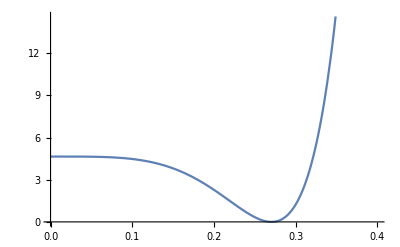

```mathematica
Plot[{chi2gg[gg]-chi2mingg}, {gg, 0,0.4}]
```

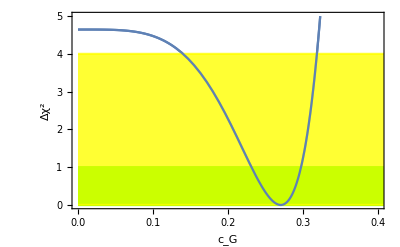

```mathematica
chi2plot=Plot[{chi2gg[gg]-chi2mingg},{gg,0.00,0.4},Frame->True,LabelStyle->{FontFamily->"Times",FontSize->18},Frame->True,PlotRange -> {{0,0.4},{0,5}}, FrameLabel->{{"Δχ^2",""},{"c_G","ATLAS data"}},LabelStyle->Directive[Black,Bold,15],FrameStyle->Directive[Black],BaseStyle->{FontFamily->"LatinModernRoman"},FrameTicksStyle->Directive[Black,20],RotateLabel -> False,Axes -> True];
s1IM=Plot[{0,1} ,{y,0.,20.},Filling->{1->{2}},FillingStyle->Directive[Opacity[1,Green]],PlotRange->{0,10},PlotStyle->Opacity[1,Green]];
s2IM=Plot[{0, 4} ,{y,0.,20.},Filling->{1->{2}},FillingStyle->Opacity[0.8,Yellow],PlotRange->{0,10},PlotStyle->Opacity[0.8,Yellow]];
Show[chi2plot,s1IM,s2IM,chi2plot,PlotLegends->True]
```

```mathematica
NotebookDirectory[]
```

/Users/esser/Documents/PROJECTS/ALPsPheno/ALP GLOBAL/notebooks/